```mathematica
(* Search terms for genomics *)featureList={"autosomal", "gen","mutat","gene-modified","germ","positive","negative","mutant", "mutation-associated", "sequenc","familial","insertion", "deletion","transposition", "dna", "exome", "haplotype","intron","linkage","allele", "polymorphism","rflp", "snp", "variant","homozygous","heterozygous"};

allTitles=Import[FileNameJoin[{NotebookDirectory[],"titles.txt"}],"Lines"];

binaryNamespaceFeaturesAllTitles=ParallelTable[If[StringContainsQ[allTitles[[title]],featureList[[feature]],IgnoreCase->True],1,0],{title,Length[allTitles]},{feature,Length[featureList]}];

visualizeTSNE[reducedData_,classifier_,label_]:=Module[{K,allClusters,reducedAllCluster,reducedAllClusterCenters,listPlotData,coreColors,otherColorsCount,legendColors,classes,mrkCC,mrkCP,legend,markers},

(* This classifies the data into clusters given the classifier. *)
K=Length[ClassifierInformation[classifier,"Classes"]];(*Print[K];*)
listPlotData=GatherBy[reducedData,classifier];

classes=ClassifierInformation[classifier,"Classes"];
coreColors={RGBColor[0.16,0.5,0.83],RGBColor[0.94,0.43,0.32],RGBColor[0.5,0.79,0.5],RGBColor[1,0.82,0.41],RGBColor[0.6,0,0.13]};
If[K<Length[coreColors],
coreColors=coreColors[[;;Abs[K]]];
];
otherColorsCount=K-Length[coreColors];
legendColors=coreColors;
If[otherColorsCount≠0,
AppendTo[legendColors,#]&/@RandomColor[otherColorsCount]
];

mrkCC=MapThread[Graphics[{#1,Style[Text[ToString[#2]],20,Bold]}]&,{legendColors,classes}];
mrkCP=MapThread[Graphics[{#,Disk[{0,0},ImageScaled[0.011]]}]&,{legendColors}];
legend=SwatchLegend[legendColors,classes,LegendMarkerSize->20];
markers=mrkCP;
AppendTo[markers,#]&/@mrkCC;
Return[ListPlot[listPlotData,PlotRange->All,ImageSize->800,AxesLabel->Automatic,PlotMarkers->markers,PlotLegends->legend,PlotLabel->label,LabelStyle->"Subsubsection",AspectRatio->1]];
]
```

```mathematica
namespaceFeaturesAllTitles=ParallelTable[If[StringContainsQ[allTitles[[title]],featureList[[feature]],IgnoreCase->True],1,0],{title,Length[allTitles]},{feature,Length[featureList]}];
```

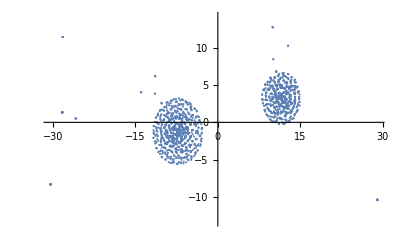
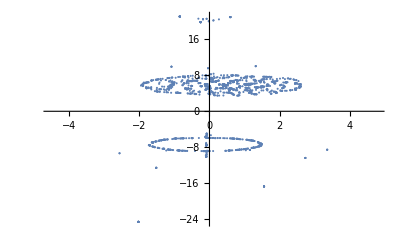
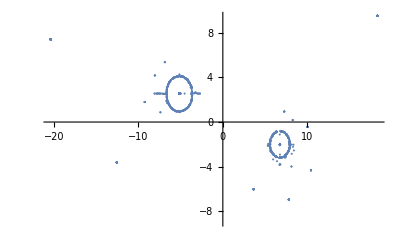
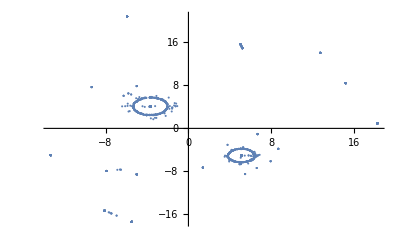
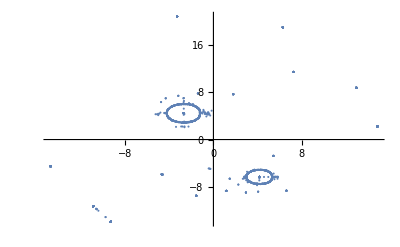
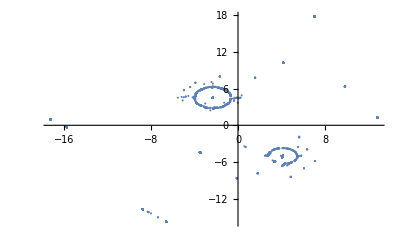
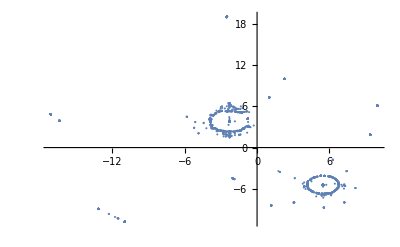
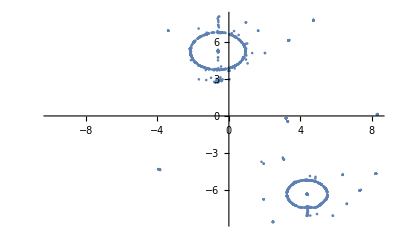
{-Graphics-Perplexity = 5,-Graphics-Perplexity = 10,-Graphics-Perplexity = 15,-Graphics-Perplexity = 20,-Graphics-Perplexity = 25,-Graphics-Perplexity = 30,-Graphics-Perplexity = 35,-Graphics-Perplexity = 40,-Graphics-Perplexity = 45,-Graphics-Perplexity = 50}

```mathematica
Labeled[ListPlot[DimensionReduce[binaryNamespaceFeaturesAllTitles,Method->{"TSNE","Perplexity"->#}],ImageSize->400],"Perplexity = "<>ToString[#],Top]&/@Range[5,50,5]
```

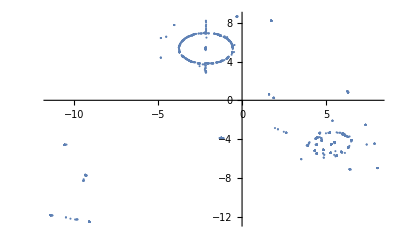
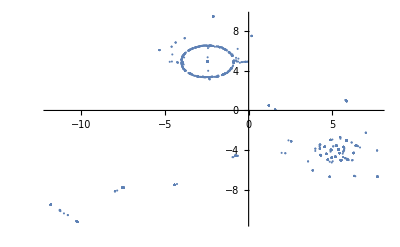
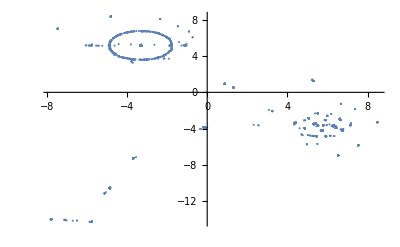
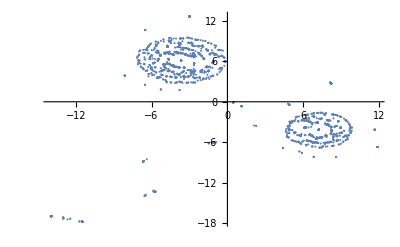
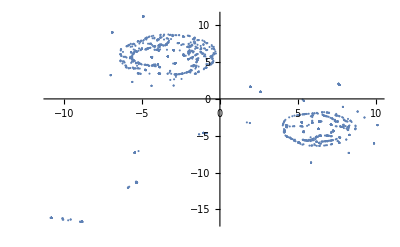
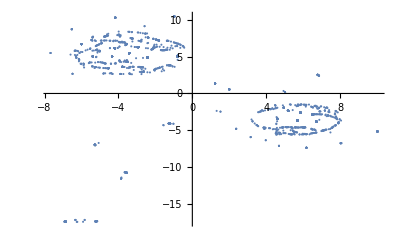
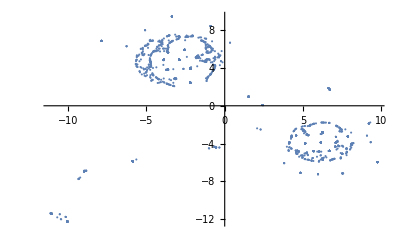
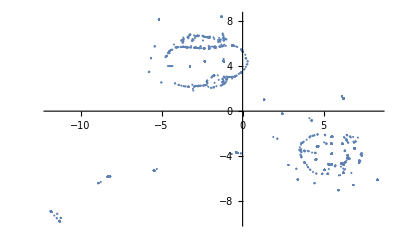
{-Graphics-Perplexity = 55,-Graphics-Perplexity = 60,-Graphics-Perplexity = 65,-Graphics-Perplexity = 70,-Graphics-Perplexity = 75,-Graphics-Perplexity = 80,-Graphics-Perplexity = 85,-Graphics-Perplexity = 90,-Graphics-Perplexity = 95,-Graphics-Perplexity = 100}

```mathematica
Labeled[ListPlot[DimensionReduce[binaryNamespaceFeaturesAllTitles,Method->{"TSNE","Perplexity"->#}],ImageSize->400],"Perplexity = "<>ToString[#],Top]&/@Range[55,100,5]
```

```mathematica
reducedNamespaceVectors=DimensionReduce[binaryNamespaceFeaturesAllTitles,Method->{"TSNE","Perplexity"->5}];
```

```mathematica
ReducedClassifier=ClusterClassify[reducedNamespaceVectors,Method->"GaussianMixture"]
```

ClassifierFunction[…]

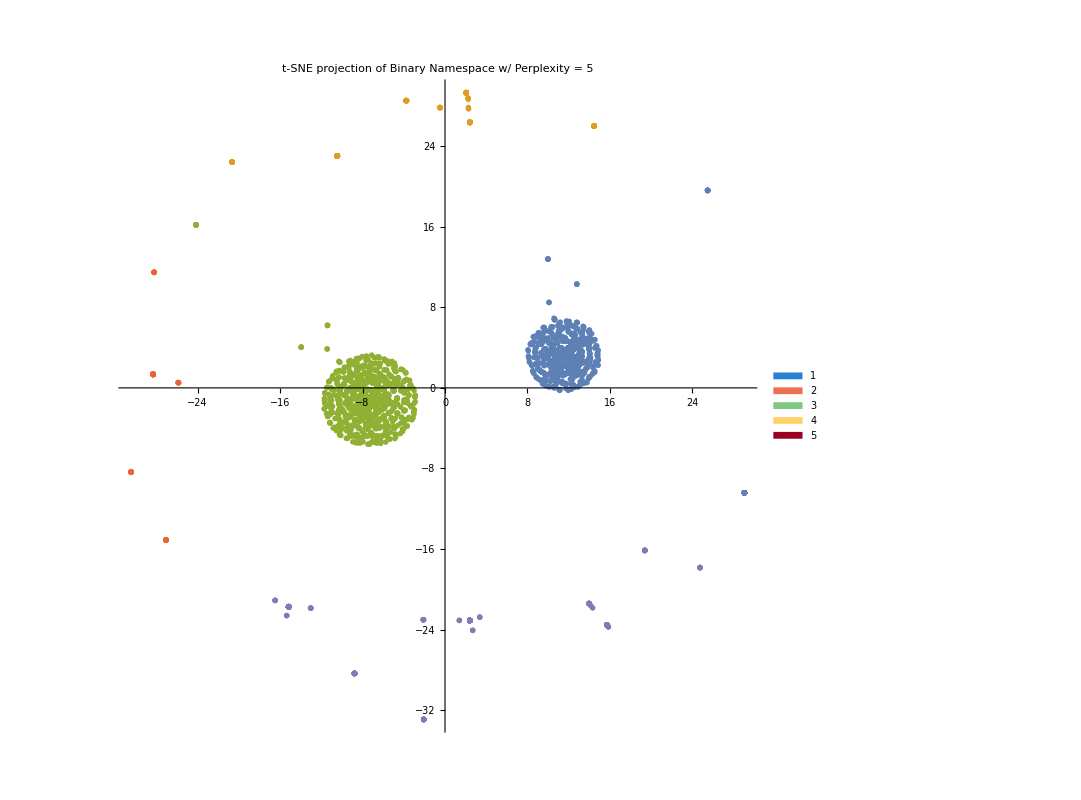

```mathematica
visualizeTSNE[reducedNamespaceVectors,ReducedClassifier,"t-SNE projection of Binary Namespace w/ Perplexity = 5"]
```

```mathematica
reducedAssoc=Thread[{allTitles,reducedNamespaceVectors}];
```

```mathematica
reducedAssocClustered=GatherBy[reducedAssoc,ReducedClassifier[#[[2]]]&];
```

```mathematica
titleColor[reducedFeatures_]:=Which[
ReducedClassifier[reducedFeatures]==1,RGBColor[0.16,0.5,0.83],
ReducedClassifier[reducedFeatures]==2,RGBColor[0.94,0.43,0.32],
ReducedClassifier[reducedFeatures]==3,RGBColor[0.5,0.79,0.5],
ReducedClassifier[reducedFeatures]==4,RGBColor[1,0.82,0.41],
ReducedClassifier[reducedFeatures]==5,RGBColor[0.6,0,0.13]
]
```

```mathematica
allTitlesColorized=Style[#[[1]],titleColor[#[[2]]]]&/@reducedAssoc;
```

```mathematica
Labeled[Framed[Pane[Grid[Transpose[{Range[Length[reducedAssoc]],allTitlesColorized}],Alignment->Left],Scrollbars->True,ImageSize->{Automatic,400}]],"All titles cluster-colorized",Top]
```

1 | Histological Chorioamnionitis Induces Differential Gene Expression in Human Cord Blood Mononuclear Leukocytes from Term Neonates
2 | Prenatal maternal antidepressants, anxiety, and depression and offspring DNA methylation: epigenome-wide associations at birth and persistence into early childhood
3 | Enhanced metastatic potential in the MB49 urothelial carcinoma model
4 | Whole Transcriptome Analysis of Renal Intercalated Cells Predicts Lipopolysaccharide Mediated Inhibition of Retinoid X Receptor alpha Function
5 | Engineered transfer RNAs for suppression of premature termination codons
6 | Selective Inactivation of Intracellular BiP/GRP78 Attenuates Endothelial Inflammation and Permeability in Acute Lung Injury
7 | Auditory sensory memory span for duration is severely curtailed in females with Rett syndrome
8 | BioVR: a platform for virtual reality assisted biological data integration and visualization
9 | Impact of chemotherapy for breast cancer on leukocyte DNA methylation landscape and cognitive function: a prospective study
10 | The second generation mixed-lineage kinase-3 (MLK3) inhibitor CLFB-1134 protects against neurotoxin-induced nigral dopaminergic neuron loss
11 | Protective transcriptional mechanisms in cardiomyocytes and cardiac fibroblasts
12 | Identification of a robust methylation classifier for cutaneous melanoma diagnosis
13 | Parenchymal and stromal tissue regeneration of tooth organ by pivotal signals reinstated in decellularized matrix
14 | Clinical Pharmacogenetics Implementation Consortium (CPIC) Guideline for the Use of Potent Volatile Anesthetic Agents and Succinylcholine in the Context of RYR1 or CACNA1S Genotypes
15 | Myofibroblast-specific YY1 promotes liver fibrosis
16 | Gestational Diabetes Epigenetically Reprograms the Cart Promoter in Fetal Ovary Causing Sub-Fertility in Adult Life.
17 | Auditory processing atypicalities for pure tones and complex speech sounds in Rett Syndrome: towards neuromarkers of disease progression.
18 | Human genes influence the interaction between Streptococcus mutans and host caries susceptibility: a genome-wide association study in children with primary dentition
19 | A multicenter retrospective study of charcot-marie-tooth disease type 4B (CMT4B) associated with mutations in myotubularin-related proteins (MTMRs)
20 | mTOR dysregulation by vaccinia virus F17 controls multiple processes with varying roles in infection.
21 | Bemarituzumab with modified FOLFOX6 for advanced FGFR2-positive gastroesophageal cancer: FIGHT Phase 3 study design
22 | Radiogenomics Consortium Genome-Wide Association Study Meta-analysis of Late Toxicity after Prostate Cancer Radiotherapy
23 | Myc-mediated transcriptional regulation of the mitochondrial chaperone TRAP1 controls primary and metastatic tumor growth
24 | The choice not to undergo genetic testing for Huntington disease: Results from the PHAROS study
25 | Autosomal dominant mitochondrial membrane protein-associated neurodegeneration (MPAN)
26 | Distinct roles for MDA5 and TLR3 in the acute response to inhaled double-stranded RNA
27 | MYC REGULATION OF A MITOCHONDRIAL TRAFFICKING NETWORK MEDIATES TUMOR CELL INVASION AND METASTASIS.
28 | Epigenome-wide association study reveals methylation pathways associated with childhood allergic sensitization
29 | Phenotype–genotype discrepancies in the prospective Huntington at-risk observational study
30 | Bone marrow mesenchymal stem cells from patients with SLE maintain an interferon signature during in vitro culture
31 | MAGE cancer-testis antigens protect the mammalian germline under environmental stress
32 | Transitional B cells in quiescent SLE: An early checkpoint imprinted by IFN
33 | The Role of Fgf9 In The Production of Neural Retina And Rpe In A Pluripotent Stem Cell Model of Early Human Retinal Development
34 | Critical role of autophagy regulator Beclin1 in endothelial cell inflammation and barrier disruption
35 | T-bet Transcription Factor Promotes Antibody-Secreting Cell Differentiation by Limiting the Inflammatory Effects of IFN-γ on B Cells
36 | Cauda Equina Syndrome as the first Manifestation of von Hippel-Lindau Disease: A Case Report
37 | Oligonucleotide Microarrays Identified Potential Regulatory Genes Related to Early Outward Arterial Remodeling Induced by Tissue Plasminogen Activator
38 | Genome Sequence of a Facklamia hominis Isolate from a Patient with Urosepsis.
39 | Transcriptome alterations in myotonic dystrophy skeletal muscle and heart.
40 | Decellularized Wharton jelly matrix: a biomimetic scaffold for ex vivo hematopoietic stem cell culture
41 | Critical Role of an MHC Class I-Like/Innate-Like T Cell Immune Surveillance System in Host Defense against Ranavirus (Frog Virus 3) Infection
42 | Lung cancer stem cells and their aggressive progeny, controlled by EGFR/MIG6 inverse expression, dictate a novel NSCLC treatment approach
43 | Single-cell RNA sequencing in facioscapulohumeral muscular dystrophy disease etiology and development.
44 | Intratumoral Hypoxia Reduces IFN-γ–Mediated Immunity and MHC Class I Induction in a Preclinical Tumor Model
45 | Targeting epigenetics and non-coding RNAs in atherosclerosis: From mechanisms to therapeutics
46 | Parasitoid wasp venom elevates sorbitol and alters expression of metabolic genes in human kidney cells
47 | Identification of a novel splice mutation in CTNNB1 gene in a Chinese family with both severe intellectual disability and serious visual defects
48 | Next-Generation-Sequencing-Based Hospital Outbreak Investigation Yields Insight into Klebsiella aerogenes Population Structure and Determinants of Carbapenem Resistance and Pathogenicity.
49 | Human Epididymis Secretory Protein 4 (HE4) Compromises Cytotoxic Mononuclear Cells via Inducing Dual Specificity Phosphatase 6
50 | A Novel Fluorescent and Bioluminescent Bireporter Influenza A Virus To Evaluate Viral Infections.
51 | Auditory sensory memory span for duration is severely curtailed in females with Rett Syndrome.
52 | Association of the Infant Gut Microbiome With Early Childhood Neurodevelopmental Outcomes
53 | Genetic determinants of risk in pulmonary arterial hypertension: international genome-wide association studies and meta-analysis
54 | Influenza Virus Vaccination Elicits Poorly Adapted B Cell Responses in Elderly Individuals
55 | Post-transcriptional pseudouridylation in mRNA as well as in some major types of noncoding RNAs
56 | Variation in SIPA1L2 is correlated with phenotype modification in Charcot– Marie– Tooth disease type 1A
57 | PUS7 mutations impair pseudouridylation in humans and cause intellectual disability and microcephaly
58 | CRISPR links to long noncoding RNA function in mice: A practical approach
59 | Clinical exome sequencing reveals locus heterogeneity and phenotypic variability of cohesinopathies
60 | PARP inhibitors in older patients with ovarian and breast cancer: Young International Society of Geriatric Oncology review paper
61 | TREM-1 Attenuates RIPK3-mediated Necroptosis in Hyperoxia-induced Lung Injury in Neonatal Mice
62 | Siblings with lethal primary pulmonary hypoplasia and compound heterozygous variants in the AARS2 gene: further delineation of the phenotypic spectrum
63 | Waterpipe smoke and e-cigarette vapor differentially affect circadian molecular clock gene expression in mouse lungs
64 | A Nationwide Screen of Carbapenem-Resistant Klebsiella pneumoniae Reveals an Isolate with Enhanced Virulence and Clinically Undetected Colistin Heteroresistance.
65 | Sirt1 Promotes Osteogenic Differentiation and Increases Alveolar Bone Mass via Bmi1 Activation in Mice
66 | The pre-mRNA splicing and transcription factor Tat-SF1 is a functional partner of the spliceosome SF3b1 subunit via a U2AF homology motif interface
67 | The Response of nor and nos Contributes to Staphylococcus aureus Virulence and Metabolism.
68 | Identification of the novel Ido1 imprinted locus and its potential epigenetic role in pregnancy loss
69 | LncEGFL7OS regulates human angiogenesis by interacting with MAX at the EGFL7/miR-126 locus
70 | Clinicopathological characterization of SMAD4-mutated intestinal adenocarcinomas: A case-control study
71 | MRI-informed muscle biopsies correlate MRI with pathology and DUX4 target gene expression in FSHD.
72 | Sample enrichment for clinical trials to show delay of onset in huntington disease
73 | Somatostatin Gene and Protein Expression in the Non-human Primate Central Extended Amygdala
74 | Attenuated Joint Tissue Damage Associated With Improved Synovial Lymphatic Function Following Treatment With Bortezomib in a Mouse Model of Experimental Posttraumatic Osteoarthritis
75 | Safety and efficacy of pridopidine in patients with Huntington's disease (PRIDE-HD): a phase 2, randomised, placebo-controlled, multicentre, dose-ranging study
76 | Preclinical study using androgen receptor (AR) degradation enhancer to increase radiotherapy efficacy via targeting radiation-increased AR to better suppress prostate cancer progression
77 | Expression network analysis reveals cord blood vitamin D-associated genes affecting risk of early life wheeze
78 | Exercise promotes a cardioprotective gene program in resident cardiac fibroblasts
79 | Streptococcus infantis, Streptococcus mitis, and Streptococcus oralis Strains With Highly Similar cps5 Loci and Antigenic Relatedness to Serotype 5 Pneumococci
80 | LAMP-2B regulates human cardiomyocyte function by mediating autophagosome–lysosome fusion
81 | Gain-of-function DNMT3A mutations cause microcephalic dwarfism and hypermethylation of Polycomb-regulated regions
82 | Human ESC-Derived Chimeric Mouse Models of Huntington’s Disease Reveal Cell-Intrinsic Defects in Glial Progenitor Cell Differentiation
83 | Organophosphate Pesticide Metabolite Concentrations in Urine during Pregnancy and Offspring Nonverbal IQ at Age 6 Years.
84 | Refining postoperative delirium: The case of a gene x protein interaction
85 | Germline cancer susceptibility gene variants, somatic second hits, and survival outcomes in patients with resected pancreatic cancer
86 | Preclinical study using circular RNA 17 and micro RNA 181c-5p to suppress the enzalutamide-resistant prostate cancer progression
87 | FAM210B is an erythropoietin target and regulates erythroid heme synthesis by controlling mitochondrial iron import and ferrochelatase activity
88 | Next-generation sequencing based hospital outbreak investigation yields insight into Klebsiella aerogenes population structure and determinants of carbapenem resistance and virulence
89 | Identification of new high affinity targets for Roquin based on structural conservation
90 | A nucleosome-free region locally abrogates histone H1–dependent restriction of linker DNA accessibility in chromatin
91 | Modulation of Innate Immune Responses by the Influenza A NS1 and PA-X Proteins
92 | Diverse vectors and mechanisms spread NDM beta-lactamases among carbapenem resistant Enterobacteriaceae in the Greater Boston area.
93 | The effect of tissue composition on gene co-expression
94 | Adipocyte-specific Repression of PPAR-gamma by NCoR Contributes to Scleroderma Skin Fibrosis
95 | Divergence in the transcriptional landscape between low temperature and freeze shock in cultivated grapevine (Vitis vinifera)
96 | Transcriptional Regulation on Aneuploid Chromosomes in Divers Candida albicans Mutants
97 | Exome sequencing identifies gene variants and networks associated with extreme respiratory outcomes following preterm birth
98 | Comparative genomic, transcriptomic, and proteomic reannotation of human herpesvirus 6
99 | Mutations in MAST1 Cause Mega-Corpus-Callosum Syndrome with Cerebellar Hypoplasia and Cortical Malformations
100 | Effect of low level laser and low intensity pulsed ultrasound therapy on bone remodeling during orthodontic tooth movement in rats
101 | CDK12 regulates DNA repair genes by suppressing intronic polyadenylation
102 | Methods for high-dimensional analysis of cells dissociated from cryopreserved synovial tissue
103 | Streptococcus mitis Expressing Pneumococcal Serotype 1 Capsule
104 | Lung cellular senescence is independent of aging in a mouse model of COPD/emphysema
105 | Serpine1 Knockdown Enhances MMP Activity after Flexor Tendon Injury in Mice: Implications for Adhesions Therapy
106 | Assessing Copy Number Aberrations and Copy Neutral Loss of Heterozygosity Across the Genome as Best Practice: An Evidence Based Review of Clinical Utility from the Cancer Genomics Consortium (CGC) Working Group for Myelodysplastic Syndrome, Myelodysplastic/Myeloproliferative and Myeloproliferative Neoplasms
107 | Specificity and functional interplay between influenza virus PA-X and NS1 shutoff activity
108 | Single-nucleus RNA-seq identifies divergent populations of FSHD2 myotube nuclei
109 | 1761. Effect of Carbapenem-Resistant Enterobacteriaceae (CRE) Surveillance Case Definition Change on CRE Epidemiology—Selected US Sites, 2015–2016
110 | The Ectodomain of the Vaccinia Virus Glycoprotein A34 Is Required for Cell Binding by Extracellular Virions and Contains a Large Region Capable of Interaction with Glycoprotein B5.
111 | Environmental cues received during development shape dendritic cell responses later in life
112 | Systematic exploration of cell morphological phenotypes associated with a transcriptomic query
113 | Conditional deletion of Ahr alters gene expression profiles in hematopoietic stem cells
114 | Water Contaminants Associated With Unconventional Oil and Gas Extraction Cause Immunotoxicity to Amphibian Tadpoles.
115 | Estrogen receptor β promotes bladder cancer growth and invasion via alteration of miR-92a/DAB2IP signals
116 | Endophenotypes: A conceptual link between anorexia nervosa and autism spectrum disorder
117 | Nuclear transglutaminase 2 directly regulates expression of cathepsin S in rat cortical neurons
118 | Overexpressed Sirt1 in MSCs Promotes Dentin Formation in Bmi1-Deficient Mice
119 | Radiation biology and oncology in the genomic era
120 | T Cell–Dependent Affinity Maturation and Innate Immune Pathways Differentially Drive Autoreactive B Cell Responses in Rheumatoid Arthritis
121 | Psoriasis: Psychosomatic, Somatopsychic, or Both?
122 | Flavonoid biosynthetic pathways in plants: Versatile targets for metabolic engineering
123 | A novel role for C–C motif chemokine receptor 2 during infection with hypervirulent Mycobacterium tuberculosis
124 | Identification of a panel of genes as a prognostic biomarker for glioblastoma
125 | Identification of Amino Acid Residues Responsible for Inhibition of Host Gene Expression by Influenza A H9N2 NS1 Targeting of CPSF30
126 | Prepubertal skeletal muscle growth requires Pax7-expressing satellite cell-derived myonuclear contribution
127 | Basal levels of (p)ppGpp differentially affect the pathogenesis of infective endocarditis in Enterococcus faecalis
128 | Facioscapulohumeral Muscular Dystrophy: Update on Pathogenesis and Future Treatments
129 | PI3Kγ promotes vascular smooth muscle cell phenotypic modulation and transplant arteriosclerosis via a SOX9-dependent mechanism
130 | Therapeutic approaches to Huntington disease: from the bench to the clinic
131 | NEW GENES, FUNCTIONS AND BIOMARKERS O.4Single-cell RNA-sequencing in facioscapulohumeral muscular dystrophy disease: etiology and development
132 | Rag1 and rag2 gene expressions identify lymphopoietic tissues in juvenile and adult Chinese giant salamander (Andrias davidianus)
133 | Novel 1.3 Mb germline duplication in chromosome 8q21.11 by microarray comparative genomic hybridization plus single nucleotide polymorphism analysis in an adult patient with pancytopenia and urinary bladder complications
134 | Cell-specific qRT-PCR of renal epithelial cells reveals a novel innate immune signature in murine collecting duct.
135 | Degradable poly(ethylene glycol) (PEG)-based hydrogels for spatiotemporal control of siRNA/nanoparticle delivery
136 | Runx1 Role in Epithelial and Cancer Cell Proliferation Implicates Lipid Metabolism and Scd1 and Soat1 Activity
137 | ARID1A, a SWI/SNF subunit, is critical to acinar cell homeostasis and regeneration and is a barrier to transformation and epithelial-mesenchymal transition in the pancreas
138 | PPARα-mediated peroxisome induction compensates PPARγ-deficiency in bronchiolar club cells
139 | Potential Metabolomic Linkage in Blood between Parkinson’s Disease and Traumatic Brain Injury
140 | HE4 suppresses the expression of osteopontin in mononuclear cells and compromises their cytotoxicity against ovarian cancer cells
141 | CRISPR-Cas9–Mediated Epitope Tagging Provides Accurate and Versatile Assessment of Myocardin—Brief Report
142 | Burkitt Lymphoma- A Rare But Challenging Lymphoma
143 | Re-Evaluating One-step Generation of Mice Carrying Conditional Alleles by CRISPR-Cas9-Mediated Genome Editing Technology
144 | Enhanced cerebellar myelination with concomitant iron elevation and ultrastructural irregularities following prenatal exposure to ambient particulate matter in the mouse
145 | Loss of α-Calcitonin Gene-Related Peptide (αCGRP) Reduces Otolith Activation Timing Dynamics and Impairs Balance
146 | High-Throughput Screening Identifies Genes Required for Candida albicans Induction of Macrophage Pyroptosis
147 | Who’s Driving? Human Cytomegalovirus, Interferon, and NFκB Signaling
148 | Cognition among individuals along a spectrum of increased risk for Parkinson’s disease
149 | Motoneuron Wnts regulate neuromuscular junction development
150 | Coupling Green Fluorescent Protein Expression with Chemical Modification to Probe Functionally Relevant Riboswitch Conformations in Live Bacteria.
151 | Small noncoding RNAs in FSHD2 muscle cells reveal both DUX4- and SMCHD1-specific signatures.
152 | Long-term follow-up of permanent atrial standstill in a German family with mutation in the SCN5A gene
153 | Innate Immune Cells Are Regulated by Axl in Hypertensive Kidney
154 | Prenatal maternal stress, fetal programming, and mechanisms underlying later psychopathology—A global perspective
155 | 47. Deletion of the 3′ MEIS2 (15q14) gene in two siblings with mild phenotypes and parental mosaicism
156 | A Genome-Wide Screen of Deletion Mutants in the Filamentous Saccharomyces cerevisiae Background Identifies Ergosterol as a Direct Trigger of Macrophage Pyroptosis
157 | Functional Evolution of the 2009 Pandemic H1N1 Influenza Virus NS1 and PA in Humans
158 | Bilateral Pheochromocytomas in a Patient with Y175C Von Hippel-Lindau Mutation
159 | The immune cell landscape in kidneys of lupus nephritis patients
160 | RNAi-Mediated Loss of Function of Xenopus Immune Genes by Transgenesis.
161 | Androgen Receptor Signaling Reduces Radiosensitivity in Bladder Cancer
162 | CYP1A1 gene polymorphisms modify the association between PM10 exposure and lung function
163 | Effect of prior vaccination on carriage rates of Streptococcus pneumoniae in older adults: A longitudinal surveillance study
164 | Monosomy 18p is a risk factor for facioscapulohumeral dystrophy
165 | Signalling pathways regulating galactosaminoglycan synthesis and structure in vascular smooth muscle: Implications for lipoprotein binding and atherosclerosis
166 | Cell type-specific effects of Notch signaling activation on intervertebral discs: Implications for intervertebral disc degeneration
167 | HIITE: HIV-1 incidence and infection time estimator.
168 | Early-onset epileptic encephalopathy with myoclonic seizures related to 9q33.3-q34.11 deletion involving STXBP1 and SPTAN1 genes
169 | Phenotypes, genotypes, and the management of paroxysmal movement disorders
170 | An intronic mutation c.6430-3C>G in the F8 gene causes splicing efficiency and premature termination in hemophilia A
171 | Testing Genetic Modifiers of Behavior and Response to Atomoxetine in Autism Spectrum Disorder with ADHD
172 | Obesity/type 2 diabetes increases inflammation, periosteal reactive bone formation, and osteolysis during Staphylococcus aureus implant-associated bone infection
173 | Whole genome sequence and phenotypic characterization of a Cbm+ serotype e strain of Streptococcus mutans
174 | 2125 What genes are involved in the brain food reward circuitry: Findings from a large candidate gene analysis
175 | Maternal polymorphisms in glutathione-related genes are associated with maternal mercury concentrations and early child neurodevelopment in a population with a fish-rich diet
176 | Four days of simulated shift work reduces insulin sensitivity in humans
177 | Genetic determinants of risk and survival in pulmonary arterial hypertension
178 | ERβ-mediated alteration of circATP2B1 and miR-204-3p signaling promotes invasion of clear cell renal cell carcinoma
179 | Disruption of a Novel Iron Transport System Reverses Oxidative Stress Phenotypes of a dpr Mutant Strain of Streptococcus mutans
180 | Machine Learning on a Genome-Wide Association Study to Predict Late Genitourinary Toxicity Following Prostate Radiotherapy
181 | Variant pathogenicity evaluation in the community-driven Inherited Neuropathy Variant Browser
182 | Differential gene expression in trigeminal ganglia of male and female rats following chronic constriction of the infraorbital nerve
183 | BET-ting on Nrf2: How Nrf2 Signaling can Influence the Therapeutic Activities of BET Protein Inhibitors
184 | Neonatal DNA methylation and early-onset conduct problems: A genome-wide, prospective study
185 | Redox regulation of circadian molecular clock in chronic airway diseases
186 | A Recurrent De Novo PACS2 Heterozygous Missense Variant Causes Neonatal-Onset Developmental Epileptic Encephalopathy, Facial Dysmorphism, and Cerebellar Dysgenesis
187 | Methylation of DNA and chromatin as a mechanism of oncogenesis and therapeutic target in neuroblastoma
188 | Distinct MHC class I-like interacting invariant T cell lineage at the forefront of mycobacterial immunity uncovered in Xenopus
189 | Inhibition of Tip60 Reduces Lytic and Latent Gene Expression of Kaposi’s Sarcoma-Associated Herpes Virus (KSHV) and Proliferation of KSHV-Infected Tumor Cells
190 | Systematic evaluation of a targeted gene capture sequencing panel for molecular diagnosis of retinitis pigmentosa
191 | Characterization of the Trehalose Utilization Operon in Streptococcus mutans Reveals that the TreR Transcriptional Regulator Is Involved in Stress Response Pathways and Toxin Production
192 | Endoribonuclease YbeY Is Linked to Proper Cellular Morphology and Virulence in Brucella abortus
193 | Osteoglycin attenuates cardiac fibrosis by suppressing cardiac myofibroblast proliferation and migration through antagonizing lysophosphatidic acid 3/matrix metalloproteinase 2/epidermal growth factor receptor signalling.
194 | Scarring in Patients With PIK3CA-Related Overgrowth Syndromes
195 | Importins α and β signaling mediates endothelial cell inflammation and barrier disruption
196 | Screening Gene Knockout Mice for Variation in Bone Mass: Analysis by μCT and Histomorphometry
197 | Systematic Complex Haploinsufficiency-Based Genetic Analysis of Candida albicans Transcription Factors: Tools and Applications to Virulence-Associated Phenotypes
198 | Review of the Diagnosis and Treatment of Periodic Paralysis
199 | Correction for Yang et al., “Tolerance to Caspofungin in Candida albicans Is Associated with at Least Three Distinctive Mechanisms That Govern Expression of FKS Genes and Cell Wall Remodeling”
200 | Tissue-Resident Memory CD8+ T Cells: From Phenotype to Function
201 | Vaccinia Virus Phospholipase Protein F13 Promotes Rapid Entry of Extracellular Virions into Cells
202 | Association of Alterations in Main Driver Genes With Outcomes of Patients With Resected Pancreatic Ductal Adenocarcinoma
203 | TR4 nuclear receptor suppresses HCC cell invasion via downregulating the EphA2 expression
204 | Frog's DCs have it all in one
205 | An Exploration of the Determinants of Gestational Weight Gain in African American Women: Genetic Factors and Energy Expenditure
206 | Using single-index ODEs to study dynamic gene regulatory network
207 | Smchd1 haploinsufficiency exacerbates the phenotype of a transgenic FSHD1 mouse model.
208 | Family environments and leukocyte transcriptome indicators of a proinflammatory phenotype in children and parents
209 | Serum Response Factor Is Essential for Maintenance of Podocyte Structure and Function
210 | Insights from structures of cancer-relevant pre-mRNA splicing factors.
211 | Evidence for convergent evolution of SINE-directed Staufen-mediated mRNA decay
212 | The Effects of Biological Fluids on Colloidal Stability and siRNA Delivery of a pH-Responsive Micellar Nanoparticle Delivery System.
213 | Human Epididymis Protein 4 Promotes Events Associated with Metastatic Ovarian Cancer via Regulation of the Extracelluar Matrix
214 | FKS2 and FKS3 Genes of Opportunistic Human Pathogen Candida albicans Influence Echinocandin Susceptibility
215 | Deep characterization of a common D4Z4 variant identifies biallelic DUX4 expression as a modifier for disease penetrance in FSHD2
216 | Differential effects of alcohol and its metabolite acetaldehyde on vascular smooth muscle cell Notch signaling and growth.
217 | Depletion of transglutaminase 2 in neurons alters expression of extracellular matrix and signal transduction genes and compromises cell viability
218 | Stabilization of NF-κB-Inducing Kinase Suppresses MLL-AF9-Induced Acute Myeloid Leukemia
219 | Chapter 18 Genetics of Bone Fat and Energy Regulation
220 | Historical Landmarks in an Understanding of the Lymphomas
221 | Chapter 35 Facioscapulohumeral muscular dystrophy
222 | Chapter 45 Neurogenetics of Pelizaeus–Merzbacher disease
223 | Chapter 32 Periodic paralysis
224 | Flow-dependent epigenetic regulation of IGFBP5 expression by H3K27me3 contributes to endothelial anti-inflammatory effects
225 | Chapter 11 Biology of Bone and Cartilage
226 | Clinicopathologic and Immunohistochemical Study of Combined Small Cell Carcinoma and Urothelial Carcinoma Molecular Subtype
227 | RgpF Is Required for Maintenance of Stress Tolerance and Virulence in Streptococcus mutans
228 | Mammalian Adaptation of an Avian Influenza A Virus Involves Stepwise Changes in NS1
229 | Statistical Approaches to Decreasing the Discrepancy of Non-detects in qPCR Data
230 | Autophagy protein ATG16L1 prevents necroptosis in the intestinal epithelium
231 | Suberanilohydroxamic Acid as a Pharmacological Kruppel-Like Factor 2 Activator That Represses Vascular Inflammation and Atherosclerosis
232 | Together JUN and DDIT3 (CHOP) control retinal ganglion cell death after axonal injury
233 | Erythropoietin Signaling Regulates Key Epigenetic and Transcription Networks in Fetal Neural Progenitor Cells
234 | C1QBP suppresses cell adhesion and metastasis of renal carcinoma cells
235 | The Candida albicans transcription factor Cas5 couples stress responses, drug resistance and cell cycle regulation
236 | Quantitation of DNA methylation in Epstein-Barr virus–associated nasopharyngeal carcinoma by bisulfite amplicon sequencing
237 | Alcohol Reduces Arterial Remodeling by Inhibiting Sonic Hedgehog-Stimulated Stem Cell Antigen-1 Positive Progenitor Stem Cell Expansion
238 | Epigenome alterations in aortic valve stenosis and its related left ventricular hypertrophy
239 | Pseudomonas Endocarditis with an unstable phenotype: the challenges of isolate characterization and Carbapenem stewardship with a partial review of the literature
240 | Transcription profiles of the responses of chicken bursae of Fabricius to IBDV in different timing phases
241 | Meta-analysis of cell- specific transcriptomic data using fuzzy c-means clustering discovers versatile viral responsive genes
242 | The nuclear receptor and clock gene REV-ERBα regulates cigarette smoke-induced lung inflammation
243 | DNA methylation profiling in peripheral lung tissues of smokers and patients with COPD
244 | MicroRNA expression profiling defines the impact of electronic cigarettes on human airway epithelial cells
245 | NuA4 histone acetyltransferase activity is required for H4 acetylation on a dosage-compensated monosomic chromosome that confers resistance to fungal toxins
246 | The HIV Genomic Incidence Assay Meets False Recency Rate and Mean Duration of Recency Infection Performance Standards
247 | Transcriptomic Biomarkers to Discriminate Bacterial from Nonbacterial Infection in Adults Hospitalized with Respiratory Illness
248 | BET bromodomain inhibitors and agonists of the beta-2 adrenergic receptor identified in screens for compounds that inhibit DUX4 expression in FSHD muscle cells
249 | SMCHD1 regulates a limited set of gene clusters on autosomal chromosomes
250 | RERG suppresses cell proliferation, migration and angiogenesis through ERK/NF-κB signaling pathway in nasopharyngeal carcinoma
251 | Activation of Yap1/Taz signaling in ischemic heart disease and dilated cardiomyopathy
252 | Reflex Modification Audiometry Reveals Dual Roles for Olivocochlear Neurotransmission
253 | Cardiac metabolic effects of KNa1.2 channel deletion, and evidence for its mitochondrial localization.
254 | The K186E Amino Acid Substitution in the Canine Influenza Virus H3N8 NS1 Protein Restores Its Ability To Inhibit Host Gene Expression
255 | Diblock Copolymer Hydrophobicity Facilitates Efficient Gene Silencing and Cytocompatible Nanoparticle-Mediated siRNA Delivery to Musculoskeletal Cell Types.
256 | Estrogen–Estrogen Receptor α Signaling Facilitates Bilirubin Metabolism in Regenerating Liver Through Regulating Cytochrome P450 2A6 Expression
257 | Xenopus-FV3 host-pathogen interactions and immune evasion
258 | LungMAP: The Molecular Atlas of Lung Development Program
259 | Common variation in the autism risk gene CNTNAP2, brain structural connectivity and multisensory speech integration
260 | 206 The Mitophagy Receptor FUNDC-1 Contributes to Hypoxia-Reoxygenation Stress in C. elegans
261 | JT interval: What does this interval mean?
262 | Contribution of rare inherited and de novo variants in 2,871 congenital heart disease probands
263 | The homeodomain-interacting protein kinase HPK-1 preserves protein homeostasis and longevity through master regulatory control of the HSF-1 chaperone network and TORC1-restricted autophagy in Caenorhabditis elegans
264 | galK-based suicide vector mediated allelic exchange in Mycobacterium abscessus
265 | Clinical and Genome-Wide Analysis of Cisplatin-Induced Peripheral Neuropathy in Survivors of Adult-Onset Cancer
266 | The Ets2 Repressor Factor (Erf) Is Required for Effective Primitive and Definitive Hematopoiesis
267 | Covalent Modifications of Histone H3K9 Promote Binding of CHD3
268 | Superior turbinate eosinophilia correlates with olfactory deficit in chronic rhinosinusitis patients
269 | Toward the human cellular microRNAome
270 | p53 alteration in morphologically normal/benign breast luminal cells in BRCA carriers with or without history of breast cancer
271 | Multivariate analyses of peripheral blood leukocyte transcripts distinguish Alzheimer's, Parkinson's, control, and those at risk for developing Alzheimer's
272 | The function of Drosophila larval class IV dendritic arborization sensory neurons in the larval-pupal transition is separable from their function in mechanical nociception responses
273 | Cancer-Associated Mutations Mapped on High-Resolution Structures of the U2AF2 RNA Recognition Motifs.
274 | Androgens Regulate Ovarian Gene Expression Through Modulation of Ezh2 Expression and Activity.
275 | Functional Evolution of Influenza Virus NS1 Protein in Currently Circulating Human 2009 Pandemic H1N1 Viruses
276 | Interplay of PA-X and NS1 Proteins in Replication and Pathogenesis of a Temperature-Sensitive 2009 Pandemic H1N1 Influenza A Virus
277 | Constitutive expression of SlTrxF increases starch content in transgenic Arabidopsis
278 | Identifying drug resistant cancer cells using microbubble well arrays
279 | Infiltrating Myeloid Cells Exert Protumorigenic Actions via Neutrophil Elastase
280 | Sex- and brain region- specific effects of prenatal stress and lead exposure on permissive and repressive post-translational histone modifications from embryonic development through adulthood
281 | Transcriptome Profiling in Systems Vascular Medicine
282 | Genetic analysis of the Candida albicans biofilm transcription factor network using simple and complex haploinsufficiency
283 | Heterozygote galactocerebrosidase (GALC) mutants have reduced remyelination and impaired myelin debris clearance following demyelinating injury.
284 | Congenital diaphragmatic hernias: from genes to mechanisms to therapies
285 | miR-451 limits CD4+ T cell proliferative responses to infection in mice
286 | Pigmented epithelioid melanocytoma (animal-type melanoma): An institutional experience
287 | Human iPSC Glial Mouse Chimeras Reveal Glial Contributions to Schizophrenia
288 | CYP3A genes and the association between prenatal methylmercury exposure and neurodevelopment
289 | Interplay between miR-574-3p and hnRNP L regulates VEGFA mRNA translation and tumorigenesis
290 | Phospholipase Cγ1 Mediates Intima Formation Through Akt-Notch1 Signaling Independent of the Phospholipase Activity
291 | Obesity/Type II diabetes alters macrophage polarization resulting in a fibrotic tendon healing response
292 | Variants in WFS1 and Other Mendelian Deafness Genes Are Associated with Cisplatin-Associated Ototoxicity
293 | Central Hypothyroidism Due to a TRHR Mutation Causing Impaired Ligand Affinity and Transactivation of Gq.
294 | FUNNEL-GSEA: FUNctioNal ELastic-net regression in time-course gene set enrichment analysis
295 | The complex genetics of hypoplastic left heart syndrome
296 | The SERTAD protein Taranis plays a role in Polycomb-mediated gene repression
297 | MAIT cells launch a rapid, robust and distinct hyperinflammatory response to bacterial superantigens and quickly acquire an anergic phenotype that impedes their cognate antimicrobial function: Defining a novel mechanism of superantigen-induced immunopathology and immunosuppression
298 | The Slo(w) path to identifying the mitochondrial channels responsible for ischemic protection.
299 | Maternal prenatal anxiety and child COMT genotype predict working memory and symptoms of ADHD
300 | Metalloriboswitches: RNA-based inorganic ion sensors that regulate genes
301 | Adaptive Upregulation of Clumping Factor A (ClfA) by Staphylococcus aureus in the Obese, Type 2 Diabetic Host Mediates Increased Virulence
302 | Factors related to genetic testing in adults at risk for Huntington disease: the prospective Huntington at-risk observational study (PHAROS)
303 | Targeting DMPK with Antisense Oligonucleotide Improves Muscle Strength in Myotonic Dystrophy Type 1 Mice
304 | Neuroimaging findings in Mowat–Wilson syndrome: a study of 54 patients
305 | Exploring the functions of nonclassical MHC class Ib genes in Xenopus laevis by the CRISPR/Cas9 system
306 | Precision medicine for gallbladder cancer using somatic copy number amplifications (SCNA) and DNA repair pathway gene alterations.
307 | Characterization of anti-CD19 chimeric antigen receptor (CAR) T cell-mediated tumor microenvironment immune gene profile in a multicenter trial (ZUMA-1) with axicabtagene ciloleucel (axi-cel, KTE-C19).
308 | In situ bone tissue engineering via ultrasound-mediated gene delivery to endogenous progenitor cells in mini-pigs
309 | Multiple modality biomarker prediction of cognitive impairment in prospectively followed de novo Parkinson disease
310 | Rescue of Sendai Virus from Cloned cDNA
311 | StTrxF, a potato plastidic thioredoxin F-type protein gene, is involved in starch accumulation in transgenic Arabidopsis thaliana
312 | Editor's Highlight: Glutathione S-Transferase Activity Moderates Methylmercury Toxicity During Development in Drosophila.
313 | Optimized logic rules reveal interferon-γ-induced modes regulated by histone deacetylases and protein tyrosine phosphatases
314 | Blockade of RAGE ameliorates elastase-induced emphysema development and progression via RAGE-DAMP signaling
315 | Lung Gene Expression Analysis (LGEA): an integrative web portal for comprehensive gene expression data analysis in lung development
316 | 296 Bleach baths promote early induction of inflammatory pathway genes with no effect on skin bacterial dysbiosis in AD subjects
317 | Identification and Characterization of a Class of MALAT1-like Genomic Loci
318 | Splicing Factor Mutations in Myelodysplasias: Insights from Spliceosome Structures
319 | 403 S. aureus colonization is associated with dysregulation of lipid-related genes in the nonlesional skin of AD subjects
320 | Androgen receptor (AR) promotes clear cell renal cell carcinoma (ccRCC) migration and invasion via altering the circHIAT1/miR-195-5p/29a-3p/29c-3p/CDC42 signals
321 | Tolerance to Caspofungin in Candida albicans Is Associated with at Least Three Distinctive Mechanisms That Govern Expression of FKS Genes and Cell Wall Remodeling
322 | Obesity/Type II Diabetes Alters Macrophage Polarization Resulting in a Fibrotic Tendon Healing Response
323 | SOX9 Is an Astrocyte-Specific Nuclear Marker in the Adult Brain Outside the Neurogenic Regions.
324 | Long-term follow-up of a randomized AAV2-GAD gene therapy trial for Parkinson’s disease
325 | Development of Recombinant Arenavirus-Based Vaccines
326 | Modeling the Mutational and Phenotypic Landscapes of Pelizaeus-Merzbacher Disease with Human iPSC-Derived Oligodendrocytes
327 | Linker histones: Novel insights into structure-specific recognition of the nucleosome
328 | Caffeine, creatine, GRIN2A and Parkinson's disease progression
329 | Vinpocetine Attenuates Pathological Cardiac Remodeling by Inhibiting Cardiac Hypertrophy and Fibrosis
330 | Inactivation of the spxA1 or spxA2 gene of Streptococcus mutans decreases virulence in the rat caries model
331 | A live-attenuated influenza vaccine for H3N2 canine influenza virus
332 | Loss of LMOD1 impairs smooth muscle cytocontractility and causes megacystis microcolon intestinal hypoperistalsis syndrome in humans and mice
333 | Towards the human cellular microRNAome
334 | Radiation induced pulmonary fibrosis as a model of progressive fibrosis: Contributions of DNA damage, inflammatory response and cellular senescence genes
335 | Constitutive expression of StAATP, a potato plastidic ATP/ADP transporter gene, increases starch content in transgenic Arabidopsis
336 | Who Has Therapy-Related AML?
337 | NS1 Protein Amino Acid Changes D189N and V194I Affect Interferon Responses, Thermosensitivity, and Virulence of Circulating H3N2 Human Influenza A Viruses
338 | Tumor Immunology Viewed from Alternative Animal Models—the Xenopus Story
339 | Three novel mutations of ARG1 identified in Chinese patients with argininemia detected by newborn screening
340 | Long term effects of carbaryl exposure on antiviral immune responses in Xenopus laevis
341 | Computational methods using genome-wide association studies to predict radiotherapy complications and to identify correlative molecular processes
342 | SIRT6 protects against endothelial dysfunction and atherosclerosis in mice
343 | Dysregulation of B Cell Repertoire Formation in Myasthenia Gravis Patients Revealed through Deep Sequencing
344 | Serum response factor regulates smooth muscle contractility via myotonic dystrophy protein kinases and L-type calcium channels
345 | Sorafenib with ASC-J9® synergistically suppresses the HCC progression via altering the pSTAT3-CCL2/Bcl2 signals
346 | Concise Review: Stem Cell-Based Treatment of Pelizaeus-Merzbacher Disease
347 | A Recurrent De Novo Variant in NACC1 Causes a Syndrome Characterized by Infantile Epilepsy, Cataracts, and Profound Developmental Delay
348 | Autolysosome biogenesis and developmental senescence are regulated by both Spns1 and v-ATPase
349 | Epilepsy-causing sequence variations in SIK1 disrupt synaptic activity response gene expression and affect neuronal morphology
350 | Notch activation enhances mesenchymal stem cell sheet osteogenic potential by inhibition of cellular senescence
351 | Clomipramine causes osteoporosis by promoting osteoclastogenesis via E3 ligase Itch, which is prevented by Zoledronic acid
352 | Avian Interferons and Their Antiviral Effectors
353 | A four gene signature predictive of recurrent prostate cancer
354 | A genome wide dosage suppressor network reveals genomic robustness
355 | Heterologous expression of Streptococcus mutans Cnm in Lactococcus lactis promotes intracellular invasion, adhesion to human cardiac tissues and virulence
356 | HLA Alleles are Genetic Markers for Susceptibility and Resistance towards Leprosy in a Mexican Mestizo Population
357 | CEDNIK
358 | Preconditioned Random Forest Regression: Application to Genome-Wide Study for Radiotherapy Toxicity Prediction
359 | An Exploration of Gene-Gene Interactions and Their Effects on Hypertension
360 | Molecular Characterization of Carbapenem-Resistant Enterobacteriaceae in the USA, 2011–2015
361 | Application to Gene Therapy and Vaccination
362 | Chapter Thirteen TR2 and TR4 Orphan Nuclear Receptors An Overview
363 | Temporal and Racial Differences Associated with Atopic Dermatitis Staphylococcus aureus and Encoded Virulence Factors
364 | Identification of differentially regulated genes in human patent ductus arteriosus
365 | Polymorphisms in the estrogen receptor alpha gene (ESR1), daily cycling estrogen and mammographic density phenotypes.
366 | HE4 promotes collateral resistance to cisplatin and paclitaxel in ovarian cancer cells
367 | PathCellNet: Cell-type specific pathogen-response network explorer
368 | The Healthy Infant Nasal Transcriptome: A Benchmark Study
369 | Lymphatic endothelial cells efferent to inflamed joints produce iNOS and inhibit lymphatic vessel contraction and drainage in TNF-induced arthritis in mice
370 | Hereditary Neuropathy With Liability to Pressure Palsies
371 | Acetylation Mimics Within a Single Nucleosome Alter Local DNA Accessibility In Compacted Nucleosome Arrays
372 | Gene expression profiling of epigenetic chromatin modification enzymes and histone marks by cigarette smoke: implications for COPD and lung cancer
373 | miRNAs Regulate hERG
374 | The mixed-lineage kinase 3 inhibitor URMC-099 facilitates microglial amyloid-β degradation
375 | Doxycycline is an NF-κB inhibitor that induces apoptotic cell death in malignant T-cells
376 | NS1 Protein Mutation I64T Affects Interferon Responses and Virulence of Circulating H3N2 Human Influenza A Viruses
377 | Relative effect potency estimates of dioxin-like activity for dioxins, furans, and dioxin-like PCBs in adults based on cytochrome P450 1A1 and 1B1 gene expression in blood
378 | Radiogenomics: A systems biology approach to understanding genetic risk factors for radiotherapy toxicity?
379 | Inhibition of Regulatory-Associated Protein of Mechanistic Target of Rapamycin Prevents Hyperoxia-Induced Lung Injury by Enhancing Autophagy and Reducing Apoptosis in Neonatal Mice
380 | Specifically neuropathic Gaucher's mutations accelerate cognitive decline in Parkinson's
381 | Wild-Type U2AF1 Antagonizes the Splicing Program Characteristic of U2AF1-Mutant Tumors and Is Required for Cell Survival
382 | Model systems of DUX4 expression recapitulate the transcriptional profile of FSHD cells
383 | Valproic Acid Alters Angiogenic and Trophic Gene Expression in Human Prostate Cancer Models.
384 | Chromosome 5 of Human Pathogen Candida albicans Carries Multiple Genes for Negative Control of Caspofungin and Anidulafungin Susceptibility
385 | Dmpk gene deletion or antisense knockdown does not compromise cardiac or skeletal muscle function in mice.
386 | A.O.8 Gene variants in SMCHD1 and DNMT3B modify the risk for FSHD
387 | Vascular smooth muscle cell contractile protein expression is increased through protein kinase G-dependent and -independent pathways by glucose-6-phosphate dehydrogenase inhibition and deficiency.
388 | Genome evolution in the allotetraploid frog Xenopus laevis
389 | De Novo Mutations in CHD4, an ATP-Dependent Chromatin Remodeler Gene, Cause an Intellectual Disability Syndrome with Distinctive Dysmorphisms
390 | Addiction to Coupling of the Warburg Effect with Glutamine Catabolism in Cancer Cells
391 | Controllability and stability analysis of large transcriptomic dynamic systems for host response to influenza infection in human
392 | Atheroprotective laminar flow inhibits Hippo pathway effector YAP in endothelial cells
393 | Enzalutamide inhibits androgen receptor–positive bladder cancer cell growth
394 | A Method to Predict the Structure and Stability of RNA/RNA Complexes
395 | Regulatory T Cell Numbers in Inflamed Skin Are Controlled by Local Inflammatory Cues That Upregulate CD25 and Facilitate Antigen-Driven Local Proliferation
396 | Intra-cellular mechanism of Anti-Müllerian hormone (AMH) in regulation of follicular development
397 | p53 alteration in morphologically normal/benign breast tissue in patients with triple-negative high-grade breast carcinomas: breast p53 signature?
398 | Polymorphisms in ATP-binding cassette transporters associated with maternal methylmercury disposition and infant neurodevelopment in mother-infant pairs in the Seychelles Child Development Study
399 | Disturbed Flow-Induced Endothelial Proatherogenic Signaling Via Regulating Post-Translational Modifications and Epigenetic Events
400 | Complex Sources of Variation in Tissue Expression Data: Analysis of the GTEx Lung Transcriptome
401 | Minireview: Lymphangioleiomyomatosis (LAM): The "Other" Steroid-Sensitive Cancer.
402 | Genome-Wide Changes in Peripheral Gene Expression following Sports-Related Concussion.
403 | Influence of BrpA and Psr on cell Envelope Homeostasis and Virulence of Streptococcus Mutans
404 | Association of RNA Biosignatures With Bacterial Infections in Febrile Infants Aged 60 Days or Younger
405 | ZKSCAN3 promotes bladder cancer cell proliferation, migration, and invasion
406 | Critical Role of the PA-X C-Terminal Domain of Influenza A Virus in Its Subcellular Localization and Shutoff Activity
407 | Phospholipase C-ε signaling mediates endothelial cell inflammation and barrier disruption in acute lung injury.
408 | Meta-analysis of Genome Wide Association Studies Identifies Genetic Markers of Late Toxicity Following Radiotherapy for Prostate Cancer
409 | Evolution of innate-like T cells and their selection by MHC class I-like molecules
410 | Interaction of human biliverdin reductase with Akt/protein kinase B and phosphatidylinositol-dependent kinase 1 regulates glycogen synthase kinase 3 activity: a novel mechanism of Akt activation
411 | The TOR signaling pathway regulates starvation-induced pseudouridylation of yeast U2 snRNA
412 | Immunohistochemical Surrogates for Molecular Classification of Breast Carcinoma: A 2015 Update
413 | Recombinant Ranaviruses for Studying Evolution of Host–Pathogen Interactions in Ectothermic Vertebrates
414 | Chronic stress alters the expression levels of longevity-related genes in the rat hippocampus
415 | Distinct evolution and dynamics of epigenetic and genetic heterogeneity in acute myeloid leukemia
416 | A novel role for pigment genes in the stress response in rainbow trout (Oncorhynchus mykiss)
417 | Serpine2 deficiency results in lung lymphocyte accumulation and bronchus-associated lymphoid tissue formation
418 | Transcriptional network in ovarian cancer cell line SKOV3 treated with Pinellia pedatisecta Schott extract
419 | Influences on plasminogen activator inhibitor-2 polymorphism-associated recurrent cardiovascular disease risk in patients with high HDL cholesterol and inflammation
420 | PAR1 inhibition suppresses the self-renewal and growth of A2B5-defined glioma progenitor cells and their derived gliomas in vivo
421 | Complex Haploinsufficiency-Based Genetic Analysis of the NDR/Lats Kinase Cbk1 Provides Insight into Its Multiple Functions in Candida albicans
422 | Chromatin structure-dependent conformations of the H1 CTD
423 | EVI1 Interferes with Myeloid Maturation via Transcriptional Repression of Cebpa, via Binding to Two Far Downstream Regulatory Elements
424 | Replication-Competent Influenza A Viruses Expressing Reporter Genes
425 | A Germline Variant in the PANX1 Gene Has Reduced Channel Function and Is Associated with Multisystem Dysfunction
426 | Regulation by ToxR-Like Proteins Converges on vttRB Expression To Control Type 3 Secretion System-Dependent Caco2-BBE Cytotoxicity in Vibrio cholerae
427 | Commentary: Networks of peers, genes, and explanations – reflections on Szekely et al. (2016)
428 | ΔNp63 regulates IL-33 and IL-31 signaling in atopic dermatitis
429 | A CRISPR Path to Engineering New Genetic Mouse Models for Cardiovascular Research
430 | Transcription Factor 7-like 2 Mediates Canonical Wnt/&bgr;-Catenin Signaling and c-Myc Upregulation in Heart Failure
431 | Advances in management of movement disorders in children
432 | Recurrent copy number variants associated with bronchopulmonary dysplasia
433 | Suppressive Effects of Insulin on Tumor Necrosis Factor–Dependent Early Osteoarthritic Changes Associated With Obesity and Type 2 Diabetes Mellitus
434 | High-Efficiency Gene Transfection of Cells through Carbon Nanotube Arrays
435 | Keap1-Independent Regulation of Nrf2 Activity by Protein Acetylation and a BET Bromodomain Protein
436 | CTCF and CohesinSA-1 Mark Active Promoters and Boundaries of Repressive Chromatin Domains in Primary Human Erythroid Cells
437 | Involvement of the Eukaryote-Like Kinase-Phosphatase System and a Protein That Interacts with Penicillin-Binding Protein 5 in Emergence of Cephalosporin Resistance in Cephalosporin-Sensitive Class A Penicillin-Binding Protein Mutants in Enterococcus faecium
438 | An improved method for estimating antibody titers in microneutralization assay using green fluorescent protein
439 | Setd1a and NURF mediate chromatin dynamics and gene regulation during erythroid lineage commitment and differentiation
440 | Expression of Oncogenic Alleles Induces Multiple Blocks to Human Cytomegalovirus Infection
441 | The RipA and RipB Peptidoglycan Endopeptidases Are Individually Nonessential to Mycobacterium smegmatis
442 | Cardiac Slo2.1 Is Required for Volatile Anesthetic Stimulation of K+ Transport and Anesthetic Preconditioning
443 | Phenotypic, genotypic, and functional characterization of normal and acute myeloid leukemia-derived marrow endothelial cells
444 | Pathogenetics of alveolar capillary dysplasia with misalignment of pulmonary veins
445 | Effect of CLU genetic variants on cerebrospinal fluid and neuroimaging markers in healthy, mild cognitive impairment and Alzheimer’s disease cohorts
446 | Single amino acid deletion in transmembrane segment D4S6 of sodium channel Scn8a (Nav1.6) in a mouse mutant with a chronic movement disorder
447 | Identification of extracellular vesicle-borne periostin as a feature of muscle-invasive bladder cancer
448 | TNFSF10/TRAIL regulates human T4 effector memory lymphocyte radiosensitivity and predicts radiation-induced acute and subacute dermatitis
449 | Wild-type U2AF1 antagonizes the splicing program characteristic of U2AF1-mutant tumors and is required for cell survival
450 | Single-Molecule Studies of the Linker Histone H1 Binding to DNA and the Nucleosome.
451 | Von Hippel-Lindau Disease.
452 | Cardiac Gab1 deletion leads to dilated cardiomyopathy associated with mitochondrial damage and cardiomyocyte apoptosis
453 | Estrogen maintains myometrial tumors in a lymphangioleiomyomatosis model
454 | Stem cells of the suture mesenchyme in craniofacial bone development, repair and regeneration
455 | T-cell large granular lymphocyte proliferation in myelodysplastic syndromes: Clinicopathological features and prognostic significance
456 | An extended U2AF65–RNA-binding domain recognizes the 3′ splice site signal
457 | The impact of PICALM genetic variations on reserve capacity of posterior cingulate in AD continuum
458 | Dual regulatory switch through interactions of Tcf7l2/Tcf4 with stage-specific partners propels oligodendroglial maturation
459 | Sequential Evolution of Vancomycin-Intermediate Resistance Alters Virulence in Staphylococcus aureus: Pharmacokinetic/Pharmacodynamic Targets for Vancomycin Exposure
460 | Novel axon projection after stress and degeneration in the Dscam mutant retina
461 | Citalopram for the Treatment of Agitation in Alzheimer Dementia
462 | Increased bone density in mice lacking the proton receptor OGR1
463 | CREB/GSK-3β signaling pathway regulates the expression of TR4 orphan nuclear receptor gene
464 | Ouro proteins are not essential to tail regression during Xenopus tropicalis metamorphosis
465 | When to Treat Adults Like Children: Optimizing Therapy for Lymphoblastic Lymphoma in Young Adults
466 | Full genome characterization of the first G3P[24] rotavirus strain detected in humans provides evidence of interspecies reassortment and mutational saturation in the VP7 gene
467 | Cdk12 Is A Gene-Selective RNA Polymerase II Kinase That Regulates a Subset of the Transcriptome, Including Nrf2 Target Genes
468 | Transcriptional control of cardiac fibroblast plasticity
469 | Hdac3 Interaction with p300 Histone Acetyltransferase Regulates the Oligodendrocyte and Astrocyte Lineage Fate Switch
470 | Novel Gene Signatures Observed in the Nonlesional Skin from European American Atopic Dermatitis Subjects Who Are Colonized with Staphyloccoccus Aureus
471 | Complex Interdependence Regulates Heterotypic Transcription Factor Distribution and Coordinates Cardiogenesis
472 | Cyclosporine A and tacrolimus inhibit urothelial tumorigenesis
473 | Passenger Gene Mutations: Unwanted Guests in Genetically Modified Mice
474 | Filaggrin Associated Risk for Atopic Dermatitis Is Offset By Protective Missense Variants in Rptn and LCE1B Genes in the Epidermal Differentiation Complex
475 | Conditional Deletion of Bmal1 in Ovarian Theca Cells Disrupts Ovulation in Female Mice
476 | Expression of the Long Non-Coding RNA HOTAIR Correlates with Disease Progression in Bladder Cancer and Is Contained in Bladder Cancer Patient Urinary Exosomes
477 | Cell-Specific Cre Strains For Genetic Manipulation in Salivary Glands
478 | Identifying Non–Duchenne Muscular Dystrophy–Positive and False Negative Results in Prior Duchenne Muscular Dystrophy Newborn Screening Programs: A Review
479 | Specialized proresolving mediators (SPMs) inhibit human B-cell IgE production
480 | Bone remodeling in psoriasis and psoriatic arthritis
481 | Double SMCHD1 variants in FSHD2: the synergistic effect of two SMCHD1 variants on D4Z4 hypomethylation and disease penetrance in FSHD2
482 | De novo missense variants in PPP2R5D are associated with intellectual disability, macrocephaly, hypotonia, and autism
483 | The Role of the Transcription Factor Foxo3 in Hearing Maintenance: Informed Speculation on a New Player in the Cochlea
484 | Aryl Hydrocarbon Receptor Deficiency in an Exon 3 Deletion Mouse Model Promotes Hematopoietic Stem Cell Proliferation and Impacts Endosteal Niche Cells
485 | Bridging the gap between in vitro and in vivo RNA folding
486 | Reverse Genetics Approaches to Control Arenavirus
487 | Boolean Modeling of Cellular and Molecular Pathways Involved in Influenza Infection
488 | Chapter Ten RNA-ID, a Powerful Tool for Identifying and Characterizing Regulatory Sequences
489 | Bacterial Hypoxic Responses Revealed as Critical Determinants of the Host-Pathogen Outcome by TnSeq Analysis of Staphylococcus aureus Invasive Infection
490 | De novo mutations in congenital heart disease with neurodevelopmental and other congenital anomalies
491 | Comparative analysis of anti-viral transcriptomics reveals novel effects of influenza immune antagonism
492 | The R900S mutation in CACNA1S associated with hypokalemic periodic paralysis
493 | Targeting TR4 nuclear receptor suppresses prostate cancer invasion via reduction of infiltrating macrophages with alteration of the TIMP-1/MMP2/MMP9 signals
494 | O-linked N-acetylglucosaminylation of Sp1 interferes with Sp1 activation of glycolytic genes
495 | Arginase 1+ microglia reduce Aβ plaque deposition during IL-1β-dependent neuroinflammation
496 | Developmental Activation of the AHR Increases Effector CD4+ T Cells and Exacerbates Symptoms in Autoimmune Disease-Prone Gnaq+/− Mice
497 | Notch signaling controls chondrocyte hypertrophy via indirect regulation of Sox9
498 | Heterochromatin components in germline stem cell maintenance
499 | Huntington disease
500 | RNAP II processivity is a limiting step for HIV-1 transcription independent of orientation to and activity of endogenous neighboring promoters
501 | A new approach for investigating venom function applied to venom calreticulin in a parasitoid wasp
502 | Targeted deep sequencing identifies rare loss-of-function variants in IFNGR1 for risk of atopic dermatitis complicated by eczema herpeticum
503 | Oxidative stress, mitochondrial damage, and cores in muscle from calsequestrin-1 knockout mice
504 | Circadian molecular clock in lung pathophysiology.
505 | FACT Proteins, SUPT16H and SSRP1, Are Transcriptional Suppressors of HIV-1 and HTLV-1 That Facilitate Viral Latency
506 | Characterization of Frog Virus 3 knockout mutants lacking putative virulence genes
507 | Genotype–phenotype characteristics and baseline natural history of heritable neuropathies caused by mutations in the MPZ gene
508 | Mortality Risk Prediction
509 | Gene Regulation Gets in Tune: How Riboswitch Tertiary-Structure Networks Adapt to Meet the Needs of Their Transcription Units
510 | Ethanol Inhibits γ-Secretase Proteolytic Activity in Vascular Smooth Muscle Cells
511 | Molecular mechanism for preQ1-II riboswitch function revealed by molecular dynamics.
512 | Etiology and Pathogenesis of Psoriatic Arthritis
513 | Agonism of Wnt–β-catenin signalling promotes mesenchymal stem cell (MSC) expansion
514 | Mechanisms and functions of Nrf2 signaling in Drosophila
515 | O-GlcNAc modification of Sp3 and Sp4 transcription factors negatively regulates their transcriptional activities
516 | Disruption of tubular Flcn expression as a mouse model for renal tumor induction
517 | Identification of the Mechanisms Causing Reversion to Virulence in an Attenuated SARS-CoV for the Design of a Genetically Stable Vaccine
518 | Strain-Dependent Anterior Segment Dysgenesis and Progression to Glaucoma in Col4a1 Mutant MiceCol4a1-Related Ocular Dysgenesis and Glaucoma
519 | Tails of Three Knotty Switches: How PreQ1 Riboswitch Structures Control Protein Translation
520 | A Systems Approach Identifies Essential FOXO3 Functions at Key Steps of Terminal Erythropoiesis
521 | A brief review of nucleosome structure
522 | KIF7 Controls the Proliferation of Cells of the Respiratory Airway through Distinct Microtubule Dependent Mechanisms
523 | Distinct functional roles of amphibian (Xenopus laevis) colony-stimulating factor-1- and interleukin-34-derived macrophages
524 | A LysR-family transcriptional regulator required for virulence in Brucella abortus is highly conserved among the α-proteobacteria
525 | Incorporating Genetic Biomarkers into Predictive Models of Normal Tissue Toxicity
526 | Guidelines for incorporating scientific knowledge and practice on rare diseases into higher education: neuronal ceroid lipofuscinoses as a model disorder
527 | Informativeness of Early Huntington Disease Signs about Gene Status
528 | Diversity in Compartmental Dynamics of Gene Regulatory Networks: The Immune Response in Primary Influenza A Infection in Mice
529 | Ca2+ Binding/Permeation via Calcium Channel, CaV1.1, Regulates the Intracellular Distribution of the Fatty Acid Transport Protein, CD36, and Fatty Acid Metabolism
530 | Tumor microenvironment B cells increase bladder cancer metastasis via modulation of the IL-8/androgen receptor (AR)/MMPs signals
531 | Immunohistochemical Characterization of FacioscapulohumeralMuscular Dystrophy Muscle Biopsies
532 | DICER/AGO-dependent epigenetic silencing of D4Z4 repeats enhanced by exogenous siRNA suggests mechanisms and therapies for FSHD
533 | Characterization of an IL-12 p40/p35 Truncated Fusion Protein That can Inhibit the Action of IL-12.
534 | A phase II/III randomized study to compare the efficacy and safety of rigosertib plus gemcitabine versus gemcitabine alone in patients with previously untreated metastatic pancreatic cancer
535 | The short and long of noncoding sequences in the control of vascular cell phenotypes
536 | Association between α-synuclein blood transcripts and early, neuroimaging-supported Parkinson’s disease
537 | Circadian Clock–Coupled Lung Cellular and Molecular Functions in Chronic Airway Diseases
538 | Genomewide association study of tenofovir pharmacokinetics and creatinine clearance in AIDS Clinical Trials Group protocol A5202
539 | Increased insulin mRNA binding protein-3 expression correlates with vascular enhancement of renal cell carcinoma by intravenous contrast-CT and is associated with bone metastasis
540 | TNF Induction of NF-κB RelB Enhances RANKL-Induced Osteoclastogenesis by Promoting Inflammatory Macrophage Differentiation but also Limits It through Suppression of NFATc1 Expression
541 | DNA Targeting Sequence Improves Magnetic Nanoparticle-Based Plasmid DNA Transfection Efficiency in Model Neurons
542 | An IL-13 Promoter Polymorphism Associated with Liver Fibrosis in Patients with Schistosoma japonicum
543 | Myocardin Family Members Drive Formation of Caveolae
544 | Smooth Muscle Cell Genome Browser: Enabling the Identification of Novel Serum Response Factor Target Genes
545 | Identification of Influenza A Virus PB2 Residues Involved in Enhanced Polymerase Activity and Virus Growth in Mammalian Cells at Low Temperatures
546 | Mutations in DDX3X Are a Common Cause of Unexplained Intellectual Disability with Gender-Specific Effects on Wnt Signaling
547 | Differential expression of Hedgehog/Notch and transforming growth factor-β in human abdominal aortic aneurysms
548 | Overlapping nongenomic and genomic actions of thyroid hormone and steroids
549 | Deficiency in Aryl Hydrocarbon Receptor (AHR) Expression throughout Aging Alters Gene Expression Profiles in Murine Long-Term Hematopoietic Stem Cells
550 | Arenavirus Genome Rearrangement for the Development of Live Attenuated Vaccines
551 | Structural analysis of a class III preQ1 riboswitch reveals an aptamer distant from a ribosome-binding site regulated by fast dynamics
552 | A Single Dose of an Avian H3N8 Influenza Virus Vaccine Is Highly Immunogenic and Efficacious against a Recently Emerged Seal Influenza Virus in Mice and Ferrets
553 | Transcription of Oxidative Stress Genes Is Directly Activated by SpxA1 and, to a Lesser Extent, by SpxA2 in Streptococcus mutans
554 | Hemizygosity for SMCHD1 in Facioscapulohumeral Muscular Dystrophy Type 2: Consequences for 18p Deletion Syndrome
555 | Long-Lived Plasma Cells Are Contained within the CD19−CD38hiCD138+ Subset in Human Bone Marrow
556 | Alterations in Gene Expression and DNA Methylation during Murine and Human Lung Alveolar Septation
557 | Whole blood defensin mRNA expression is a predictive biomarker of docetaxel response in castration-resistant prostate cancer
558 | Genetics of androgen metabolism in women with infertility and hypoandrogenism
559 | Association between DRD2/ANKK1 TaqIA Polymorphism and Susceptibility with Tourette Syndrome: A Meta-Analysis
560 | Influenza A Virus Protein PA-X Contributes to Viral Growth and Suppression of the Host Antiviral and Immune Responses
561 | Lymphocytic Choriomeningitis Virus Differentially Affects the Virus-Induced Type I Interferon Response and Mitochondrial Apoptosis Mediated by RIG-I/MAVS
562 | Histone Methyltransferase Setd8 Represses Gata2 Expression and Regulates Erythroid Maturation
563 | TR4 Nuclear Receptor Alters the Prostate Cancer CD133+ Stem/Progenitor Cell Invasion via Modulating the EZH2-Related Metastasis Gene Expression
564 | Innate Susceptibility to Norovirus Infections Influenced by FUT2 Genotype in a United States Pediatric Population
565 | Bmi-1 Regulates Extensive Erythroid Self-Renewal
566 | Biochemical and computational analyses of two phenotypically related GALT mutations (S222N and S135L) that lead to atypical galactosemia
567 | Autism spectrum disorder and epilepsy: Disorders with a shared biology
568 | Systems-Based Technologies in Profiling the Stem Cell Molecular Framework for Cardioregenerative Medicine
569 | Polymorphisms in the estrogen pathway, estrogen receptor alpha gene ( ESR1 ), daily cycling estrogen and mammographic density.
570 | Revisiting the Gram-Negative Lipoprotein Paradigm
571 | Prominent Amphibian (Xenopus laevis) Tadpole Type III Interferon Response to the Frog Virus 3 Ranavirus
572 | Linking the Aryl Hydrocarbon Receptor with Altered DNA Methylation Patterns and Developmentally Induced Aberrant Antiviral CD8+ T Cell Responses
573 | Influenza A virus-dependent remodeling of pulmonary clock function in a mouse model of
574 |             COPD
575 | Abnormal Mitochondrial Function and Impaired Granulosa Cell Differentiation in Androgen Receptor Knockout Mice
576 | Transcriptional and Phenotypic Characterization of Novel Spx-Regulated Genes in Streptococcus mutans
577 | The mTORC1/4E-BP pathway coordinates hemoglobin production with L-leucine availability
578 | Structure-Function Analysis of VapB4 Antitoxin Identifies Critical Features of a Minimal VapC4 Toxin-Binding Module
579 | Developmental Programming by Androgen Affects the Circadian Timing System in Female Mice
580 | Functional and Molecular Characteristics of Novel and Conserved Cross-Clade HIV Envelope Specific Human Monoclonal Antibodies.
581 | U2AF1 mutations alter sequence specificity of pre-mRNA binding and splicing
582 | Molecular characterization of respiratory syncytial viruses infecting children reported to have received palivizumab immunoprophylaxis
583 | Salivary Gland Homeostasis Is Maintained through Acinar Cell Self-Duplication
584 | Rot is a key regulator of Staphylococcus aureus biofilm formation
585 | Spata7 is a retinal ciliopathy gene critical for correct RPGRIP1 localization and protein trafficking in the retina
586 | RelB/p50 Complexes Regulate Cytokine-Induced YKL-40 Expression
587 | CSF tau and tau/Aβ42 predict cognitive decline in Parkinson's disease
588 | Compound heterozygosity with a novel S222N GALT mutation leads to atypical galactosemia with loss of GALT activity in erythrocytes but little evidence of clinical disease
589 | Arteriogenesis and Collateral Formation
590 | A Live Attenuated Equine H3N8 Influenza Vaccine Is Highly Immunogenic and Efficacious in Mice and Ferrets
591 | Circadian Clock Function in the Mammalian Ovary
592 | Wnt5a and Wnt11 inhibit the canonical Wnt pathway and promote cardiac progenitor development via the Caspase-dependent degradation of AKT
593 | CRISPR-Cas9 Genome Editing of a Single Regulatory Element Nearly Abolishes Target Gene Expression in Mice—Brief Report
594 | Toll-Like Receptor 3 Activation Is Required for Normal Skin Barrier Repair Following UV Damage
595 | Myocardin in biology and disease
596 | Cardiovascular effects of ozone in healthy subjects with and without deletion of glutathione-S-transferase M1
597 | Aging-dependent alterations in gene expression and a mitochondrial signature of responsiveness to human influenza vaccination.
598 | Loeys-Dietz syndrome in pregnancy
599 | Myocardin-related transcription factors control the motility of epicardium-derived cells and the maturation of coronary vessels
600 | Ostα−/− mice are not protected from western diet-induced weight gain
601 | Preservation of forelimb function by UPF1 gene therapy in a rat model of TDP-43-induced motor paralysis
602 | Functional analysis of novel splicing and missense mutations identified in the ASS1 gene in classical citrullinemia patients
603 | Chapter Three Electroporation-Mediated Gene Delivery
604 | Chapter 32 Diaphragmatic Embryogenesis and Human Congenital Diaphragmatic Defects
605 | Chapter 94 The Distal Myopathies
606 | Chapter 97 Facioscapulohumeral Dystrophy
607 | Ranavirus Host Immunity and Immune Evasion
608 | Transcriptome Analysis of Enterococcus faecalis during Mammalian Infection Shows Cells Undergo Adaptation and Exist in a Stringent Response State
609 | Causal signals between codon bias, mRNA structure, and the efficiency of translation and elongation
610 | An Integrative Computational Approach for Prioritization of Genomic Variants
611 | The Human Cytomegalovirus UL26 Protein Antagonizes NF-κB Activation
612 | Structure-guided U2AF65 variant improves recognition and splicing of a defective pre-mRNA
613 | Impairment of Glymphatic Pathway Function Promotes Tau Pathology after Traumatic Brain Injury
614 | Regulation of Endothelial Cell Inflammation and Lung Polymorphonuclear Lymphocyte Infiltration by Transglutaminase 2
615 | A community effort to assess and improve drug sensitivity prediction algorithms
616 | Drp1 inhibition attenuates neurotoxicity and dopamine release deficits in vivo
617 | DUX4 promotes transcription of FRG2 by directly activating its promoter in facioscapulohumeral muscular dystrophy
618 | O-018 Genome-Wide Association Identifies Multiple Collagenous Colitis Susceptibility Loci
619 | Functional recombinant protein is present in the pre-induction phases of Pichia pastoris cultures when grown in bioreactors, but not shake-flasks
620 | Comparison of insertion/deletion calling algorithms on human next-generation sequencing data
621 | Ganciclovir Inhibits Human Adenovirus Replication and Pathogenicity in Permissive Immunosuppressed Syrian Hamsters
622 | Divergent antiviral roles of amphibian (Xenopus laevis) macrophages elicited by colony-stimulating factor-1 and interleukin-34
623 | Loss of endothelial-ARNT in adult mice contributes to dampened circulating proangiogenic cells and delayed wound healing
624 | Systematic identification of transcriptional and post-transcriptional regulations in human respiratory epithelial cells during influenza A virus infection
625 | Recent Insights on Circulating Catecholamines in Hypertension
626 | Facioscapulohumeral dystrophy: the path to consensus on pathophysiology
627 | Tumor necrosis factor alpha has an early protective effect on retinal ganglion cells after optic nerve crush
628 | Acid–Base Balance and Bone Health
629 | The G Protein α Chaperone Ric-8 as a Potential Therapeutic Target
630 | Analysis of Non-Typeable Haemophilous influenzae VapC1 Mutations Reveals Structural Features Required for Toxicity and Flexibility in the Active Site
631 | Inflammation-Induced Reactivation of the Ranavirus Frog Virus 3 in Asymptomatic Xenopus laevis
632 | Hereditary Arrhythmias
633 | TR4 promotes fatty acid synthesis in 3T3-L1 adipocytes by activation of pyruvate carboxylase expression
634 | SC-03PAR1 INHIBITION SUPPRESSES A2B5-DEFINED GLIOMA PROGENITOR CELLS AND THEIR DERIVED GLIOMAS IN VIVO
635 | Unraveling the Biology of a Fungal Meningitis Pathogen Using Chemical Genetics
636 | Identification of Acinetobacter baumannii Serum-Associated Antibiotic Efflux Pump Inhibitors
637 | Three rare diseases in one Sib pair: RAI1, PCK1, GRIN2B mutations associated with Smith–Magenis Syndrome, cytosolic PEPCK deficiency and NMDA receptor glutamate insensitivity
638 | Mutations in PURA Cause Profound Neonatal Hypotonia, Seizures, and Encephalopathy in 5q31.3 Microdeletion Syndrome
639 | Maternal prenatal anxiety and child brain-derived neurotrophic factor (BDNF) genotype: Effects on internalizing symptoms from 4 to 15 years of age
640 | Malignant hyperthermia and the clinical significance of type-1 ryanodine receptor gene (RYR1) variants: proceedings of the 2013 MHAUS Scientific Conference
641 | The Convergence of Fracture Repair and Stem Cells: Interplay of Genes, Aging, Environmental Factors and Disease
642 | Evidence that pericytes regulate aquaporin-4 polarization in mouse cortical astrocytes
643 | Staphylococcus aureusgene expression in a rat model of infective endocarditis
644 | Negative effects of low dose atrazine exposure on the development of effective immunity to FV3 in Xenopus laevis
645 | Corrigendum to “The Notch target E(spl)mδ is a muscle-specific gene involved in methylmercury toxicity in motor neuron development” [Neurotoxicol Teratol 43 (2014) 11–18]
646 | Genome-Wide Association Analysis of Tolerance to Methylmercury Toxicity in Drosophila Implicates Myogenic and Neuromuscular Developmental Pathways
647 | α-Mangostin Disrupts the Development of Streptococcus mutans Biofilms and Facilitates Its Mechanical Removal
648 | Divergent Gene Activation in Peripheral Blood and Tissues of Patients with Rheumatoid Arthritis, Psoriatic Arthritis and Psoriasis following Infliximab Therapy
649 | DUX4-induced gene expression is the major molecular signature in FSHD skeletal muscle
650 | Induction of CD8 T Cell Heterologous Protection by a Single Dose of Single-Cycle Infectious Influenza Virus
651 | PMD patient mutations reveal a long-distance intronic interaction that regulates PLP1/DM20 alternative splicing
652 | Histone deacetylase 5 interacts with Krüppel-like factor 2 and inhibits its transcriptional activity in endothelium
653 | Somatic ERCC2 Mutations Correlate with Cisplatin Sensitivity in Muscle-Invasive Urothelial Carcinoma
654 | CDC42 Inhibition Suppresses Progression of Incipient Intestinal Tumors
655 | Identification of Activators of ERK5 Transcriptional Activity by High-Throughput Screening and the Role of Endothelial ERK5 in Vasoprotective Effects Induced by Statins and Antimalarial Agents
656 | Conditional knockout of the androgen receptor in gonadotropes reveals crucial roles for androgen in gonadotropin synthesis and surge in female mice.
657 | Identification of A Novel SBF2 Frameshift Mutation in Charcot–Marie–Tooth Disease Type 4B2 Using Whole-exome Sequencing
658 | Dynamic transcriptional signatures and network responses for clinical symptoms in influenza-infected human subjects using systems biology approaches
659 | A prominent role for invariant T cells in the amphibian Xenopus laevis tadpoles
660 | The genome-wide transcriptional response to neonatal hyperoxia identifies Ahr as a key regulator
661 | Concurrence of B-lymphoblastic leukemia and myeloproliferative neoplasm with copy neutral loss of heterozygosity at chromosome 1p harboring a MPL W515S mutation
662 | Identification and characterization of TCRγ and TCRδ chains in channel catfish, Ictalurus punctatus
663 | Triadopathies: An Emerging Class of Skeletal Muscle Diseases
664 | G.O.4 The SMCHD1 mutation spectrum in FSHD2: Novel insight in clinical variability in FSHD
665 | Bortezomib prevents oncogenesis and bone metastasis of prostate cancer by inhibiting WWP1, Smurf1 and Smurf2
666 | Flavaglines target primitive leukemia cells and enhance anti-leukemia drug activity
667 | Activated Notch Causes Deafness by Promoting a Supporting Cell Phenotype in Developing Auditory Hair Cells
668 | Influenza A and B Virus Intertypic Reassortment through Compatible Viral Packaging Signals
669 | Influenza A Virus Attenuation by Codon Deoptimization of the NS Gene for Vaccine Development
670 | Estrogen Receptor Alpha Prevents Bladder Cancer Development via INPP4B inhibited Akt Pathway in vitro and in vivo
671 | L’hypercalciurie idiopathique : une résistance rénale à l’action de la vitamine D ?
672 | Synaptotagmin 2 Mutations Cause an Autosomal-Dominant Form of Lambert-Eaton Myasthenic Syndrome and Nonprogressive Motor Neuropathy
673 | Lack of correlation between placental gene expression and RNA integrity number (RIN) or time to collection
674 | Effects of traumatic brain injury on reactive astrogliosis and seizures in mouse models of Alexander disease
675 | Intima modifier locus 2 controls endothelial cell activation and vascular permeability
676 | Associations between ambient air pollution and blood markers of inflammation and coagulation/fibrinolysis in susceptible populations
677 | Newborn Screening for Severe Combined Immunodeficiency in 11 Screening Programs in the United States
678 | Lesions from patients with sporadic cerebral cavernous malformations harbor somatic mutations in the CCM genes: evidence for a common biochemical pathway for CCM pathogenesis
679 | On non-detects in qPCR data
680 | Identification of the determinants of tRNA function and susceptibility to rapid tRNA decay by high-throughput in vivo analysis
681 | Target Organ Specific Activity of Drosophila MRP (ABCC1) Moderates Developmental Toxicity of Methylmercury
682 | Modification of Streptococcus mutans Cnm by PgfS Contributes to Adhesion, Endothelial Cell Invasion, and Virulence
683 | Selective Activity of the Histone Deacetylase Inhibitor AR-42 against Leukemia Stem Cells: A Novel Potential Strategy in Acute Myelogenous Leukemia
684 | Genetic characterization of mycobacterial l,d-transpeptidases
685 | Identification of a novel mutation in a Chinese family with Nance-Horan syndrome by whole exome sequencing
686 | Myotonic Dystrophy
687 | A critical role of non-classical MHC in tumor immune evasion in the amphibian Xenopus model
688 | Adaptation of Candida albicans to growth on sorbose via monosomy of chromosome 5 accompanied by duplication of another chromosome carrying a gene responsible for sorbose utilization
689 | Reduced platelet-derived growth factor receptor expression is a primary feature of human bronchopulmonary dysplasia
690 | Epilepsy and outcome in FOXG1-related disorders
691 | Mutations in CENPE define a novel kinetochore-centromeric mechanism for microcephalic primordial dwarfism
692 | Therapeutic suppression of premature termination codons: Mechanisms and clinical considerations (Review)
693 | Familial 46,XY sex reversal without campomelic dysplasia caused by a deletion upstream of the SOX9 gene
694 | Differential regulation of bladder cancer growth by various glucocorticoids: corticosterone and prednisone inhibit cell invasion without promoting cell proliferation or reducing cisplatin cytotoxicity
695 | Loss of α-Calcitonin Gene-Related Peptide (αCGRP) Reduces the Efficacy of the Vestibulo-ocular Reflex (VOR)
696 | ERK5 Activation in Macrophages Promotes Efferocytosis and Inhibits Atherosclerosis
697 | Extensively self-renewing erythroblasts derived from transgenic β-yac mice is a novel model system for studying globin switching and erythroid maturation
698 | Streptococcus mutans NADH Oxidase Lies at the Intersection of Overlapping Regulons Controlled by Oxygen and NAD+ Levels
699 | Coactivator MYST1 regulates nuclear factor-κB and androgen receptor functions during proliferation of prostate cancer cells.
700 | The role of EVI1 in myeloid malignancies
701 | Folliculin Deficient Renal Cancer Cells Show Higher Radiosensitivity through Autophagic Cell Death
702 | Identification and Initial Functional Characterization of a Human Vascular Cell–Enriched Long Noncoding RNA
703 | Unusual evolutionary conservation and further species-specific adaptations of a large family of nonclassical MHC class Ib genes across different degrees of genome ploidy in the amphibian subfamily Xenopodinae
704 | Exercise-induced changes in gene expression, muscular strength, and cancer-related fatigue in older prostate cancer patients.
705 | Avidity-Dependent Programming of Autoreactive T Cells in T1D
706 | The Amphibian (Xenopus laevis) Type I Interferon Response to Frog Virus 3: New Insight into Ranavirus Pathogenicity
707 | Smoking, Oxidative/Carbonyl Stress, and Regulation of Redox Signaling in Lung Inflammation
708 | Recurrent nontuberculous mycobacterial endophthalmitis: a diagnostic conundrum
709 | The Notch target E(spl)mδ is a muscle-specific gene involved in methylmercury toxicity in motor neuron development
710 | Alternatively spliced, truncated GCSF receptor promotes leukemogenic properties and sensitivity to JAK inhibition
711 | Plac8 Links Oncogenic Mutations to Regulation of Autophagy and Is Critical to Pancreatic Cancer Progression
712 | Cost Effectiveness Analysis of Genetic Testing for Breast and Ovarian Cancer Susceptibility Genes: BRCA1 and BRCA2
713 | Symbiotic Relationship between Streptococcus mutans and Candida albicans Synergizes Virulence of Plaque Biofilms In Vivo
714 | Differential transcription of fathead minnow immune-related genes following infection with frog virus 3, an emerging pathogen of ectothermic vertebrates
715 | Fibronectin Matrix Polymerization Regulates Smooth Muscle Cell Phenotype through a Rac1 Dependent Mechanism
716 | β-Phosphoglucomutase contributes to aciduricity in Streptococcus mutans
717 | MLK3 regulates fMLP-stimulated neutrophil motility
718 | De Novo Mutations in the Beta-Tubulin Gene TUBB2A Cause Simplified Gyral Patterning and Infantile-Onset Epilepsy
719 | Mutations of the TERT promoter are common in basal cell carcinoma and squamous cell carcinoma
720 | Metal Dependence of Ligand Binding and Heavy-Atom Derivatization of Evolutionarily Distinct PreQ1 Riboswitches
721 | The N-terminal extension of S12 influences small ribosomal subunit assembly in Escherichia coli
722 | Ostα−/− mice exhibit altered expression of intestinal lipid absorption genes, resistance to age-related weight gain, and modestly improved insulin sensitivity
723 | Deletion of Mecom in mouse results in early-onset spinal deformity and osteopenia
724 | Genetic and Antigenic Typing of Seasonal Influenza Virus Breakthrough Cases from a 2008-2009 Vaccine Efficacy Trial
725 | Apolipoprotein E genotype and outcome in infants with hypoxic–ischemic encephalopathy
726 | Mice Carrying a Hypomorphic Evi1 Allele Are Embryonic Viable but Exhibit Severe Congenital Heart Defects
727 | Freeze-dried allograft-mediated gene or protein delivery of growth and differentiation factor 5 reduces reconstructed murine flexor tendon adhesions
728 | Acute Lymphoid Leukemia Cells with Greater Stem Cell Antigen-1 (Ly6a/Sca-1) Expression Exhibit Higher Levels of Metalloproteinase Activity and Are More Aggressive In Vivo
729 | Impaired Angiogenesis during Fracture Healing in GPCR Kinase 2 Interacting Protein-1 (GIT1) Knock Out Mice
730 | Specific Nucleoprotein Residues Affect Influenza Virus Morphology
731 | Cigarette smoke induces distinct histone modifications in lung cells: implications for the pathogenesis of COPD and lung cancer.
732 | Distinct Domains within the Human Cytomegalovirus UL26 Protein Are Important for Wildtype Viral Replication and Virion Stability
733 | A Novel Activation Mechanism of Avian Influenza Virus H9N2 by Furin
734 | Neutrophil-Mediated IFN Activation in the Bone Marrow Alters B Cell Development in Human and Murine Systemic Lupus Erythematosus
735 | Cnm is a major virulence factor of invasive Streptococcus mutans and part of a conserved three-gene locus
736 | Cnm is a major virulence factor of invasive Streptococcus mutans and part of a conserved three-gene locus
737 | Development and comparison of a quantitative TaqMan-MGB real-time PCR assay to three other methods of quantifying vaccinia virions
738 | Application of a 5-tiered scheme for standardized classification of 2,360 unique mismatch repair gene variants in the InSiGHT locus-specific database
739 | An Ribonuclease T2 Family Protein Modulates Acinetobacter baumannii Abiotic Surface Colonization
740 | Loss of aryl hydrocarbon receptor promotes gene changes associated with premature hematopoietic stem cell exhaustion and development of a myeloproliferative disorder in aging mice.
741 | Lipid Metabolism, Oxidative Stress and Cell Death Are Regulated by PKC Delta in a Dietary Model of Nonalcoholic Steatohepatitis
742 | Perivascular Delivery of Notch 1 siRNA Inhibits Injury-Induced Arterial Remodeling
743 | Adult Burkitt Lymphoma and Leukemia
744 | Chloroquine reduces osteoclastogenesis in murine osteoporosis by preventing TRAF3 degradation
745 | Circadian clock function is disrupted by environmental tobacco/cigarette smoke, leading to lung inflammation and injury via a SIRT1-BMAL1 pathway
746 | Targeted next-generation sequencing as a comprehensive test for patients with and female carriers of DMD/BMD: a multi-population diagnostic study
747 | Expression of the CHOP-inducible carbonic anhydrase CAVI-b is required for BDNF-mediated protection from hypoxia
748 | Genetic analysis of G12P[8] rotaviruses detected in the largest U.S. G12 genotype outbreak on record
749 | Chapter Eighteen ITC Analysis of Ligand Binding to PreQ1 Riboswitches
750 | The Wedelolactone Derivative Inhibits Estrogen Receptor-Mediated Breast, Endometrial, and Ovarian Cancer Cells Growth
751 | Chapter 26 Cellular Stress Response, Hormesis, and Vitagens in Aging and Longevity Role of mitochondrial “Chi”
752 | Polymorphisms in thioredoxin genes are associated with prenatal thyroid hormone status in a cohort of high fish-eating pregnant women
753 | Microbubble array diffusion assay for the detection of cell secreted factors
754 | Unique Regulation of TH Gene Expression in Midbrain Dopamine Neurons
755 | Isolation and Culture of Neonatal Mouse Calvarial Osteoblasts
756 | Mechanisms of amphibian macrophage development: characterization of the Xenopus laevis colony-stimulating factor-1 receptor
757 | Chapter 9 Nutrition as an Epigenetic Modifier in Aging and Autoimmunity
758 | 15 Changes in Structures and Relationships of Trophoblasts, Leukocytes, and Maternal Vessels in Implantation Sites to Midpregnancy
759 | Chapter 12 Circadian Clock Mechanisms Link Aging and Inflammation
760 | Isolation and Culture of Murine Primary Chondrocytes
761 | 9G4+ Antibodies Isolated from HIV-Infected Patients Neutralize HIV-1 and Have Distinct Autoreactivity Profiles
762 | Subunit and Virus-Like Particle Vaccine Approaches for Respiratory Syncytial Virus
763 | PTH promotes allograft integration in a calvarial bone defect.
764 | Wnt/β-catenin signaling suppresses DUX4 expression and prevents apoptosis of FSHD muscle cells
765 | The use of nanolipoprotein particles to enhance the immunostimulatory properties of innate immune agonists against lethal influenza challenge
766 | Phospholipid Scramblase 1, an interferon-regulated gene located at 3q23, is regulated by SnoN/SkiL in ovarian cancer cells
767 | Vitamin D related genes in lung development and asthma pathogenesis
768 | Adjuvant effect of diphtheria toxin after mucosal administration in both wild type and diphtheria toxin receptor engineered mouse strains
769 | Stat and interferon genes identified by network analysis differentially regulate primitive and definitive erythropoiesis
770 | A replication-incompetent influenza virus bearing the HN glycoprotein of human parainfluenza virus as a bivalent vaccine
771 | Global Transcriptome Analysis of Staphylococcus aureus Biofilms in Response to Innate Immune Cells
772 | Drosophila Kdm4 demethylases in histone H3 lysine 9 demethylation and ecdysteroid signaling
773 | Immunohistochemical detection of mutations in the epidermal growth factor receptor gene in lung adenocarcinomas using mutation-specific antibodies
774 | Human fucosyltransferase 6 enables prostate cancer metastasis to bone
775 | Phenotypic characteristics of early Wolfram syndrome
776 | High-Resolution Temporal Response Patterns to Influenza Vaccine Reveal a Distinct Human Plasma Cell Gene Signature
777 | DUX4 Binding to Retroelements Creates Promoters That Are Active in FSHD Muscle and Testis
778 | Mutation of Foxo3 Causes Adult Onset Auditory Neuropathy and Alters Cochlear Synapse Architecture in Mice
779 | A genome wide dosage suppressor network reveals genetic robustness and a novel mechanism for Huntington’s disease
780 | The Staphylococcus aureus SrrAB Two-Component System Promotes Resistance to Nitrosative Stress and Hypoxia
781 | Erythropoietin critically regulates the terminal maturation of murine and human primitive erythroblasts
782 | A categorical network approach for discovering differentially expressed regulations in cancer
783 | NCL diseases — clinical perspectives
784 | Recommendations for Human Epidermal Growth Factor Receptor 2 Testing in Breast Cancer: American Society of Clinical Oncology/College of American Pathologists Clinical Practice Guideline Update
785 | Longitudinal assessment of tau and amyloid beta in cerebrospinal fluid of Parkinson disease
786 | Activation of MRTF-A–dependent gene expression with a small molecule promotes myofibroblast differentiation and wound healing
787 | The Bioepidemiology of Multiple Primary Cancers
788 | Both Rare and De Novo Copy Number Variants Are Prevalent in Agenesis of the Corpus Callosum but Not in Cerebellar Hypoplasia or Polymicrogyria
789 | Up-Regulation of SOX9 in Sertoli Cells from Testiculopathic Patients Accounts for Increasing Anti-Mullerian Hormone Expression via Impaired Androgen Receptor Signaling
790 | P.15.4 ZASP–sZM mutations in myofibrillar myopathy cause skeletal muscle Z-disc disruption by disassembling α-actinin cross-linked skeletal actin filaments
791 | Parkinsonian features in hereditary diffuse leukoencephalopathy with spheroids (HDLS) and CSF1R mutations
792 | P.15.3 Effects of ZASP mutations on Z-disc proteins associated with myofibrillar myopathy in skeletal muscle
793 | The FSHD2 Gene SMCHD1 Is a Modifier of Disease Severity in Families Affected by FSHD1
794 | Bile Acid at Low pH Reduces Squamous Differentiation and Activates EGFR Signaling in Esophageal Squamous Cells in 3-D Culture
795 | Enzyme Replacement in Neuronal Storage Disorders in the Pediatric Population
796 | Basal Levels of (p)ppGpp in Enterococcus faecalis: the Magic beyond the Stringent Response
797 | Runx1 Is Critical for PTH-induced Onset of Mesenchymal Progenitor Cell Chondrogenic Differentiation
798 | Cellular distribution and gene expression profile during flexor tendon graft repair: A novel tissue engineering approach*
799 | Phenotypic analysis of Eschericia coli mutants lacking l,d-transpeptidases
800 | Development of a comprehensive real-time PCR assay for dystrophin gene analysis and prenatal diagnosis of Chinese families
801 | Loss of androgen receptor promotes adipogenesis but suppresses osteogenesis in bone marrow stromal cells
802 | Myocardin and microRNA-1 modulate bladder activity through connexin 43 expression during post-natal development
803 | Uterine-Specific Loss of Tsc2 Leads to Myometrial Tumors in Both the Uterus and Lungs
804 | Nonclassical MHC class I-dependent invariant T cells are evolutionarily conserved and prominent from early development in amphibians
805 | IL-4 Attenuates Th1-Associated Chemokine Expression and Th1 Trafficking to Inflamed Tissues and Limits Pathogen Clearance
806 | Transcriptional Profiling of Staphylococcus aureus During Growth in 2 M NaCl Leads to Clarification of Physiological Roles for Kdp and Ktr K+ Uptake Systems
807 | The Streptococcus mutans Aminotransferase Encoded by ilvE Is Regulated by CodY and CcpA
808 | Ubiquitin E3 Ligase Itch Negatively Regulates Osteoclast Formation by Promoting Deubiquitination of Tumor Necrosis Factor (TNF) Receptor-associated Factor 6
809 | Generation of recombinant arenavirus for vaccine development in FDA-approved Vero cells.
810 | Pulmonary Expression of Oncostatin M (OSM) Promotes Inducible BALT Formation Independently of IL-6, Despite a Role for IL-6 in OSM-Driven Pulmonary Inflammation
811 | Effects of Ovarian Hormones on Internal Circadian Organization in Rats
812 | Correlation of Tumor Marker Expression with Nodal Disease Burden in Metastatic Head and Neck Cancer
813 | Mouse SAMHD1 Has Antiretroviral Activity and Suppresses a Spontaneous Cell-Intrinsic Antiviral Response
814 | Role of Axl in Early Kidney Inflammation and Progression of Salt-Dependent Hypertension
815 | Androgen receptor promotes the migration and invasion of upper urinary tract urothelial carcinoma cells through the upregulation of MMP-9 and COX-2
816 | Gene signature critical to cancer phenotype as a paradigm for anticancer drug discovery
817 | Declining signal dependence of Nrf2-MafS-regulated gene expression correlates with aging phenotypes
818 | Neu-164 and Neu-107, two novel antioxidant and anti-myeloperoxidase compounds, inhibit acute cigarette smoke-induced lung inflammation
819 | Plasminogen Activator Inhibitor-2 Polymorphism Associates with Recurrent Coronary Event Risk in Patients with High HDL and C-Reactive Protein Levels
820 | Suppressor of cytokine signalling protein SOCS1 and UBP43 regulate the expression of type I interferon-stimulated genes in human microvascular endothelial cells infected with Rickettsia conorii
821 | Hepatic Deficiency of COP9 Signalosome Subunit 8 Induces Ubiquitin-Proteasome System Impairment and Bim-Mediated Apoptosis in Murine Livers
822 | Detection of Rickettsia parkeri from within Piura, Peru, and the first reported presence of Candidatus Rickettsia andeanae in the tick Rhipicephalus sanguineus.
823 | In Vivo RNAi Screening Identifies a Leukemia-Specific Dependence on Integrin Beta 3 Signaling
824 | Irbit Mediates Synergy Between Ca2+ and cAMP Signaling Pathways During Epithelial Transport in Mice
825 | Development of a Genomic DNA Reference Material Panel for Myotonic Dystrophy Type 1 (DM1) Genetic Testing
826 | Structural remodeling of proteoglycans upon retinoic acid-induced differentiation of NCCIT cells
827 | The specific degree-of-polymerization of A-type proanthocyanidin oligomers impacts Streptococcus mutans glucan-mediated adhesion and transcriptome responses within biofilms
828 | JUN regulates early transcriptional responses to axonal injury in retinal ganglion cells
829 | Global Identification of EVI1 Target Genes in Acute Myeloid Leukemia
830 | Unphosphorylated STAT5A stabilizes heterochromatin and suppresses tumor growth
831 | The Cell Wall-Targeting Antibiotic Stimulon of Enterococcus faecalis
832 | Hyperoxia and Interferon-γ–Induced Injury in Developing Lungs Occur via Cyclooxygenase-2 and the Endoplasmic Reticulum Stress–Dependent Pathway
833 | Synaptic genes are extensively downregulated across multiple brain regions in normal human aging and Alzheimer's disease
834 | Cationic nanoparticles disrupt cellular signaling in a cholesterol dependent manner
835 | Structure of a class II preQ1 riboswitch reveals ligand recognition by a new fold
836 | Attenuation of inflammatory mediator production by the NF-κB member RelB is mediated by microRNA-146a in lung fibroblasts
837 | Nanoparticle-mediated Gene Silencing Confers Radioprotection to Salivary Glands In Vivo
838 | Transcriptional Differences between Normal and Glioma-Derived Glial Progenitor Cells Identify a Core Set of Dysregulated Genes
839 | De novo mutations in histone-modifying genes in congenital heart disease
840 | The sld Genetic Defect TWO INTRONIC CA REPEATS PROMOTE INSERTION OF THE SUBSEQUENT INTRON AND mRNA DECAY
841 | Kif7 is required for the patterning and differentiation of the diaphragm in a model of syndromic congenital diaphragmatic hernia
842 | Oxidative Stress and Chromatin Remodeling in Chronic Obstructive Pulmonary Disease and Smoking-Related Diseases
843 | Vibrio cholerae VttRA and VttRB Regulatory Influences Extend beyond the Type 3 Secretion System Genomic Island
844 | Randomized Multicenter Investigation of Folate Plus Vitamin B12 Supplementation in Schizophrenia
845 | Higher Expression of Peroxisome Proliferator-activated Receptor γ or Its Activation by Agonist Thiazolidinedione-rosiglitazone Promotes Bladder Cancer Cell Migration and Invasion
846 | Gpr177, a novel locus for bone mineral density and osteoporosis, regulates osteogenesis and chondrogenesis in skeletal development
847 | Variable ALK Protein and ALK Gene Staining in Inflammatory Myofibroblastic Tumors
848 | Aetiology, genetics and prevention of secondary neoplasms in adult cancer survivors
849 | MEF2C Haploinsufficiency features consistent hyperkinesis, variable epilepsy, and has a role in dorsal and ventral neuronal developmental pathways
850 | Intra-epithelial Requirement of Canonical Wnt Signaling for Tooth Morphogenesis
851 | Prominin 1/CD133 Endothelium Sustains Growth of Proneural Glioma
852 | Epigenetic Regulation of BMP2 by 1,25-dihydroxyvitamin D3 through DNA Methylation and Histone Modification
853 | Phenotypic Heterogeneity of Genomically-Diverse Isolates of Streptococcus mutans
854 | Phylogenetic Analyses of Novel Squamate Adenovirus Sequences in Wild-Caught Anolis Lizards
855 | Intrinsic Epigenetic Regulation of the D4Z4 Macrosatellite Repeat in a Transgenic Mouse Model for FSHD
856 | Neonatal irradiation sensitizes mice to delayed pulmonary challenge.
857 | Targeted Approaches toward Understanding and Treating Pulmonary Lymphangioleiomyomatosis (LAM)
858 | The heteromeric organic solute transporter, OSTα–OSTβ/SLC51: A transporter for steroid-derived molecules
859 | Diverse Genetic Regulon of the Virulence-Associated Transcriptional Regulator MucR in Brucella abortus 2308
860 | Systems biology approaches to identify developmental bases for lung diseases
861 | Identification of Biologically Relevant Enhancers in Human Erythroid Cells
862 | Identification of the N-Terminal Domain of the Influenza Virus PA Responsible for the Suppression of Host Protein Synthesis
863 | A non-cardiomyocyte autonomous mechanism of cardioprotection involving the SLO1 BK channel
864 | Risk of life-threatening cardiac events among patients with long QT syndrome and multiple mutations
865 | Kidins220/ARMS depletion is associated with the neural-to Schwann-like transition in a human neuroblastoma cell line model
866 | Nuclear RNA surveillance: role of TRAMP in controlling exosome specificity
867 | A higher maternal choline intake among third-trimester pregnant women lowers placental and circulating concentrations of the antiangiogenic factor fms-like tyrosine kinase-1 (sFLT1)
868 | PTH-enhanced structural allograft healing is associated with decreased angiopoietin-2–mediated arteriogenesis, mast cell accumulation, and fibrosis
869 | Genomic responses in mouse models poorly mimic human inflammatory diseases
870 | Reactive Oxygen Species, Kinase Signaling, and Redox Regulation of Epigenetics
871 | Pseudomonas aeruginosa PA1006, Which Plays a Role in Molybdenum Homeostasis, Is Required for Nitrate Utilization, Biofilm Formation, and Virulence
872 | Pseudomonas aeruginosa PA1006 Is a Persulfide-Modified Protein That Is Critical for Molybdenum Homeostasis
873 | Ontogeny of erythroid gene expression
874 | Mycobacteriophage Ms6 LysA: a Peptidoglycan Amidase and a Useful Analytical Tool
875 | The effects of learning about one’s own genetic susceptibility to alcoholism: a randomized experiment
876 | R4 regulators of G protein signaling (RGS) identify an ancient MHC-linked synteny group
877 | Gene expression profiles in esophageal adenocarcinoma predict survival after resection
878 | Candidate gene linkage approach to identify DNA variants that predispose to preterm birth
879 | Exome Chip Genotyping Reveals Association with LAMA3 (laminin, alpha 3) Gene and Eczema Herpeticum in a Population of European Descent
880 | MMP13 is a critical target gene during the progression of osteoarthritis
881 | Increased PrLZ-mediated androgen receptor transactivation promotes prostate cancer growth at castration-resistant stage
882 | Genetic Determinants of Intrinsic Colistin Tolerance in Acinetobacter baumannii
883 | Mitogen-Activated Protein Kinase 14 Is a Novel Negative Regulatory Switch for the Vascular Smooth Muscle Cell Contractile Gene Program
884 | Novel excitation-contraction uncoupled RYR1 mutations in patients with central core disease
885 | High Throughput Genomic Screen Identifies Multiple Factors That Promote Cooperative Wnt Signaling
886 | Androgen Receptor-Regulated Genes in Prostate Cancer Initiation Versus Metastasis
887 | Estimation of Gene Regulatory Networks.
888 | The Birt–Hogg–Dubé tumor suppressor Folliculin negatively regulates ribosomal RNA synthesis
889 | Roles of Bmp4 during tooth morphogenesis and sequential tooth formation
890 | Novel Cellular Targets of AhR Underlie Alterations in Neutrophilic Inflammation and Inducible Nitric Oxide Synthase Expression during Influenza Virus Infection
891 | RNA interference targeting E637K mutation rescues hERG channel currents and restores its kinetic properties
892 | Increased phospholipase A2 and lyso-phosphatidylcholine levels are associated with surfactant dysfunction in lung contusion injury in mice
893 | Testicular orphan nuclear receptor 4-associated protein 16 promotes non-small cell lung carcinoma by activating estrogen receptor β and blocking testicular orphan nuclear receptor 2
894 | Expression and promoter analysis of a highly restricted integrin alpha gene in vascular smooth muscle
895 | Parkinson's disease: Evidence for environmental risk factors
896 | Updating and curating metabolic pathways of TB
897 | Hsp72 mediates stronger antigen-dependent non-classical MHC class Ib anti-tumor responses than hsc73 in Xenopus laevis.
898 | Erratum: Transcription and replication result in distinct epigenetic marks following repression of early gene expression
899 | Transcription and replication result in distinct epigenetic marks following repression of early gene expression
900 | Colony-Stimulating Factor-1-Responsive Macrophage Precursors Reside in the Amphibian (Xenopus laevis) Bone Marrow rather than the Hematopoietic Subcapsular Liver
901 | Chapter 1 Biology of Bone and Cartilage
902 | On the underlying assumptions of threshold Boolean networks as a model for genetic regulatory network behavior
903 | Gene Expression Analysis of the Pleiotropic Effects of TGF-β1 in an In Vitro Model of Flexor Tendon Healing
904 | fRMA ST: frozen robust multiarray analysis for Affymetrix Exon and Gene ST arrays
905 | Conditional expression of human β-hexosaminidase in the neurons of Sandhoff disease rescues mice from neurodegeneration but not neuroinflammation
906 | Gene expression anti-profiles as a basis for accurate universal cancer signatures
907 | Detection of hydrogen peroxide-producing Lactobacillus species in the vagina: a comparison of culture and quantitative PCR among HIV-1 seropositive women
908 | Novel Antibiofilm Chemotherapy Targets Exopolysaccharide Synthesis and Stress Tolerance in Streptococcus mutans To Modulate Virulence Expression In Vivo
909 | A 0.7 Mb de novo duplication at 7q21.3 including the genes DLX5 and DLX6 in a patient with split-hand/split-foot malformation
910 | GRM7 variants associated with age-related hearing loss based on auditory perception
911 | Reduced osteoblast activity in the mice lacking TR4 nuclear receptor leads to osteoporosis
912 | Trivalent inactivated influenza vaccines induce broad immunological reactivity to both internal virion components and influenza surface proteins
913 | Extensive innate immune gene activation accompanies brain aging, increasing vulnerability to cognitive decline and neurodegeneration: a microarray study
914 | Digenic inheritance of an SMCHD1 mutation and an FSHD-permissive D4Z4 allele causes facioscapulohumeral muscular dystrophy type 2
915 | The Vibrio cholerae trh Gene Is Coordinately Regulated In Vitro with Type III Secretion System Genes by VttRA/VttRB but Does Not Contribute to Caco2-BBE Cell Cytotoxicity
916 | Mutanlallemand (mtl) and Belly Spot and Deafness (bsd) Are Two New Mutations of Lmx1a Causing Severe Cochlear and Vestibular Defects
917 | Short-term cigarette smoke exposure induces reversible changes in energy metabolism and cellular redox status independent of inflammatory responses in mouse lungs
918 | High-risk long QT syndrome mutations in the Kv7.1 (KCNQ1) pore disrupt the molecular basis for rapid K(+) permeation.
919 | Pregnancy Induces Transcriptional Activation of the Peripheral Innate Immune System and Increases Oxidative DNA Damage among Healthy Third Trimester Pregnant Women
920 | GATA binding protein 3 is down-regulated in bladder cancer yet strong expression is an independent predictor of poor prognosis in invasive tumor
921 | Regulation of Rela/p65 and Endothelial Cell Inflammation by Proline-Rich Tyrosine Kinase 2
922 | ATP1A3 mutations in infants: a new rapid-onset dystonia–Parkinsonism phenotype characterized by motor delay and ataxia
923 | The orphan nuclear receptor Nur77 regulates LKB1 localization and activates AMPK
924 | Gene by neuroticism interaction and cognitive function among older adults
925 | Maps for Changing Landscapes: Viewing Epigenomic Signatures through Differentiation
926 | Adeno-associated virus-coated allografts: a novel approach for cranioplasty
927 | Human variome project country nodes: Documenting genetic information within a country
928 | Molecular mechanism of preQ1 riboswitch action: a molecular dynamics study.
929 | Second Malignant Neoplasms: Assessment and Strategies for Risk Reduction
930 | Characterization of the DNA-binding Properties of the Mohawk Homeobox Transcription Factor
931 | Yeast Trm7 interacts with distinct proteins for critical modifications of the tRNAPhe anticodon loop
932 | TetR-Based Gene Regulation Systems for Francisella tularensis
933 | Low-density lipoprotein receptor-related protein 1: A physiological Aβ homeostatic mechanism with multiple therapeutic opportunities
934 | Hybrid mouse diversity panel: a panel of inbred mouse strains suitable for analysis of complex genetic traits
935 | Molecular approaches for viable bacterial population and transcriptional analyses in a rodent model of dental caries
936 | Facioscapulohumeral muscular dystrophy
937 | Generation of Isogenic D4Z4 Contracted and Noncontracted Immortal Muscle Cell Clones from a Mosaic Patient A Cellular Model for FSHD
938 | Burkitt lymphoma pathogenesis and therapeutic targets from structural and functional genomics
939 | Use of IMP3, S100P, and pVHL Immunopanel to Aid in the Interpretation of Bile Duct Biopsies With Atypical Histology or Suspicious for Malignancy
940 | Insertion of a nuclear factor kappa B DNA nuclear-targeting sequence potentiates suicide gene therapy efficacy in lung cancer cell lines
941 | Susceptibility of Xenopus laevis tadpoles to infection by the ranavirus Frog-Virus 3 correlates with a reduced and delayed innate immune response in comparison with adult frogs
942 | Streptococcus mutans Protein Synthesis during Mixed-Species Biofilm Development by High-Throughput Quantitative Proteomics
943 | Affymetrix GeneChip microarray preprocessing for multivariate analyses
944 | Gene Sets Identified with Oncogene Cooperativity Analysis Regulate In Vivo Growth and Survival of Leukemia Stem Cells
945 | Glycogen synthase kinase-3β/β-catenin signaling regulates neonatal lung mesenchymal stromal cell myofibroblastic differentiation
946 | Anticancer Activity of the Cholesterol Exporter ABCA1 Gene
947 | Gene therapy approaches to regenerating bone
948 | Evolution of gene expression and expression plasticity in long-term experimental populations of Drosophila melanogaster maintained under constant and variable ethanol stress
949 | A Paravascular Pathway Facilitates CSF Flow Through the Brain Parenchyma and the Clearance of Interstitial Solutes, Including Amyloid β
950 | Genome-Wide Transcriptional Profiling Reveals Connective Tissue Mast Cell Accumulation in Bronchopulmonary Dysplasia
951 | Global transcriptional analysis of the stringent response in Enterococcus faecalis
952 | Growth Phase-Dependent Modulation of Rgg Binding Specificity in Streptococcus pyogenes
953 | Cardiolipin biosynthesis in Streptococcus mutans is regulated in response to external pH
954 | Transgenic Control of Mitochondrial Fission Induces Mitochondrial Uncoupling and Relieves Diabetic Oxidative Stress
955 | Arenavirus Nucleoprotein Targets Interferon Regulatory Factor-Activating Kinase IKKε
956 | Maternal choline intake alters the epigenetic state of fetal cortisol-regulating genes in humans
957 | Osteoblastic N-cadherin is not required for microenvironmental support and regulation of hematopoietic stem and progenitor cells
958 | Bone Marrow-Derived Matrix Metalloproteinase-9 Is Associated with Fibrous Adhesion Formation after Murine Flexor Tendon Injury
959 | New triggers and non-motor findings in a family with rapid-onset dystonia-parkinsonism
960 | Identification of two small regulatory RNAs linked to virulence in Brucella abortus 2308
961 | The Spx Regulator Modulates Stress Responses and Virulence in Enterococcus faecalis
962 | Genetic locus on mouse chromosome 7 controls elevated heart rate
963 | Reduced prostate branching morphogenesis in stromal fibroblast, but not in epithelial, estrogen receptor α knockout mice.
964 | Androgen hormone action in prostatic carcinogenesis: stromal androgen receptors mediate prostate cancer progression, malignant transformation and metastasis
965 | Sham neurosurgical procedures in clinical trials for neurodegenerative diseases: scientific and ethical considerations
966 | Epstein-Barr Virus Infection Is Common in Inflamed Gastrointestinal Mucosa
967 | Phosphodiesterase 4B Mediates Extracellular Signal-regulated Kinase-dependent Up-regulation of Mucin MUC5AC Protein by Streptococcus pneumoniae by Inhibiting cAMP-protein Kinase A-dependent MKP-1 Phosphatase Pathway
968 | Immune Evasion Strategies of Ranaviruses and Innate Immune Responses to These Emerging Pathogens
969 | Mitochondrial Dynamics: Mechanisms and Pathologies
970 | Developmental Exposure to Bisphenol A Modulates Innate but Not Adaptive Immune Responses to Influenza A Virus Infection
971 | Significance of genome-wide analysis of copy number alterations and UPD in myelodysplastic syndromes using combined CGH - SNP arrays.
972 | Deficiency in TR4 nuclear receptor abrogates Gadd45a expression and increases cytotoxicity induced by ionizing radiation
973 | Ski inhibits TGF-β/phospho-Smad3 signaling and accelerates hypertrophic differentiation in chondrocytes
974 | Identical De Novo Mutation in the Type 1 Ryanodine Receptor Gene Associated With Fatal, Stress-Induced Malignant Hyperthermia in Two Unrelated Families
975 | Pro-apoptotic gene knockdown mediated by nanocomplexed siRNA reduces radiation damage in primary salivary gland cultures
976 | The RAM Network in Pathogenic Fungi
977 | Combined assessment of sex- and mutation-specific information for risk stratification in type 1 long QT syndrome
978 | Bile Exposure Inhibits Expression of Squamous Differentiation Genes in Human Esophageal Epithelial Cells
979 | Antioxidant pharmacological therapies for COPD
980 | Clonal antigen receptor gene PCR products outside the expected size range
981 | The selective inhibitory effect of a synthetic tanshinone derivative on prostate cancer cells
982 | The Aryl Hydrocarbon Receptor Contributes to the Proliferation of Human Medulloblastoma Cells
983 | Riboswitch structure in the ligand-free state
984 | Pharmacological antioxidant strategies as therapeutic interventions for COPD
985 | The inositol 1,4,5-trisphosphate receptor in C. elegans
986 | Asymmetric Bidirectional Transcription from the FSHD-Causing D4Z4 Array Modulates DUX4 Production
987 | 9G4 Autoreactivity Is Increased in HIV-Infected Patients and Correlates with HIV Broadly Neutralizing Serum Activity
988 | Lpa2 Is a Negative Regulator of Both Dendritic Cell Activation and Murine Models of Allergic Lung Inflammation
989 | BrpA Is Involved in Regulation of Cell Envelope Stress Responses in Streptococcus mutans
990 | The Branched-Chain Amino Acid Aminotransferase Encoded by ilvE Is Involved in Acid Tolerance in Streptococcus mutans
991 | A Versatile ΦC31 Based Reporter System for Measuring AP-1 and Nrf2 Signaling in Drosophila and in Tissue Culture
992 | JAK/STAT and Chromatin Regulation in Drosophila
993 | The Exopolysaccharide Matrix Modulates the Interaction between 3D Architecture and Virulence of a Mixed-Species Oral Biofilm
994 | Comparison of enrollees and decliners of Parkinson disease sham surgery trials
995 | A humanized IgG but not IgM antibody is effective in prophylaxis and therapy of yellow fever infection in an AG129/17D-204 peripheral challenge mouse model
996 | Identification of a nuclear carbonic anhydrase in Caenorhabditis elegans
997 | Inducing nonsense suppression by targeted pseudouridylation
998 | Comparative Genomics of Esophageal Adenocarcinoma and Squamous Cell Carcinoma
999 | Central Role for PELP1 in Nonandrogenic Activation of the Androgen Receptor in Prostate Cancer
1000 | Design of a bioactive small molecule that targets the myotonic dystrophy type 1 RNA via an RNA motif-ligand database and chemical similarity searching.
1001 | Protective Immunity against Tularemia Provided by an Adenovirus-Vectored Vaccine Expressing Tul4 of Francisella tularensis
1002 | Skin Barrier Disruption: A Requirement for Allergen Sensitization?
1003 | Altered prostate epithelial development in mice lacking the androgen receptor in stromal fibroblasts
1004 | Cryptotanshinone suppresses androgen receptor-mediated growth in androgen dependent and castration resistant prostate cancer cells
1005 | Aryl hydrocarbon receptor-mediated impairment of chondrogenesis and fracture healing by cigarette smoke and benzo(α)pyrene
1006 | Hereditary diffuse leukoencephalopathy with axonal spheroids (HDLS): A misdiagnosed disease entity
1007 | Optimized transgenesis in Xenopus laevis/gilli isogenetic clones for immunological studies
1008 | Reactive Oxygen Species Suppress Cardiac NaV1.5 Expression through Foxo1
1009 | Two Major Autoantibody Clusters in Systemic Lupus Erythematosus
1010 | Toward Convergence of Experimental Studies and Theoretical Modeling of the Chromatin Fiber
1011 | Mitochondrial ATP-sensitive potassium channel activity and hypoxic preconditioning are independent of an inwardly rectifying potassium channel subunit in Caenorhabditis elegans
1012 | Mutation of the NADH Oxidase Gene (nox) Reveals an Overlap of the Oxygen- and Acid-Mediated Stress Responses in Streptococcus mutans
1013 | Kcna1 Gene Deletion Lowers the Behavioral Sensitivity of Mice to Small Changes in Sound Location and Increases Asynchronous Brainstem Auditory Evoked Potentials But Does Not Affect Hearing Thresholds
1014 | Genetic Pathway in Acquisition and Loss of Vancomycin Resistance in a Methicillin Resistant Staphylococcus aureus (MRSA) Strain of Clonal Type USA300
1015 | Mitogen- and Stress-Activated Kinase 1 (MSK1) Regulates Cigarette Smoke-Induced Histone Modifications on NF-κB-dependent Genes
1016 | Integrated Genomic Analysis of Esophageal Adenocarcinoma Identifies DNA Copy Number Changes and Related Gene Expression Alterations That are Associated With Survival
1017 | Pelizaeus-Merzbacher disease, Pelizaeus-Merzbacher-like disease 1, and related hypomyelinating disorders.
1018 | Altered glutamate receptor function in the cerebellum of the Ppt1−/− mouse, a murine model of infantile neuronal ceroid lipofuscinosis
1019 | Unique angiogenic and vasculogenic properties of renal cell carcinoma in a xenograft model of bone metastasis are associated with high levels of vegf-a and decreased ang-1 expression
1020 | Sequencing Of The Flg2 Gene In Patients With Atopic Dermatitis And Eczema Herpeticum In A Population Of European Descent.
1021 | Transcriptional Regulatory Circuitries in the Human Pathogen Candida albicans Involving Sense–Antisense Interactions
1022 | Mutations in the colony stimulating factor 1 receptor (CSF1R) gene cause hereditary diffuse leukoencephalopathy with spheroids
1023 | The Association of Polymorphisms in the Interleukin 33 (IL33) and Interleukin 1 Receptor-like 1 (IL1RL1) Genes with Risk of Atopic Dermatitis
1024 | Inhibition of β-catenin signaling in chondrocytes induces delayed fracture healing in mice
1025 | HCMV Targets the Metabolic Stress Response through Activation of AMPK Whose Activity Is Important for Viral Replication
1026 | Leiomodin 1, a New Serum Response Factor-dependent Target Gene Expressed Preferentially in Differentiated Smooth Muscle Cells
1027 | Formation of Ternary Complex of Human Biliverdin Reductase-Protein Kinase Cδ-ERK2 Protein Is Essential for ERK2-mediated Activation of Elk1 Protein, Nuclear Factor-κB, and Inducible Nitric-oxidase Synthase (iNOS)
1028 | Safety and Immunogenicity of an HIV-1 Gag DNA Vaccine with or without IL-12 and/or IL-15 Plasmid Cytokine Adjuvant in Healthy, HIV-1 Uninfected Adults
1029 | Trafficking-Deficient G572R-hERG and E637K-hERG Activate Stress and Clearance Pathways in Endoplasmic Reticulum
1030 | Etiology of limb girdle muscular dystrophy 1D/1E determined by laser capture microdissection proteomics
1031 | Progressive myopathy in an inducible mouse model of oculopharyngeal muscular dystrophy
1032 | DUX4 Activates Germline Genes, Retroelements, and Immune Mediators: Implications for Facioscapulohumeral Dystrophy
1033 | Phospho- and Unphospho-STATs in Signal Transduction and Gene Regulation (STAT)
1034 | Disseminated Intracranial Ewing's Sarcoma in an Adult: A Rare and Difficult Diagnosis
1035 | MicroRNA Regulation of SIRT1
1036 | Chapter 68 Myotonic Dystrophy
1037 | Intermediate CAG Repeats in Huntington's Disease: Analysis of COHORT
1038 | MicroRNAs in Vascular Biology
1039 | Chapter 95 Vascular Smooth Muscle Cell Phenotypic Adaptation
1040 | Chapter 8 G-Protein-Coupled Receptors in the Heart
1041 | Chapter 92 Hemodynamic Control of Vascular Smooth Muscle Function
1042 | Biliverdin Reductase: More than a Namesake – The Reductase, Its Peptide Fragments, and Biliverdin Regulate Activity of the Three Classes of Protein Kinase C
1043 | Chemotherapy refractory testicular germ cell tumor is associated with a variant in Armadillo Repeat gene deleted in Velco-Cardio-Facial syndrome (ARVCF)
1044 | A genomic storm in critically injured humans
1045 | Protein kinase D controls voluntary-running-induced skeletal muscle remodelling
1046 | Host-Range Restriction of Vaccinia Virus E3L Deletion Mutant Can Be Overcome In Vitro, but Not In Vivo, by Expression of the Influenza Virus NS1 Protein
1047 | Adenoviral Vector Driven by a Minimal Rad51 Promoter Is Selective for p53-Deficient Tumor Cells
1048 | Relapsed/Refractory Diffuse Large B-Cell Lymphoma
1049 | Identification of FGF7 as a novel susceptibility locus for chronic obstructive pulmonary disease
1050 | The roles of testicular nuclear receptor 4 (TR4) in male fertility-priapism and sexual behavior defects in TR4 knockout mice
1051 | Conditional Deletion of Nrf2 in Airway Epithelium Exacerbates Acute Lung Injury and Impairs the Resolution of Inflammation
1052 | Osteoarthritis accelerates and exacerbates Alzheimer's disease pathology in mice
1053 | Assessing affymetrix GeneChip microarray quality
1054 | Lineage-specific evolution of the vertebrate Otopetringene family revealed by comparative genomic analyses
1055 | Gene expression during normal and FSHD myogenesis
1056 | Mutational profiling reveals PIK3CA mutations in gallbladder carcinoma
1057 | Datgan, a reusable software system for facile interrogation and visualization of complex transcription profiling data
1058 | Rickettsia conorii infection stimulates the expression of ISG15 and ISG15 protease UBP43 in human microvascular endothelial cells
1059 | Predictors of agr Dysfunction in Methicillin-Resistant Staphylococcus aureus (MRSA) Isolates among Patients with MRSA Bloodstream Infections
1060 | BBC3 (PUMA) regulates developmental apoptosis but not axonal injury induced death in the retina
1061 | Stabilization of Expanded (CTG)•(CAG) Repeats by Antisense Oligonucleotides
1062 | Peripheral blood gene expression profiles in COPD subjects
1063 | Microarray Comparative Genomic Hybridization Detection of Copy Number Changes in Desmoplastic Melanoma and Malignant Peripheral Nerve Sheath Tumor
1064 | Congenital CNS Hypomyelination in the Fig4 Null Mouse Is Rescued by Neuronal Expression of the PI(3,5)P2 Phosphatase Fig4
1065 | Transcriptional Profiling Analysis of the Global Regulator NorG, a GntR-Like Protein of Staphylococcus aureus
1066 | COP9 Signalosome Regulates Autophagosome Maturation
1067 | Improved Knockout Methodology Reveals That Frog Virus 3 Mutants Lacking either the 18K Immediate-Early Gene or the Truncated vIF-2α Gene Are Defective for Replication and Growth In Vivo
1068 | Evidence that compromised K+ spatial buffering contributes to the epileptogenic effect of mutations in the human kir4.1 gene (KCNJ10)
1069 | The signal transducer and activator of transcription 6 gene (STAT6) increases the propensity of patients with atopic dermatitis toward disseminated viral skin infections
1070 | Cyclic nucleotide phosphodiesterase 1A: a key regulator of cardiac fibroblast activation and extracellular matrix remodeling in the heart
1071 | Deletion of interleukin-6 improves pyruvate tolerance without altering hepatic insulin signaling in the leptin receptor–deficient mouse
1072 | G protein coupled receptor kinase 2 interacting protein 1 (GIT1) is a novel regulator of mitochondrial biogenesis in heart
1073 | BMP2, but not BMP4, is crucial for chondrocyte proliferation and maturation during endochondral bone development
1074 | PR-domain–containing Mds1-Evi1 is critical for long-term hematopoietic stem cell function
1075 | Transcriptome analysis reveals that ClpXP proteolysis controls key virulence properties of Streptococcus mutans
1076 | New Strategies in Diffuse Large B-cell Lymphoma: Translating Findings from Gene Expression Analyses into Clinical Practice
1077 | Targeting the central nervous system with herpes simplex virus / Sleeping Beauty hybrid amplicon vectors.
1078 | Rsp Inhibits Attachment and Biofilm Formation by Repressing fnbA in Staphylococcus aureus MW2
1079 | Polymicrobial periodontal pathogen transcriptomes in calvarial bone and soft tissue
1080 | Enamel distribution, structure and mechanical alterations in col1-caPPR mice molar
1081 | Extensive aspartoacylase expression in the rat central nervous system
1082 | Functional expression of frog and rainbow trout melanocortin 2 receptors using heterologous MRAP1s
1083 | Smooth Muscle Calponin
1084 | Cellular Therapy and Induced Neuronal Replacement for Huntington’s Disease
1085 | Risk of Syncope in Family Members Who Are Genotype-Negative for a Family-Associated Long-QT Syndrome Mutation
1086 | Tumor necrosis factor inhibits mesenchymal stem cell differentiation into osteoblasts via the ubiquitin E3 ligase Wwp1
1087 | Identification of Rgg Binding Sites in the Streptococcus pyogenes Chromosome
1088 | The Wnt/β-Catenin Asymmetry Pathway Patterns the Atonal Ortholog lin-32 to Diversify Cell Fate in a Caenorhabditis elegans Sensory Lineage
1089 | Translational Research in Lung Cancer
1090 | TR4 activates FATP1 gene expression to promote lipid accumulation in 3T3-L1 adipocytes
1091 | Genetic activation of Nrf2 signaling is sufficient to ameliorate neurodegenerative phenotypes in a Drosophila model of Parkinson’s disease
1092 | S-100P, von Hippel-Lindau gene product, and IMP3 serve as a useful immunohistochemical panel in the diagnosis of adenocarcinoma on endoscopic bile duct biopsy—reply
1093 | Glycogen synthase kinase 3 beta positively regulates Notch signaling in vascular smooth muscle cells: role in cell proliferation and survival
1094 | Identifying functional single nucleotide polymorphisms in the human CArGome
1095 | Tumor response to mTHPC-mediated photodynamic therapy exhibits strong correlation with extracellular release of HSP70
1096 | Constitutive stabilization of ß-catenin in the dental mesenchyme leads to excessive dentin and cementum formation
1097 | The genus Xenopus as a multispecies model for evolutionary and comparative immunobiology of the 21st century
1098 | HIV-1 Nucleocapsid Protein Increases Strand Transfer Recombination by Promoting Dimeric G-quartet Formation
1099 | Transforming Growth Factor-β1 (TGF-β1) Utilizes Distinct Pathways for the Transcriptional Activation of MicroRNA 143/145 in Human Coronary Artery Smooth Muscle Cells
1100 | NF-κB Inducing Kinase, NIK Mediates Cigarette Smoke/TNFα-Induced Histone Acetylation and Inflammation through Differential Activation of IKKs
1101 | Nuclear phospholipid scramblase 1 prolongs the mitotic expansion of granulocyte precursors during G-CSF-induced granulopoiesis
1102 | The reduced trabecular bone mass of adult ARKO male mice results from the decreased osteogenic differentiation of bone marrow stroma cells
1103 | A History of the Discovery of Random X Chromosome Inactivation in the Human Female and its Significance
1104 | Comparison of a PreQ1 Riboswitch Aptamer in Metabolite-bound and Free States with Implications for Gene Regulation
1105 | PA Residues in the 2009 H1N1 Pandemic Influenza Virus Enhance Avian Influenza Virus Polymerase Activity in Mammalian Cells
1106 | FOXO3 Deficiency Leads to Increased Susceptibility to Cigarette Smoke-Induced Inflammation, Airspace Enlargement, and Chronic Obstructive Pulmonary Disease
1107 | Increased CK5/CK8-Positive Intermediate Cells with Stromal Smooth Muscle Cell Atrophy in the Mice Lacking Prostate Epithelial Androgen Receptor
1108 | Replacement of the myotonic dystrophy type 1 CTG repeat with ‘non-CTG repeat’ insertions in specific tissues
1109 | Phospholipase Cϵ Scaffolds to Muscle-specific A Kinase Anchoring Protein (mAKAPβ) and Integrates Multiple Hypertrophic Stimuli in Cardiac Myocytes
1110 | Network biology: a direct approach to study biological function
1111 | Serum Response Factor–Dependent MicroRNAs Regulate Gastrointestinal Smooth Muscle Cell Phenotypes
1112 | Premature aging with impaired oxidative stress defense in mice lacking TR4
1113 | Glioma Stem Cell Proliferation and Tumor Growth Are Promoted by Nitric Oxide Synthase-2
1114 | Tissue-Specific Knockout of Androgen Receptor in Mice
1115 | Mitochondrial Dysfunction in Cancer Cells Due to Aberrant Mitochondrial Replication
1116 | Microvascular Retinal Endothelial and Pericyte Cell Apoptosis In Vitro: Role of Hedgehog and Notch Signaling
1117 | Human Cytomegalovirus Induces the Activity and Expression of Acetyl-Coenzyme A Carboxylase, a Fatty Acid Biosynthetic Enzyme Whose Inhibition Attenuates Viral Replication
1118 | Assessment of Motor Symptoms and Functional Impact in Prodromal and Early Huntington Disease
1119 | Ric-8B Is a GTP-dependent G Protein αs Guanine Nucleotide Exchange Factor
1120 | A domain of the actin binding protein Abp140 is the yeast methyltransferase responsible for 3-methylcytidine modification in the tRNA anti-codon loop
1121 | Activation of the Aryl Hydrocarbon Receptor During Pregnancy in the Mouse Alters Mammary Development Through Direct Effects on Stromal and Epithelial Tissues
1122 | Smad1 plays an essential role in bone development and postnatal bone formation
1123 | The expression of osteoprotegerin is required for maintaining the intervertebral disc endplate of aged mice
1124 | The Collagen-Binding Protein Cnm Is Required for Streptococcus mutans Adherence to and Intracellular Invasion of Human Coronary Artery Endothelial Cells
1125 | STAT Is an Essential Activator of the Zygotic Genome in the Early Drosophila Embryo
1126 | An embryonic stage–specific enhancer within the murine β-globin locus mediates domain-wide histone hyperacetylation
1127 | Metformin Inhibits Nuclear Receptor TR4–Mediated Hepatic Stearoyl-CoA Desaturase 1 Gene Expression With Altered Insulin Sensitivity
1128 | Skp2 Overexpression Is Associated with Loss of BRCA2 Protein in Human Prostate Cancer
1129 | Aryl hydrocarbon receptor-null allele mice have hematopoietic stem/progenitor cells with abnormal characteristics and functions.
1130 | Mammalian enabled (Mena) is a critical regulator of cardiac function
1131 | Generation of Osr1 conditional mutant mice
1132 | Facioscapulohumeral muscular dystrophy and DUX4: breaking the silence
1133 | A Novel Missense Mutation in the MEN1 Gene in a Patient with Multiple Endocrine Neoplasia Type 1
1134 | Altered sensitivity of cerebellar granule cells to glutamate receptor overactivation in the Cln3Δex7/8-knock-in mouse model of juvenile neuronal ceroid lipofuscinosis
1135 | Glutathione transferase zeta: discovery, polymorphic variants, catalysis, inactivation, and properties of Gstz1−/− mice
1136 | Osr2 acts downstream of Pax9 and interacts with both Msx1 and Pax9 to pattern the tooth developmental field
1137 | MicroRNA Prognostic Signature for Nodal Metastases and Survival in Esophageal Adenocarcinoma
1138 | A Large-Scale Complex Haploinsufficiency-Based Genetic Interaction Screen in Candida albicans: Analysis of the RAM Network during Morphogenesis
1139 | A transient definitive erythroid lineage with unique regulation of the β-globin locus in the mammalian embryo
1140 | An Enterotoxin-Bearing Pathogenicity Island in Staphylococcus epidermidis
1141 | Retinoid-Induced Expression and Activity of an Immediate Early Tumor Suppressor Gene in Vascular Smooth Muscle Cells
1142 | c-Jun localizes to the nucleus independent of its phosphorylation by and interaction with JNK and vice versa promotes nuclear accumulation of JNK
1143 | Influences of trans-trans farnesol, a membrane-targeting sesquiterpenoid, on Streptococcus mutans physiology and survival within mixed-species oral biofilms
1144 | AAV2-GAD gene therapy for advanced Parkinson's disease: a double-blind, sham-surgery controlled, randomised trial
1145 | Human atopic dermatitis complicated by eczema herpeticum is associated with abnormalities in IFN-γ response
1146 | Stearoyl CoA desaturase (SCD) facilitates proliferation of prostate cancer cells through enhancement of androgen receptor transactivation
1147 | The zinc finger transcription factors Osr1 and Osr2 control synovial joint formation
1148 | The Role of Alpha-Dystrobrevin in Striated Muscle
1149 | clpB, a class III heat-shock gene regulated by CtsR, is involved in thermotolerance and virulence of Enterococcus faecalis
1150 | Smad1 and its target gene Wif1 coordinate BMP and Wnt signaling activities to regulate fetal lung development
1151 | Acute suppression of apo B secretion by insulin occurs independently of MTP
1152 | An Improved Method for the Study of Apoptosis-Related Genes Using the Tet-On System
1153 | Phylogenetic and developmental study of CD4, CD8 α and β T cell co-receptor homologs in two amphibian species, Xenopus tropicalis and Xenopus laevis
1154 | Tight junction defects in patients with atopic dermatitis
1155 | Markesbery Disease: Autosomal Dominant Late-Onset Distal Myopathy: From Phenotype to ZASP Gene Identification
1156 | Single-Nucleotide Polymorphisms in the KCNN3 Gene Associate With Preterm Birth
1157 | Serum Response Factor Utilizes Distinct Promoter- and Enhancer-Based Mechanisms To Regulate Cytoskeletal Gene Expression in Macrophages †
1158 | Mass spectrometry detection of histidine phosphorylation on NM23-H1.
1159 | Sublethal radiation injury uncovers a functional transition during erythroid maturation
1160 | Generation of Axin1 conditional mutant mice
1161 | Cyclic stretch of alveolar epithelial cells alters cytoskeletal micromechanics
1162 | Hematopoietic cell types: Prototype for a revised cell ontology
1163 | Interactions of the proteins of neuronal ceroid lipofuscinosis: clues to function
1164 | Interferon-gamma (IFNG) and IFNGR1 Gene Variants are Associated with Atopic Dermatitis Complicated by Eczema Herpeticum (ADEH) and IFN Production
1165 | COP9 signalosome subunit 8 is required for postnatal hepatocyte survival and effective proliferation
1166 | Temporary inhibition of AMPA receptors induces a prolonged improvement of motor performance in a mouse model of juvenile Batten disease
1167 | A Gaussian mixed model for learning discrete Bayesian networks
1168 | Variations In The FLG2 Gene Are Associated With Eczema Herpeticum In Populations Of European And African Descent
1169 | LPL polymorphism (D9N) predicts cardiovascular disease risk directly and through interaction with CETP polymorphism (TaqIB) in women with high HDL cholesterol and CRP
1170 | Neural precursor cell proliferation is disrupted through activation of the aryl hydrocarbon receptor by 2,3,7,8-tetrachlorodibenzo-p-dioxin.
1171 | Sequences in the U3 region of human immunodeficiency virus 1 improve efficiency of minus strand transfer in infected cells
1172 | Bmpr1a signaling plays critical roles in palatal shelf growth and palatal bone formation
1173 | Gene expression in a rat model of type II Diabetes Mellitus: Effects of environmental and gene influences on fetal development
1174 | Inhibition of Calmodulin-Dependent Kinase Kinase Blocks Human Cytomegalovirus-Induced Glycolytic Activation and Severely Attenuates Production of Viral Progeny
1175 | Critical role of aquaporin-4 (AQP4) in astrocytic Ca2+ signaling events elicited by cerebral edema
1176 | Trk retrograde signaling requires persistent, Pincher-directed endosomes
1177 | Remarkable Conservation of Distinct Nonclassical MHC Class I Lineages in Divergent Amphibian Species
1178 | Xenomitochondrial mice: Investigation into mitochondrial compensatory mechanisms
1179 | Unphosphorylated STAT and heterochromatin protect genome stability
1180 | The role of the antioxidant and longevity-promoting Nrf2 pathway in metabolic regulation
1181 | Viral Vector-mediated Gene Transfer
1182 | Vitamin D and Susceptibility of Chronic Lung Diseases: Role of Epigenetics
1183 | Suppressor of Cytokine Signaling-3 Is a Glucagon-inducible Inhibitor of PKA Activity and Gluconeogenic Gene Expression in Hepatocytes
1184 | Chemical genomic screening reveals synergism between parthenolide and inhibitors of the PI-3 kinase and mTOR pathways
1185 | Exploratory study of a KLK2 polymorphism as a prognostic marker in prostate cancer
1186 | Epac2-dependent mobilization of intracellular Ca2+ by glucagon-like peptide-1 receptor agonist exendin-4 is disrupted in β-cells of phospholipase C-ɛ knockout mice
1187 | Potential application of biliverdin reductase and its fragments to modulate insulin/IGF-1/MAPK/PI3-K signaling pathways in therapeutic settings.
1188 | Maternal inheritance and mitochondrial DNA variants in familial Parkinson's disease
1189 | Epstein-Barr virus-specific methylation of human genes in gastric cancer cells
1190 | Ca2+/calmodulin-stimulated PDE1 regulates the beta-catenin/TCF signaling through PP2A B56 gamma subunit in proliferating vascular smooth muscle cells
1191 | Calcium-dependent phospholipid scrambling by TMEM16F
1192 | PPARγ deficiency results in reduced lung elastic recoil and abnormalities in airspace distribution
1193 | Measuring gene expression divergence: the distance to keep
1194 | Gene delivery of AAV2-neurturin for Parkinson's disease: a double-blind, randomised, controlled trial
1195 | Synergistic Activation of NF-κB by Bacterial Chemoattractant and TNFα Is Mediated by p38 MAPK-dependent RelA Acetylation
1196 | Prospective Identification, Isolation, and Profiling of a Telomerase-Expressing Subpopulation of Human Neural Stem Cells, using sox2 Enhancer-Directed Fluorescence-Activated Cell Sorting
1197 | Human Immunodeficiency Virus Type 1 Protease Inhibitor Drug-Resistant Mutants Give Discordant Results When Compared in Single-Cycle and Multiple-Cycle Fitness Assays ▿
1198 | Protease-Activated Receptor 2 Deficiency Reduces Cardiac Ischemia/Reperfusion Injury
1199 | Differential gene expression in acute lymphoblastic leukemia cells surviving allogeneic transplant
1200 | Adrenoceptors in brain: Cellular gene expression and effects on astrocytic metabolism and [Ca2+]i
1201 | Herpes simplex virus/Sleeping Beauty vector-based embryonic gene transfer using the HSB5 mutant: loss of apparent transposition hyperactivity in vivo.
1202 | Virion-associated cofactor high-mobility group DNA-binding protein-1 facilitates transposition from the herpes simplex virus/Sleeping Beauty amplicon vector platform.
1203 | Facioscapulohumeral Dystrophy: Incomplete Suppression of a Retrotransposed Gene
1204 | Dynamics of Streptococcus mutans Transcriptome in Response to Starch and Sucrose during Biofilm Development
1205 | The Atypical Homeodomain Transcription Factor Mohawk Controls Tendon Morphogenesis▿
1206 | Obesity and the Risk for a Hematological Malignancy: Leukemia, Lymphoma, or Myeloma
1207 | Targeting Cyclic Nucleotide Phosphodiesterase in the Heart: Therapeutic Implications
1208 | Tannerella forsythia infection-induced calvarial bone and soft tissue transcriptional profiles
1209 | Interleukin-6 mediates hepatic hypersecretion of apolipoprotein B
1210 | The NF (Nuclear factor)-κB inhibitor parthenolide interacts with histone deacetylase inhibitors to induce MKK7/JNK1-dependent apoptosis in human acute myeloid leukaemia cells
1211 | Characterization of the Streptococcus sobrinus acid-stress response by interspecies microarrays and proteomics
1212 | Is the Association of “Cup-like” Nuclei With Mutation of the NPM1 Gene in Acute Myeloid Leukemia Clinically Useful?
1213 | A Unifying Genetic Model for Facioscapulohumeral Muscular Dystrophy
1214 | Modifications to the Hemagglutinin Cleavage Site Control the Virulence of a Neurotropic H1N1 Influenza Virus▿
1215 | Expression and functional activity of four myocardin isoforms
1216 | Role of serum response factor in the pathogenesis of disease
1217 | S100P, von Hippel-Lindau gene product, and IMP3 serve as a useful immunohistochemical panel in the diagnosis of adenocarcinoma on endoscopic bile duct biopsy
1218 | Characterization of the human biliverdin reductase gene structure and regulatory elements: promoter activity is enhanced by hypoxia and suppressed by TNF-α-activated NF-κB
1219 | Gene–chemical interactions in the developing mammalian nervous system: Effects on proliferation, neurogenesis and differentiation
1220 | Clinical microfluidics for neutrophil genomics and proteomics
1221 | PKA phosphorylates histone deacetylase 5 and prevents its nuclear export, leading to the inhibition of gene transcription and cardiomyocyte hypertrophy
1222 | Antigen-specific clonal expansion and cytolytic effector function of CD8+ T lymphocytes depend on the transcription factor Bcl11b
1223 | Pathological role of interleukin 17 in mice subjected to repeated BCG vaccination after infection with Mycobacterium tuberculosis
1224 | A Chinese girl molecularly diagnosed with Alagille syndrome
1225 | Dicing Up MicroRNA Gene Expression Profiles in Normal and Neoplastic Smooth Muscle Cells
1226 | Aβ-directed Single-chain Antibody Delivery Via a Serotype-1 AAV Vector Improves Learning Behavior and Pathology in Alzheimer's Disease Mice
1227 | Aryl Hydrocarbon Receptor Activation Reduces Dendritic Cell Function during Influenza Virus Infection
1228 | Molecular characterization of Treponema denticola infection-induced bone and soft tissue transcriptional profiles
1229 | Familial syndrome resembling Aarskog syndrome
1230 | Glutaredoxin 1 regulates cigarette smoke-mediated lung inflammation through differential modulation of IκB kinases in mice: impact on histone acetylation
1231 | Enhancing Allograft Bone Healing Through Gene Therapy
1232 | Nuclear Factor-Kappa B Family Member RelB Inhibits Human Immunodeficiency Virus-1 Tat-Induced Tumor Necrosis Factor-Alpha Production
1233 | Regeneration of the MPTP-Lesioned Dopaminergic System after Convection-Enhanced Delivery of AAV2-GDNF
1234 | The Endoplasmic Reticulum Stress Response Factor CHOP-10 Protects against Hypoxia-induced Neuronal Death
1235 | Epigenetic changes and non-coding expanded repeats
1236 | Alkali production associated with malolactic fermentation by oral streptococci and protection against acid, oxidative, or starvation damage
1237 | Tumor necrosis factor-alpha mediated signaling in neuronal homeostasis and dysfunction
1238 | Modeling Susceptibility versus Resistance in Allergic Airway Disease Reveals Regulation by Tec Kinase Itk
1239 | Exopolysaccharides Produced by Streptococcus mutans Glucosyltransferases Modulate the Establishment of Microcolonies within Multispecies Biofilms▿
1240 | A Role for the Class A Penicillin-Binding Protein PonA2 in the Survival of Mycobacterium smegmatis under Conditions of Nonreplication▿
1241 | Widespread Occurrence of Dosage Compensation in Candida albicans
1242 | vttRA and vttRB Encode ToxR Family Proteins That Mediate Bile-Induced Expression of Type Three Secretion System Genes in a Non-O1/Non-O139 Vibrio cholerae Strain▿
1243 | Integration of Mutation and Chromosomal Damage Endpoints into 28-Day Repeat Dose Toxicology Studies
1244 | Purification of transmembrane proteins from Saccharomyces cerevisiae for X-ray crystallography
1245 | Protein kinase CK2-mediated phosphorylation of HDAC2 regulates co-repressor formation, deacetylase activity and acetylation of HDAC2 by cigarette smoke and aldehydes
1246 | Osthole stimulates osteoblast differentiation and bone formation by activation of β-catenin–BMP signaling
1247 | Androgen Receptor Promotes Hepatitis B Virus–Induced Hepatocarcinogenesis Through Modulation of Hepatitis B Virus RNA Transcription
1248 | Two Spx Proteins Modulate Stress Tolerance, Survival, and Virulence in Streptococcus mutans▿ †
1249 | Innate Immune Responses and Permissiveness to Ranavirus Infection of Peritoneal Leukocytes in the Frog Xenopus laevis▿
1250 | PB2 Residue 271 Plays a Key Role in Enhanced Polymerase Activity of Influenza A Viruses in Mammalian Host Cells▿
1251 | RBPjκ-dependent Notch signaling regulates mesenchymal progenitor cell proliferation and differentiation during skeletal development
1252 | Dominant TRPV4 mutations in nonlethal and lethal metatropic dysplasia
1253 | Fibroblast growth factor receptor-3 expression in meningiomas with stimulation of proliferation by the phosphoinositide 3 kinase-Akt pathway.
1254 | Structural Basis for NADH/NAD+ Redox Sensing by a Rex Family Repressor
1255 | Detection of Exon 12 Mutations in the JAK2 Gene Enhanced Analytical Sensitivity Using Clamped PCR and Nucleotide Sequencing
1256 | Vascular smooth muscle cell differentiation – 2010
1257 | Fibroblast Growth Factor Receptors Control Epithelial–Mesenchymal Interactions Necessary for Alveolar Elastogenesis
1258 | GTPase Activity Plays a Key Role in the Pathobiology of LRRK2
1259 | P53-induced microRNA-107 inhibits HIF-1 and tumor angiogenesis
1260 | β-catenin, cartilage, and osteoarthritis
1261 | Functions of nuclear factor κB in bone
1262 | CYP1A1, CYP1A2 and CYBA gene polymorphisms associated with oxidative stress in COPD
1263 | Smad3 Prevents β-Catenin Degradation and Facilitates β-Catenin Nuclear Translocation in Chondrocytes
1264 | Interaction between Sdo1p and Btn1p in the Saccharomyces cerevisiae model for Batten disease
1265 | The amphibians Xenopus laevis and Silurana tropicalis possess a family of activating KIR-related Immunoglobulin-like Receptors
1266 | Extending the transposable payload limit of Sleeping Beauty (SB) using the Herpes Simplex Virus (HSV)/SB amplicon-vector platform
1267 | TCDD and a Putative Endogenous AhR Ligand, ITE, Elicit the Same Immediate Changes in Gene Expression in Mouse Lung Fibroblasts
1268 | Multi-minicore disease and atypical periodic paralysis associated with novel mutations in the skeletal muscle ryanodine receptor (RYR1) gene
1269 | Characterization of the 5'-flanking region and regulation of transcription of human BAFF-R gene.
1270 | Recent insights into cerebral cavernous malformations: animal models of CCM and the human phenotype
1271 | The aryl hydrocarbon receptor has an important role in the regulation of hematopoiesis: Implications for benzene-induced hematopoietic toxicity
1272 | Biomarkers and Surrogate Endpoints for Normal-Tissue Effects of Radiation Therapy: The Importance of Dose–Volume Effects
1273 | Impaired spine formation and learning in GPCR kinase 2 interacting protein-1 (GIT1) knockout mice
1274 | Head trauma can initiate the onset of adreno-leukodystrophy
1275 | Nutrient-sensitized screening for drugs that shift energy metabolism from mitochondrial respiration to glycolysis
1276 | Protein Kinase Cζ Mediates Cigarette Smoke/Aldehyde- and Lipopolysaccharide-induced Lung Inflammation and Histone Modifications
1277 | Regulation of tRNA Bidirectional Nuclear-Cytoplasmic Trafficking in Saccharomyces cerevisiae
1278 | Cftr and ENaC ion channels mediate NaCl absorption in the mouse submandibular gland
1279 | Physiological Functions of TR2 and TR4 Orphan Nuclear Receptor
1280 | Using OligoWalk to Identify Efficient siRNA Sequences
1281 | RNA Modifications: A Mechanism that Modulates Gene Expression
1282 | Viral vector-induced expression of bone morphogenetic protein 2 produces inhibition of tumor growth and bone differentiation of stem cells
1283 | Compound and Digenic Heterozygosity Contributes to Arrhythmogenic Right Ventricular Cardiomyopathy
1284 | Targeted disruption of NF-κB1 (p50) augments cigarette smoke-induced lung inflammation and emphysema in mice: a critical role of p50 in chromatin remodeling
1285 | Aberrant alternative splicing and extracellular matrix gene expression in mouse models of myotonic dystrophy
1286 | Sustained hippocampal IL-1β overexpression impairs contextual and spatial memory in transgenic mice
1287 | Differential Temporal Gene Expression of Selectively Isolated Vein Graft Endothelial and Smooth Muscle Cells by Laser Capture Microdissection
1288 | Porphyromonas gingivalis infection-induced tissue and bone transcriptional profiles
1289 | IL-1RA blocks E. coli-induced suppression of Arc and long-term memory in aged F344×BN F1 rats
1290 | Phase 1 Safety and Immunogenicity Evaluation of ADVAX, a Multigenic, DNA-Based Clade C/B' HIV-1 Candidate Vaccine
1291 | Interaction between Drosophila bZIP proteins Atf3 and Jun prevents replacement of epithelial cells during metamorphosis
1292 | Differential Specificity and Immunogenicity of Adenovirus Type 5 Neutralizing Antibodies Elicited by Natural Infection or Immunization▿
1293 | Stabilizing the Code—Methods to Preserve RNA Prove Their Worth
1294 | T-Cell Activation under Hypoxic Conditions Enhances IFN-γ Secretion
1295 | Mutation-Specific Risk in Two Genetic Forms of Type 3 Long QT Syndrome
1296 | Chronic active B-cell-receptor signalling in diffuse large B-cell lymphoma
1297 | A sequence similar to tRNA3Lys gene is embedded in HIV-1 U3–R and promotes minus-strand transfer
1298 | Altered cholesterol and fatty acid metabolism in Huntington disease
1299 | Chapter 13 Oxidative Stress, Thiol Redox Signaling Methods in Epigenetics
1300 | Functional characterization of THY1 as a tumor suppressor gene with antiinvasive activity in nasopharyngeal carcinoma
1301 | Identification of Human Gene Products Containing Pro-Pro-x-Tyr (PY) Motifs that Enhance Glutathione and Endocytotic Marker Uptake in Yeast
1302 | Primitive erythropoiesis in the mammalian embryo
1303 | Perception, experience, and response to genetic discrimination in Huntington disease: The international RESPOND-HD study
1304 | GPR56 Interacts with Extracellular Matrix and Regulates Cancer Progression
1305 | Deletion of the Mucin-Like Molecule Muc1 Enhances Dendritic Cell Activation in Response to Toll-Like Receptor Ligands
1306 | Renal Failure Associated with APECED and Terminal 4q Deletion: Evidence of Autoimmune Nephropathy
1307 | Characterization and temporal development of cores in a mouse model of malignant hyperthermia
1308 | Microdeletions including YWHAE in the Miller–Dieker syndrome region on chromosome 17p13.3 result in facial dysmorphisms, growth restriction, and cognitive impairment
1309 | Nef gene evolution from a single transmitted strain in acute SIV infection
1310 | Comprehensive expression analysis of FSHD candidate genes at the mRNA and protein level
1311 | Sustained expression of interleukin-1β in mouse hippocampus impairs spatial memory
1312 | Quantitative trait loci for exercise training responses in FVB/NJ and C57BL/6J mice
1313 | Xenopus, a unique comparative model to explore the role of certain heat shock proteins and non-classical MHC class Ib gene products in immune surveillance
1314 | Hypothesis: neoplasms in myotonic dystrophy
1315 | Unravelling the mechanisms of help for CD8+ T cell responses
1316 | The Janus-Faced Effects of Hypoxia on Astrocyte Function
1317 | Influences of naturally occurring agents in combination with fluoride on gene expression and structural organization of Streptococcus mutans in biofilms
1318 | Lysophosphatidic acid and autotaxin: emerging roles in innate and adaptive immunity
1319 | Platform dependence of inference on gene-wise and gene-set involvement in human lung development
1320 | Progress in the functional analysis of rickettsial genes through directed mutagenesis of Rickettsia prowazekii phospholipase D
1321 | The Smooth Muscle Cell-restricted KCNMB1 Ion Channel Subunit Is a Direct Transcriptional Target of Serum Response Factor and Myocardin
1322 | GSMA: Gene Set Matrix Analysis, An Automated Method for Rapid Hypothesis Testing of Gene Expression Data.
1323 | Elevated Vitamin D Receptor Levels in Genetic Hypercalciuric Stone-Forming Rats Are Associated With Downregulation of Snail
1324 | Myocardin-dependent Activation of the CArG Box-rich Smooth Muscle γ-Actin Gene PREFERENTIAL UTILIZATION OF A SINGLE CArG ELEMENT THROUGH FUNCTIONAL ASSOCIATION WITH THE NKX3.1 HOMEODOMAIN PROTEIN
1325 | Altered G-Protein Coupling in an mGluR6 Point Mutant Associated with Congenital Stationary Night Blindness
1326 | BMP-2 modulates β-catenin signaling through stimulation of Lrp5 expression and inhibition of β-TrCP expression in osteoblasts
1327 | Fate determination of adult human glial progenitor cells.
1328 | Loss of Kupffer cells in diet-induced obesity is associated with increased hepatic steatosis, STAT3 signaling, and further decreases in insulin signaling
1329 | Neurotrophin signaling through tropomyosin receptor kinases contributes to survival and proliferation of non-Hodgkin lymphoma
1330 | Loss of the apical V-ATPase a-subunit VHA-6 prevents acidification of the intestinal lumen during a rhythmic behavior in C. elegans
1331 | A longitudinal program for biomarker development in Parkinson's disease: A feasibility study
1332 | Herpes Virus Amplicon Vectors
1333 | Antagonism of Innate Immunity by Paramyxovirus Accessory Proteins
1334 | Activated protein C therapy slows ALS-like disease in mice by transcriptionally inhibiting SOD1 in motor neurons and microglia cells
1335 | Histone hyperacetylation within the β-globin locus is context-dependent and precedes high-level gene expression
1336 | Axin2 controls bone remodeling through the β-catenin–BMP signaling pathway in adult mice
1337 | Nitrite Reductase NirS Is Required for Type III Secretion System Expression and Virulence in the Human Monocyte Cell Line THP-1 by Pseudomonas aeruginosa▿
1338 | Activation of TR4 orphan nuclear receptor gene promoter by cAMP/PKA and C/EBP signaling
1339 | Pathogenesis of Barrett's esophagus: Bile acids inhibit the Notch signaling pathway with induction of CDX2 gene expression in human esophageal cells
1340 | A spectrum of gene regulatory phenomena at mammalian -globin gene lociThis paper is one of a selection of papers published in this Special Issue, entitled 30th Annual International Asilomar Chromatin and Chromosomes Conference, and has undergone the Journals usual peer review process.
1341 | Relation between extent of myostatin depletion and muscle growth in mature mice
1342 | Rapid, long-term labeling of cells in the developing and adult rodent visual cortex using double-stranded adeno-associated viral vectors
1343 | Filaggrin mutations that confer risk of atopic dermatitis confer greater risk for eczema herpeticum
1344 | Cytokine modulation of atopic dermatitis filaggrin skin expression
1345 | Molecular Classification of Breast Carcinomas by Immunohistochemical Analysis
1346 | Heterologous expression of L. major proteins in S. cerevisiae: a test of solubility, purity, and gene recoding
1347 | Animal models of autism spectrum disorders: Information for neurotoxicologists
1348 | Genome-Wide Transcriptional Response of Silurana (Xenopus) tropicalis to Infection with the Deadly Chytrid Fungus
1349 | Host specificity of the anti-interferon and anti-apoptosis activities of parainfluenza virus P/C gene products
1350 | JNK protects Drosophila from oxidative stress by trancriptionally activating autophagy
1351 | Post-translational Regulation of Runx2 in Bone and Cartilage
1352 | Titanium particles stimulate COX-2 expression in synovial fibroblasts through an oxidative stress-induced, calpain-dependent, NF-κB pathway
1353 | 16S rRNA gene-based analysis of fecal microbiota from preterm infants with and without necrotizing enterocolitis
1354 | Gene Expression Signature of Non-Ischemic Cardiomyopathy Using an Inflammatory Pathway RNA Array
1355 | Mutations in Conserved Amino Acids in the KCNQ1 Channel and Risk of Cardiac Events in Type-1 Long-QT Syndrome
1356 | Skeletal muscle gene expression after myostatin knockout in mature mice
1357 | Smurf2 induces degradation of GSK-3β and upregulates β-catenin in chondrocytes: A potential mechanism for Smurf2-induced degeneration of articular cartilage
1358 | Isolation of a Latimeria menadoensisheat shock protein 70 (Lmhsp70) that has all the features of an inducible gene and encodes a functional molecular chaperone
1359 | Discovery of Genes Essential for Heme Biosynthesis through Large-Scale Gene Expression Analysis
1360 | Essential Role of Cofilin-1 in Regulating Thrombin-induced RelA/p65 Nuclear Translocation and Intercellular Adhesion Molecule 1 (ICAM-1) Expression in Endothelial Cells
1361 | Rapid Molecular Characterization of Clostridium difficile and Assessment of Populations of C. difficile in Stool Specimens▿
1362 | RNA transcripts, miRNA-sized fragments and proteins produced from D4Z4 units: new candidates for the pathophysiology of facioscapulohumeral dystrophy
1363 | Protein product of CLN6 gene responsible for variant late-onset infantile neuronal ceroid lipofuscinosis interacts with CRMP-2
1364 | The 76-gene signature defines high-risk patients that benefit from adjuvant tamoxifen therapy
1365 | Sustained Neurog3 expression in hormone-expressing islet cells is required for endocrine maturation and function
1366 | Alpha-synuclein and familial Parkinson's disease
1367 | NDUFS4: Creation of a mouse model mimicking a Complex I disorder
1368 | Putative signaling action of amelogenin utilizes the Wnt/β-catenin pathway
1369 | Integrin-Linked Kinase Is Required in Hypoxic Mesenchymal Stem Cells for Strengthening Cell Adhesion to Ischemic Myocardium
1370 | Disturbed Enamel Biomineralization in col1-caPPR Mouse Incisor
1371 | The quest for a biomarker of circulating osteoclast precursors
1372 | Cigarette smoke-induced emphysema in A/J mice is associated with pulmonary oxidative stress, apoptosis of lung cells, and global alterations in gene expression
1373 | Repeated Measurements on Distinct Scales With Censoring-A Bayesian Approach Applied to Microarray Analysis of Maize.
1374 | Anesthetic- and heat-induced sudden death in calsequestrin-1-knockout mice
1375 | Induction of tyrosine hydroxylase mRNA by nicotine in rat midbrain is inhibited by mifepristone
1376 | Acetaldehyde stimulates monocyte adhesion in a P-selectin- and TNFα-dependent manner
1377 | Prostaglandin E2 inhibits BMP signaling and delays chondrocyte maturation
1378 | Lymphocytes from P2X7-deficient mice exhibit enhanced P2X7 responses
1379 | Sustained activation of XBP1 splicing leads to endothelial apoptosis and atherosclerosis development in response to disturbed flow
1380 | Histone Deacetylases Inhibit IFN-γ-Inducible Gene Expression in Mouse Trophoblast Cells
1381 | Neutropenia with impaired host defense against microbial infection in mice lacking androgen receptor
1382 | Prolyl Hydroxylase Inhibitors Depend on Extracellular Glucose and Hypoxia-Inducible Factor (HIF)-2α to Inhibit Cell Death Caused by Nerve Growth Factor (NGF) Deprivation: Evidence that HIF-2α Has a Role in NGF-Promoted Survival of Sympathetic Neurons
1383 | PTHrP prevents chondrocyte premature hypertrophy by inducing cyclin-D1-dependent Runx2 and Runx3 phosphorylation, ubiquitylation and proteasomal degradation
1384 | Effects of herpes simplex virus amplicon transduction on murine dendritic cells.
1385 | Cd2+, Mn2+, Ni2+ and Se2+ toxicity to Saccharomyces cerevisiae lacking YPK9p the orthologue of human ATP13A2
1386 | Rickettsia rickettsii Infection Protects Human Microvascular Endothelial Cells against Staurosporine-Induced Apoptosis by a cIAP2-Independent Mechanism
1387 | Novel nonclassical MHC class Ib genes associated with CD8 T cell development and thymic tumors
1388 | CCDC62/ERAP75 functions as a coactivator to enhance estrogen receptor beta-mediated transactivation and target gene expression in prostate cancer cells
1389 | The Structural Basis for Recognition of the PreQ0 Metabolite by an Unusually Small Riboswitch Aptamer Domain
1390 | Sonic hedgehog signaling regulates reciprocal epithelial-mesenchymal interactions controlling palatal outgrowth
1391 | Transcriptional and post-transcriptional impact of toxic RNA in myotonic dystrophy
1392 | Single-copy chromosomal integration systems for Francisella tularensis
1393 | Role of Clp Proteins in Expression of Virulence Properties of Streptococcus mutans▿ †
1394 | Androgen receptor roles in spermatogenesis and fertility: lessons from testicular cell-specific androgen receptor knockout mice.
1395 | Transcriptional responses of Mycobacterium tuberculosis to lung surfactant
1396 | The trigeminal retrograde transfer pathway in the treatment of neurodegeneration
1397 | The von Hippel-Lindau protein sensitizes renal carcinoma cells to apoptotic stimuli through stabilization of BIMEL
1398 | Functional equivalence of the zinc finger transcription factors Osr1 and Osr2 in mouse development
1399 | Mucosal vaccination with a multicomponent adenovirus-vectored vaccine protects against Streptococcus pneumoniae infection in the lung
1400 | Differential Roles of Androgen Receptor in Prostate Development and Cancer Progression
1401 | Proteomic analysis of human parotid gland exosomes by multidimensional protein identification technology (MudPIT).
1402 | Human embryonic stem cell-derived motor neurons expressing SOD1 mutants exhibit typical signs of motor neuron degeneration linked to ALS
1403 | Involvement of a disintegrin and a metalloproteinase 8 (ADAM8) in osteoclastogenesis and pathological bone destruction
1404 | Inhibition of Microtubule Assembly in Osteoblasts Stimulates Bone Morphogenetic Protein 2 Expression and Bone Formation through Transcription Factor Gli2▿
1405 | An adenoviral vector-based mucosal vaccine is effective in protection against botulism
1406 | In-tube transfection improves the efficiency of gene transfer in primary neuronal cultures
1407 | Pleiotropic functions of biliverdin reductase: cellular signaling and generation of cytoprotective and cytotoxic bilirubin
1408 | Purinergic P2X7 Receptors Mediate ATP-induced Saliva Secretion by the Mouse Submandibular Gland
1409 | Structural and Molecular Basis of the Role of Starch and Sucrose in Streptococcus mutans Biofilm Development▿ †
1410 | Proteasome inhibitors enhance bacteriophage lambda (λ) mediated gene transfer in mammalian cells
1411 | Cell type- and estrogen receptor-subtype specific regulation of selective estrogen receptor modulator regulatory elements
1412 | Variants in the Tight Junction Gene, Claudin-1 are Associated with Atopic Dermatitis in Two American Populations and May Contribute to Skin Barrier Dysfunction
1413 | Environmental toxicity, redox signaling and lung inflammation: The role of glutathione
1414 | Increased expression of Bim contributes to the potentiation of serum deprivation-induced apoptotic cell death in Huntington's disease knock-in striatal cell line
1415 | Reduced COX-2 Expression in Aged Mice Is Associated With Impaired Fracture Healing
1416 | Bile Acid Alone, or in Combination with Acid, Induces CDX2 Expression Through Activation of the Epidermal Growth Factor Receptor (EGFR)
1417 | Variations in the CCL20 and CCR6 Genes are Associated with Atopic Dermatitis and Eczema Herpeticum in Populations of European and African descent.
1418 | Improved shuttle vectors for Francisella tularensis genetics
1419 | Genetic subtype differences in neural circuitry of food motivation in Prader-Willi syndrome
1420 | The aryl hydrocarbon receptor has a normal function in the regulation of hematopoietic and other stem/progenitor cell populations
1421 | RelB Is Differentially Regulated by IκB Kinase-α in B Cells and Mouse Lung by Cigarette Smoke
1422 | Accurate SHAPE-directed RNA structure determination
1423 | RRR-α-Vitamin E Succinate Potentiates the Antitumor Effect of Calcitriol in Prostate Cancer without Overt Side Effects
1424 | Current Perspectives on Role of Chromatin Modifications and Deacetylases in Lung Inflammation in COPD
1425 | Gene Expression and Serum Cytokine Profiling of Low Stage CLL Identify WNT/PCP, Flt-3L/Flt-3 and CXCL9/CXCR3 as Regulators of Cell Proliferation, Survival and Migration
1426 | High levels of Epstein–Barr virus DNA in latently infected gastric adenocarcinoma
1427 | Activation of β-Catenin Signaling in Articular Chondrocytes Leads to Osteoarthritis-Like Phenotype in Adult β-Catenin Conditional Activation Mice
1428 | Systematic comparison of the human saliva and plasma proteomes
1429 | Defects of prostate development and reproductive system in the estrogen receptor-alpha null male mice.
1430 | The common apolipoprotein A-1 polymorphism −75A>G is associated with ethnic differences in recurrent coronary events after recovery from an acute myocardial infarction
1431 | Generation and characterization of a complete null estrogen receptor α mouse using Cre/LoxP technology
1432 | Using Fluorescent Proteins to Study Poxvirus Morphogenesis
1433 | Viral Vector-mediated Gene Transfer
1434 | Enhanced Interferon-γ Gene Expression in T Cells and Reduced Ovalbumin-Dependent Lung Eosinophilia in Hypoxia-Inducible Factor-1-α-Deficient Mice
1435 | Adenoviral and AAV-Mediated Gene Transfer to the Inner Ear: Role of Serotype, Promoter, and Viral Load on In Vivo and In Vitro Infection Efficiencies
1436 | Chapter 25 Reactive Oxygen Species and Antioxidant Therapeutic Approaches
1437 | Update on the Management of Atopic Dermatitis/Eczema
1438 | Molecular Biology of Erythropoiesis
1439 | Axin2 regulates chondrocyte maturation and axial skeletal development
1440 | RANKL induces heterogeneous DC-STAMPlo and DC-STAMPhi osteoclast precursors of which the DC-STAMPlo precursors are the master fusogens
1441 | Tumor suppressor PAX6 functions as androgen receptor Co-repressor to inhibit prostate cancer growth
1442 | Altered TNSALP Expression and Phosphate Regulation Contribute to Reduced Mineralization in Mice Lacking Androgen Receptor▿ †
1443 | Trust in early phase research: therapeutic optimism and protective pessimism
1444 | All and only CpG containing sequences are enriched in promoters abundantly bound by RNA polymerase II in multiple tissues
1445 | Recurrent reciprocal 1q21.1 deletions and duplications associated with microcephaly or macrocephaly and developmental and behavioral abnormalities
1446 | Lp(a) and Risk of Recurrent Cardiac Events in Obese Postinfarction Patients
1447 | Overexpressed ribosomal proteins suppress defective chaperonins in Saccharomyces cerevisiae
1448 | Post-transcriptional Regulation of Tyrosine Hydroxylase Expression in Adrenal Medulla and Brain
1449 | Ultrasensitive electrochemical detection of mRNA using branched DNA amplifiers
1450 | Tumor Necrosis Factor-α Potentiates Intraneuronal Ca2+ Signaling via Regulation of the Inositol 1,4,5-Trisphosphate Receptor
1451 | The biologic properties of leukemias arising from BCR/ABL-mediated transformation vary as a function of developmental origin and activity of the p19ARF gene
1452 | Transcript and in silico analysis of CLN3 in juvenile neuronal ceroid lipofuscinosis and associated mouse models
1453 | A model of efficiency: stress tolerance by Streptococcus mutans
1454 | Microtubule Acetylation Through HDAC6 Inhibition Results in Increased Transfection Efficiency
1455 | Canonical and non-canonical JAK–STAT signaling
1456 | Antitumoral Activity and Osteogenic Potential of Mesenchymal Stem Cells Expressing the Urokinase-Type Plasminogen Antagonist Amino-Terminal Fragment in a Murine Model of Osteolytic Tumor
1457 | The apolipoprotein(a) gene: Linkage disequilibria at three loci differs in African Americans and Caucasians
1458 | Long QT Syndrome and Short QT Syndrome
1459 | Apoptosis-related genes change their expression with age and hearing loss in the mouse cochlea
1460 | Age and gender related differences in human parotid gland gene expression
1461 | The Mn1 transcription factor acts upstream of Tbx22 and preferentially regulates posterior palate growth in mice
1462 | Peroxisome Proliferator-Activated Receptor γ Overexpression Suppresses Growth and Induces Apoptosis in Human Multiple Myeloma Cells
1463 | Gene expression changes in the course of normal brain aging are sexually dimorphic
1464 | Disruption of the Transcription Factor Nrf2 Promotes Pro-Oxidative Dendritic Cells That Stimulate Th2-Like Immunoresponsiveness upon Activation by Ambient Particulate Matter
1465 | Experimental therapeutics in hereditary neuropathies: The past, the present, and the future
1466 | Treatment of neuromuscular channelopathies: Current concepts and future prospects
1467 | Identification of a Novel Nurr1-Interacting Protein
1468 | ERAP75 functions as a coactivator to enhance estrogen receptor α transactivation in prostate stromal cells
1469 | p.Ala546 > Asp and p.Arg555 > Trp mutations of TGFBI gene and their clinical manifestations in two large Chinese families with granular corneal dystrophy type I.
1470 | Modulation of steroid activity in chronic inflammation: A novel anti-inflammatory role for curcumin
1471 | Molecular and clinical genetics of mitochondrial diseases due to POLG mutations
1472 | PERSPECTIVE ARTICLE: Growth factors and cytokines in wound healing
1473 | Ubiquitin Ligase Smurf1 Mediates Tumor Necrosis Factor-induced Systemic Bone Loss by Promoting Proteasomal Degradation of Bone Morphogenetic Signaling Proteins
1474 | Detection of Huntington’s disease decades before diagnosis: the Predict-HD study
1475 | Biliverdin reductase is a transporter of haem into the nucleus and is essential for regulation of HO-1 gene expression by haematin
1476 | Global Regulation by (p)ppGpp and CodY in Streptococcus mutans▿ †
1477 | Human Interleukin-10 Gene Transfer Is Protective in a Rat Model of Parkinson's Disease
1478 | Expression of RNA-binding protein IMP3 (KOC) in benign urothelium and urothelial tumors
1479 | Ascl3 expression marks a progenitor population of both acinar and ductal cells in mouse salivary glands
1480 | Regulation of Multiple Core Spliceosomal Proteins by Alternative Splicing-Coupled Nonsense-Mediated mRNA Decay ▿ †
1481 | Insight into the Protein Components of the Box H/ACA RNP.
1482 | Oxidative stress stimulates testicular orphan receptor 4 through forkhead transcription factor forkhead box O3a.
1483 | Phenotypic Variability in Caucasian and Japanese Patients with Matched LQT1 Mutations
1484 | Effect of in vivo loss of GDF-15 on hepatocellular carcinogenesis
1485 | Ostα-Ostβ is required for bile acid and conjugated steroid disposition in the intestine, kidney, and liver
1486 | Targeted disruption of the Mohawk homeobox gene results in tendon defects in mice
1487 | Yin-Yang 1 regulates effector cytokine gene expression and TH2 immune responses
1488 | Detection of genetic lineages of human metapneumovirus in Croatia during the winter season 2005/2006
1489 | The mitochondrial genome sequence of Mus terricolor: Comparison with Mus musculus domesticus and implications for xenomitochondrial mouse modeling
1490 | A 46 XY Phenotypic Female Adolescent With Bilateral Gonadal Tumors Consisting of Five Different Components
1491 | Rapid Method for Detection of Mutations in the Nucleophosmin Gene in Acute Myeloid Leukemia
1492 | Protective role of 1α, 25-dihydroxyvitamin D3 against oxidative stress in nonmalignant human prostate epithelial cells
1493 | High-Risk Acute Lymphoblastic Leukemia Cells with bcr-abl and Ink4a/Arf Mutations Retain Susceptibility to Alloreactive T Cells
1494 | Long QT Syndrome
1495 | Runx2-mediated activation of the Bax gene increases osteosarcoma cell sensitivity to apoptosis
1496 | IKKα Causes Chromatin Modification on Pro-Inflammatory Genes by Cigarette Smoke in Mouse Lung
1497 | Novel approach to select genes from RMA normalized microarray data using functional hearing tests in aging mice
1498 | Synergistic response to oncogenic mutations defines gene class critical to cancer phenotype
1499 | Influences of starch and sucrose on Streptococcus mutans biofilms
1500 | Increased hepatic steatosis and insulin resistance in mice lacking hepatic androgen receptor
1501 | Fundamental differences in the equilibrium considerations for siRNA and antisense oligodeoxynucleotide design
1502 | Human biliverdin reductase is an ERK activator; hBVR is an ERK nuclear transporter and is required for MAPK signaling
1503 | VEGF-C, a Lymphatic Growth Factor, Is a RANKL Target Gene in Osteoclasts That Enhances Osteoclastic Bone Resorption through an Autocrine Mechanism
1504 | Inhibition of β-catenin signaling causes defects in postnatal cartilage development
1505 | Reduced Pathology and Improved Behavioral Performance in Alzheimer's Disease Mice Vaccinated With HSV Amplicons Expressing Amyloid-β and Interleukin-4.
1506 | Brugada Syndrome with Marked Conduction Disease: Dual Implications of a SCN5A Mutation
1507 | GIT1 Mediates HDAC5 Activation by Angiotensin II in Vascular Smooth Muscle Cells
1508 | Reduced Pathology and Improved Behavioral Performance in Alzheimer's Disease Mice Vaccinated With HSV Amplicons Expressing Amyloid-β and Interleukin-4
1509 | Ethanol stimulates endothelial cell angiogenic activity via a Notch- and angiopoietin-1-dependent pathway
1510 | Stem cell-based strategies for treating pediatric disorders of myelin
1511 | Analysis of NCL Proteins from an Evolutionary Standpoint
1512 | Overexpression of Smurf2 Stimulates Endochondral Ossification Through Upregulation of β-Catenin
1513 | Identification of critical residues for G-1 addition and substrate recognition by tRNA(His) guanylyltransferase.
1514 | Deacetylases and NF-kappaB in redox regulation of cigarette smoke-induced lung inflammation: epigenetics in pathogenesis of COPD.
1515 | Single Nucleotide Polymorphisms and Haplotype of Four Genes Encoding Cardiac Ion Channels in Chinese and their Association with Arrhythmia
1516 | Cyr61/CCN1 and CTGF/CCN2 mediate the proangiogenic activity of VHL -mutant renal carcinoma cells
1517 | Fc receptor-mediated, antibody-dependent enhancement of bacteriophage lambda-mediated gene transfer in mammalian cells
1518 | Drosophila STAT is required for directly maintaining HP1 localization and heterochromatin stability
1519 | Subfertility with defective folliculogenesis in female mice lacking testicular orphan nuclear receptor 4.
1520 | Genome Comparison and Proteomic Characterization of Thermus thermophilus Bacteriophages P23-45 and P74-26: Siphoviruses with Triplex-forming Sequences and the Longest Known Tails
1521 | The LIM-Homeobox Gene Islet-1 Is Required for the Development of Restricted Forebrain Cholinergic Neurons
1522 | Oncogenic CARD11 Mutations in Human Diffuse Large B Cell Lymphoma
1523 | How to Interpret a Genome-wide Association Study
1524 | Cigarette Smoke, Oxidative Stress and Corticosteroid Responsiveness
1525 | Heterogeneous association between engrailed-2 and autism in the CPEA network
1526 | The Vaccinia Virus B5 Protein Requires A34 for Efficient Intracellular Trafficking from the Endoplasmic Reticulum to the Site of Wrapping and Incorporation into Progeny Virions▿
1527 | Short communication: Analysis of CD4+ T-cell gene expression in allergic subjects using two different microarray platforms
1528 | Plasminogen Activator Inhibitor-1 Polymorphism (4G/5G) Predicts Recurrence in Nonhyperlipidemic Postinfarction Patients
1529 | Characterization of K-ras gene mutations in association with mucinous hypersecretion in intraductal papillary-mucinous neoplasms
1530 | Resveratrol induces glutathione synthesis by activation of Nrf2 and protects against cigarette smoke-mediated oxidative stress in human lung epithelial cells
1531 | Dimorphic effects of Notch signaling in bone homeostasis
1532 | A splice site mutation in hERG leads to cryptic splicing in human long QT syndrome
1533 | Sensorineural Hearing Loss and Neural Correlates of Temporal Acuity in the Inferior Colliculus of the C57bl/6 Mouse
1534 | Murine and Chicken Chondrocytes Regulate Osteoclastogenesis by Producing RANKL in Response to BMP2
1535 | The Good, the Bad, and the Cell Type-Specific Roles of Hypoxia Inducible Factor-1α in Neurons and Astrocytes
1536 | Liquiritigenin is a plant-derived highly selective estrogen receptor β agonist
1537 | Yeast Nα-terminal acetyltransferases are associated with ribosomes
1538 | Adoptive passive transfer of rabbit β1-adrenoceptor peptide immune cardiomyopathy into the Rag2−/− mouse: Participation of the ER stress
1539 | Preferential loss of mismatch repair function in refractory and relapsed acute myeloid leukemia: potential contribution to AML progression
1540 | Immunoregulation of fetal and anti-paternal immune responses
1541 | Tamoxifen-Inducible CreER-Mediated Gene Targeting in Periosteum via Bone-Graft Transplantation
1542 | Gene-environment interactions between CD14 C-260T and endotoxin exposure on Foxp3+ and Foxp3− CD4+ lymphocyte numbers and total serum IgE levels in early childhood
1543 | SAR of Carbon-Linked, 2-Substituted Purines: Synthesis and Characterization of AP23451 as a novel Bone-Targeted Inhibitor of Src Tyrosine Kinase With In Vivo Anti-Resorptive Activity
1544 | Hexamethylene bisacetamide leads to reduced helper virus-free HSV-1 amplicon expression titers via suppression of ICP0
1545 | Detection of clonality in lymphoproliferations using PCR of the antigen receptor genes: Does size matter?
1546 | Sex-Related Differences in Gene Expression in Human Skeletal Muscle
1547 | Targeted pre-mRNA modification for gene silencing and regulation
1548 | Long-term maternal imprinting of the specific B cell repertoire by maternal antibodies
1549 | Tamoxifen-inducible Cre-recombination in articular chondrocytes of adult Col2a1-CreERT2 transgenic mice
1550 | Identification of Nogo as a novel indicator of heart failure
1551 | Ethics of sham surgery: Perspective of patients
1552 | Isoform-specific effects of ApoE on HSV immediate early gene expression and establishment of latency
1553 | Attenuation of AMPA receptor activity improves motor skills in a mouse model of juvenile Batten disease
1554 | Congenital Leukemia Cutis
1555 | Expression and activity of aryl hydrocarbon receptors in development and cancer.
1556 | Gene Therapy and Vaccination
1557 | Interaction between GATA-3 and the Transcriptional Coregulator Pias1 Is Important for the Regulation of Th2 Immune Responses
1558 | Biliverdin inhibits activation of NF-κB: Reversal of inhibition by human biliverdin reductase
1559 | Prolyl hydroxylase inhibitors delay neuronal cell death caused by trophic factor deprivation
1560 | Evolutionary history of bacteriophages with double-stranded DNA genomes
1561 | Evaluation of candidate methylation markers to detect cervical neoplasia
1562 | Absence of glaucoma in DBA/2J mice homozygous for wild-type versions of Gpnmb and Tyrp1
1563 | Enhanced transduction of dendritic cells by FcγRI-targeted adenovirus vectors
1564 | Biliverdin reductase: PKC interaction at the cross-talk of MAPK and PI3K signaling pathways.
1565 | Efficient siRNA selection using hybridization thermodynamics
1566 | Temporal and Spatial Changes of Histone 3 K4 Dimethylation at the IFN-γ Gene during Th1 and Th2 Cell Differentiation
1567 | The Transcriptome and Metabolic Gene Signature of Protoplasmic Astrocytes in the Adult Murine Cortex
1568 | Pseudomonas aeruginosa AlgR Represses the Rhl Quorum-Sensing System in a Biofilm-Specific Manner▿ †
1569 | Diagnosis of neuronal ceroid lipofuscinosis: mutation detection strategies
1570 | Myocardin is a bifunctional switch for smooth versus skeletal muscle differentiation
1571 | A unique mouse strain expressing Cre recombinase for tissue-specific analysis of gene function in palate and kidney development
1572 | Neuronal Specificity of HSV/Sleeping Beauty Amplicon Transduction In Utero Is Driven Primarily by Tropism and Cell Type Composition
1573 | The Cranial Base in Craniofacial Development: a Gene Therapy Study
1574 | Protective immunity against botulism provided by a single dose vaccination with an adenovirus-vectored vaccine
1575 | Polymorphism in the Cholesteryl Ester Transfer Protein Gene and the Risk of Early Onset Myocardial Infarction among Cigarette Smokers
1576 | Environmental Toxicants May Modulate Osteoblast Differentiation by a Mechanism Involving the Aryl Hydrocarbon Receptor
1577 | Myotonic dystrophy: RNA-mediated muscle disease
1578 | Lead Induces Chondrogenesis and Alters Transforming Growth Factor-β and Bone Morphogenetic Protein Signaling in Mesenchymal Cell Populations
1579 | Knockout of α-calcitonin gene-related peptide reduces cholangiocyte proliferation in bile duct ligated mice
1580 | TR4 orphan nuclear receptor functions as an apoptosis modulator via regulation of Bcl-2 gene expression
1581 | Expression of the phospholipid scramblase (PLSCR) gene family during the acute phase response
1582 | Nitrate Sensing and Metabolism Modulate Motility, Biofilm Formation, and Virulence in Pseudomonas aeruginosa▿
1583 | Alterations in striatal dopamine catabolism precede loss of substantia nigra neurons in a mouse model of juvenile neuronal ceroid lipofuscinosis
1584 | The TGF-β pseudoreceptor gene Bambi is dispensable for mouse embryonic development and postnatal survival
1585 | Intraperitoneal inoculation of Sandhoff mouse neonates with an HIV-1 based lentiviral vector exacerbates the attendant neuroinflammation and disease phenotype
1586 | CDG-Id in two siblings with partially different phenotypes
1587 | Smad4 is required for maintaining normal murine postnatal bone homeostasis
1588 | Enhancement of gene transactivation activity of androgen receptor by hepatitis B virus X protein
1589 | Serotonin 2B receptor: Upregulated with age and hearing loss in mouse auditory system
1590 | Human organic anion transporter 1B1 and 1B3 function as bidirectional carriers and do not mediate GSH-bile acid cotransport
1591 | Mismatch Repair Genes hMLH1 and hMSH2 May Not Play an Essential Role in Breast Carcinogenesis
1592 | Nitric Oxide Signaling Is Disrupted in the Yeast Model for Batten Disease
1593 | Regulation of the Pseudomonas aeruginosa Quorum-Sensing Regulator VqsR▿
1594 | Pathogenesis of Barrett Esophagus: Deoxycholic Acid Up-Regulates Goblet-Specific Gene MUC2 in Concert With CDX2 in Human Esophageal Cells
1595 | Regulation of membrane potential and fluid secretion by Ca2+-activated K+ channels in mouse submandibular glands
1596 | Remote Control of Gene Expression
1597 | Involvement of nonclassical MHC class Ib molecules in heat shock protein-mediated anti-tumor responses
1598 | Review: gene- and stem cell-based therapeutics for bone regeneration and repair.
1599 | Strategies for data analyses in a high resolution 1H NMR based metabolomics study of a mouse model of Batten disease
1600 | TGFβ and Smad3 link inflammation to progressive fibrosis
1601 | Clinical Aspects of Type-1 Long-QT Syndrome by Location, Coding Type, and Biophysical Function of Mutations Involving the KCNQ1 Gene
1602 | Embryonic and fetal β-globin gene repression by the orphan nuclear receptors, TR2 and TR4
1603 | Integrative Nonpharmacologic Behavioral Interventions for the Management of Cancer-Related Fatigue
1604 | In vivo gene delivery and expression by bacteriophage lambda vectors
1605 | A novel transcript of the LMO2 gene, LMO2-c, is regulated by GATA-1 and PU.1 and encodes an antagonist of LMO2
1606 | EGLN3 Prolyl Hydroxylase Regulates Skeletal Muscle Differentiation and Myogenin Protein Stability
1607 | Role of the blood-brain barrier in the pathogenesis of Alzheimer's disease.
1608 | Human papillomavirus-like particles mediate functional delivery of plasmid DNA to antigen presenting cells in vivo
1609 | Translational experimental therapeutics: The translation of laboratory-based discovery into disease-related therapy
1610 | Polymorphisms in the Paraoxonase and Endothelial Nitric Oxide Synthase Genes and the Risk of Early-Onset Myocardial Infarction
1611 | Muscle growth after postdevelopmental myostatin gene knockout
1612 | The nondystrophic myotonias
1613 | G2019S mutation in the leucine-rich repeat kinase 2 gene is not associated with multiple system atrophy
1614 | Characterization of Primary and Memory CD8 T-Cell Responses against Ranavirus (FV3) in Xenopus laevis▿
1615 | Mobilization of pro-inflammatory lipids in obese Plscr3-deficient mice
1616 | Translational considerations for CNS gene therapy.
1617 | Mapping autism risk loci using genetic linkage and chromosomal rearrangements
1618 | Overexpression and purification of human calcitonin gene-related peptide–receptor component protein in Escherichia coli
1619 | Evaluation of molecular genetic alterations associated with tumor progression in a case of gliomatosis cerebri
1620 | Wild-type and mutant α-synuclein induce a multi-component gene expression profile consistent with shared pathophysiology in different transgenic mouse models of PD
1621 | Spatial and temporal expression of herpes simplex virus type 1 amplicon-encoded genes: implications for their use as immunization vectors.
1622 | Reversal of Misfolding: Prion Disease Behavioral and Physiological Impairments Recover following Postnatal Neuronal Deletion of the PrP Gene
1623 | In vitro generation of tumor specific T cells that recognize a shared antigen of AML: Molecular characterization of TCR genes
1624 | aCGH local copy number aberrations associated with overall copy number genomic instability in colorectal cancer: Coordinate involvement of the regions including BCR and ABL
1625 | Foxo and Fos regulate the decision between cell death and survival in response to UV irradiation
1626 | Serum response factor and myocardin mediate arterial hypercontractility and cerebral blood flow dysregulation in Alzheimer's phenotype
1627 | TCDD-Induced Alterations in Gene Expression Profiles of the Developing Mouse Paw Do Not Influence Morphological Differentiation of This Potential Target Tissue
1628 | VIP is a transcriptional target of Nurr1 in dopaminergic cells
1629 | Augmented therapeutic efficacy of an oncolytic herpes simplex virus type 1 mutant expressing ICP34.5 under the transcriptional control of musashi1 promoter in the treatment of malignant glioma.
1630 | GSMA: Gene Set Matrix Analysis, An Automated Method for Rapid Hypothesis Testing of Gene Expression Data
1631 | Etiologies, Environments, and Genes—Challenges for Psychiatric Diagnosis During an Era of Scientific Transition
1632 | Glutamate-related gene expression changes with age in the mouse auditory midbrain
1633 | Generation of a transgenic mouse model with chondrocyte-specific and tamoxifen-inducible expression of Cre recombinase
1634 | Serum response factor: master regulator of the actin cytoskeleton and contractile apparatus
1635 | Chromosome instability in Candida albicans
1636 | Cybrid Models of mtDNA Disease and Transmission, from Cells to Mice
1637 | Phosphodiesterase 1A
1638 | Phosphodiesterases 1
1639 | Phosphodiesterase 1B
1640 | Eculizumab: A novel therapy for paroxysmal nocturnal hemoglobinuria.
1641 | Phosphodiesterase 1C
1642 | Characterization of specific HHV-6 and cell cycle genes implicated in virus-mediated G1/S cell-cycle arrest of glial precursors
1643 | Transactivation of the proximal promoter of human oxytocin gene by TR4 orphan receptor
1644 | Mutational hotspots in the TP53gene and, possibly, other tumor suppressors evolve by positive selection
1645 | II. Genotype-Environment Interaction in the Schizophrenia Spectrum: Qualitative Observations
1646 | Similarity searches in genome-wide numerical data sets
1647 | Infection of murine oligodendroglial precursor cells with Human Herpesvirus 6 (HHV-6) — establishment of a murine in vitro model
1648 | Evidence for Actin Cytoskeleton-dependent and -independent Pathways for RelA/p65 Nuclear Translocation in Endothelial Cells
1649 | Neurocytoma Is a Tumor of Adult Neuronal Progenitor Cells
1650 | Gene expression profile of the recovering human heartThe opinions expressed in this article are not necessarily those of the Editors of the European Heart Journal or of the European Society of Cardiology.
1651 | JNK- and Fos-regulated Mmp1 expression cooperates with Ras to induce invasive tumors in Drosophila
1652 | Control of G2/M Transition by Drosophila Fos▿ †
1653 | Differentiation of columnar epithelia: the hensin pathway
1654 | Genetic tools for highly pathogenic Francisella tularensis subsp. tularensis
1655 | Clonal evolution of lymphoblastoid cell lines
1656 | Enhanced therapeutic efficacy of oncolytic herpes vector G207 against human non-small cell lung cancer—expression of an RNA-binding protein, Musashi1, as a marker for the tailored gene therapy
1657 | Regulation of inflammation and redox signaling by dietary polyphenols
1658 | Improved HSV-1 amplicon packaging using virion host shutoff mutants lacking mRNAse activity
1659 | Mechanisms by Which Bloom Protein Can Disrupt Recombination Intermediates of Okazaki Fragment Maturation
1660 | Cell-specific expression and pathway analyses reveal alterations in trauma-related human T cell and monocyte pathways
1661 | Src Inhibitors in Metastatic Bone Disease
1662 | Genotype-specific ECG patterns in long QT syndrome
1663 | Homogeneous PCR nucleobase quenching assays to detect four mutations that cause neuronal ceroid lipofuscinosis: T75P and R151X in CLN1, and IVS5-1G>C and R208X in CLN2
1664 | Molecular Identification and Physiological Roles of Parotid Acinar Cell Maxi-K Channels
1665 | Channeling studies in yeast
1666 | JAK signaling globally counteracts heterochromatic gene silencing
1667 | C19-Steroids as androgen receptor modulators: Design, discovery, and structure-activity relationship of new steroidal androgen receptor antagonists
1668 | Chronic Olanzapine Treatment Causes Differential Expression of Genes in Frontal Cortex of Rats as Revealed by DNA Microarray Technique
1669 | Expression and sequences of genes encoding glutamate receptors and transporters in primate retina determined using 3'-end amplification polymerase chain reaction.
1670 | The Zinc Finger Transcription Factor Gli2 Mediates Bone Morphogenetic Protein 2 Expression in Osteoblasts in Response to Hedgehog Signaling
1671 | Odd-skipped related 1 is required for development of the metanephric kidney and regulates formation and differentiation of kidney precursor cells
1672 | The Saccharomyces cerevisiae rev6-1 Mutation, Which Inhibits Both the Lesion Bypass and the Recombination Mode of DNA Damage Tolerance, Is an Allele of POL30, Encoding Proliferating Cell Nuclear Antigen
1673 | Oxidative stress in asthma and COPD: Antioxidants as a therapeutic strategy
1674 | Identification and developmental expression analysis of a novel homeobox gene closely linked to the mouse Twirler mutation
1675 | Translocation of Inhaled Ultrafine Manganese Oxide Particles to the Central Nervous System
1676 | Inhibition of Mixed Lineage Kinase 3 Prevents HIV-1 Tat-Mediated Neurotoxicity and Monocyte Activation
1677 | Oxidative stress and redox regulation of lung inflammation in COPD
1678 | Identification of Pseudomonas aeruginosa Genes Involved in Virulence and Anaerobic Growth
1679 | Interleukin-6 Protects Retinal Ganglion Cells from Pressure-Induced Death
1680 | Structural Phylogenetic Analysis of Activation-Induced Deaminase Function
1681 | Central role of endogenous Toll-like receptor-2 activation in regulating inflammation, reactive oxygen species production, and subsequent neointimal formation after vascular injury
1682 | A new complementing cell line for replication-incompetent E1–deleted adenovirus propagation
1683 | Glia-Specific Activation of All Pathways of the Unfolded Protein Response in Vanishing White Matter Disease
1684 | Facioscapulohumeral muscular dystrophy
1685 | Microarrays in Parkinson’s disease: A systematic approach
1686 | Cigarette smoke induces proinflammatory cytokine release by activation of NF-κB and posttranslational modifications of histone deacetylase in macrophages
1687 | Cyclin D1-Cdk4 Induce Runx2 Ubiquitination and Degradation
1688 | Molecular Diagnosis of Burkitt's Lymphoma
1689 | Antioxidant therapeutic targets in COPD.
1690 | HSV amplicons: neuro applications.
1691 | Evaluation of a Multiple-Cycle, Recombinant Virus, Growth Competition Assay That Uses Flow Cytometry To Measure Replication Efficiency of Human Immunodeficiency Virus Type 1 in Cell Culture
1692 | Tissue Expression of the Novel Serine Carboxypeptidase Scpep1
1693 | A potential endogenous ligand for the aryl hydrocarbon receptor has potent agonist activity in vitro and in vivo
1694 | Selectively increased sensitivity of cerebellar granule cells to AMPA receptor-mediated excitotoxicity in a mouse model of Batten disease
1695 | Retention of structural and functional polarity in cultured skate hepatocytes undergoing in vitro morphogenesis
1696 | Modification of Human Immunodeficiency Virus Type 1 Reverse Transcriptase to Target Cells with Elevated Cellular dNTP Concentrations
1697 | 5-fluoro-orotic acid induces chromosome alterations in genetically manipulated strains of Candida albicans
1698 | The expression of prodynorphin gene is down-regulated by activation with lipopolysaccharide in U-937 macrophage cells
1699 | Complementary patterns of gene expression by human oligodendrocyte progenitors and their environment predict determinants of progenitor maintenance and differentiation
1700 | 5-fluoro-orotic acid induces chromosome alterations in genetically manipulated strains of Candida albicans
1701 | Expression of Wnt9b and activation of canonical Wnt signaling during midfacial morphogenesis in mice
1702 | Elevation of susceptibility to ozone-induced acute tracheobronchial injury in transgenic mice deficient in Clara cell secretory protein
1703 | Polymorphisms in the human glutathione transferase zeta promoter
1704 | Development of the upper lip: Morphogenetic and molecular mechanisms
1705 | Developmental expression analysis of the mouse and chick orthologues of IRF6: The gene mutated in Van der Woude syndrome
1706 | Dental treatment of patients with long QT syndrome
1707 | Hepatic very-low-density lipoprotein and apolipoprotein B production are increased following in vivo induction of betaine–homocysteine S-methyltransferase
1708 | Decitabine improves patient outcomes in myelodysplastic syndromes
1709 | Safety and efficacy of ultraviolet-a light-activated gene transduction for gene therapy of articular cartilage defects.
1710 | Regulation and expression of heme oxygenase enzymes in aged-rat brain: age related depression in HO-1 and HO-2 expression and altered stress-response
1711 | Intraarticular induction of interleukin-1β expression in the adult mouse, with resultant temporomandibular joint pathologic changes, dysfunction, and pain
1712 | Molecular Correlates of Site-Specific Metastasis
1713 | The Aryl Hydrocarbon Receptor Agonist 2,3,7,8-Tetrachlorodibenzo-p-dioxin Alters the Circadian Rhythms, Quiescence, and Expression of Clock Genes in Murine Hematopoietic Stem and Progenitor Cells
1714 | Structure of Lmaj006129AAA, a hypothetical protein from Leishmania major
1715 | CNS Gene Therapy and a Nexus of Complexity: Systems and Biology at a Crossroads
1716 | Current concepts of redox signaling in the lungs.
1717 | Neuronal Precursor-Restricted Transduction via in Utero CNS Gene Delivery of a Novel Bipartite HSV Amplicon/Transposase Hybrid Vector
1718 | Histone Dynamics During Transcription: Exchange of H2A/H2B Dimers and H3/H4 Tetramers During Pol II Elongation
1719 | Influence of Apigenin on gtf Gene Expression in Streptococcus mutans UA159
1720 | Responsiveness of Naive CD4 T Cells to Polarizing Cytokine Determines the Ratio of Th1 and Th2 Cell Differentiation
1721 | JNK signaling coordinates integrin and actin functions during Drosophila embryogenesis
1722 | Membrane-delimited Inhibition of Maxi-K Channel Activity by the Intermediate Conductance Ca2+-activated K Channel
1723 | Redox modifications of protein–thiols: Emerging roles in cell signaling
1724 | Robust dysregulation of gene expression in substantia nigra and striatum in Parkinson's disease
1725 | Smad7 mediates inhibition of Saos2 osteosarcoma cell differentiation by NFκB
1726 | Smad3-Deficient Chondrocytes Have Enhanced BMP Signaling and Accelerated Differentiation
1727 | Enhanced therapeutic efficacy of G207 for the treatment of glioma through Musashi1 promoter retargeting of γ34.5-mediated virulence
1728 | Growth Differentiation Factor-15: Induction in Liver Injury Through p53 and Tumor Necrosis Factor-Independent Mechanisms1
1729 | Antioxidant therapies in COPD.
1730 | Proteome-Scale Analysis of Biochemical Activity
1731 | Low frequency of PDCD10 mutations in a panel of CCM3 probands: potential for a fourth CCM locus
1732 | Synapsin I Cre transgene expression in male mice produces germline recombination in progeny
1733 | Presence of an APOE4 allele results in significantly earlier onset of Parkinson's disease and a higher risk with dementia
1734 | Profiling C. elegans gene expression with DNA microarrays.
1735 | Mutation-Specific Pharmacology of the Long QT Syndrome
1736 | Sox6 Directly Silences Epsilon Globin Expression in Definitive Erythropoiesis
1737 | Chapter 3 The RNA-Mediated Disease Process in Myotonic Dystrophy
1738 | A genome-wide expression profile and system-level integration of nuclear factor kappa B regulated genes reveals fundamental metabolic adaptations during cell growth and survival
1739 | Defining the mammalian CArGome
1740 | IgG-Assisted Age-Dependent Clearance of Alzheimer's Amyloid β Peptide by the Blood–Brain Barrier Neonatal Fc Receptor
1741 | Phospholipase C &egr; Modulates &bgr;-Adrenergic Receptor–Dependent Cardiac Contraction and Inhibits Cardiac Hypertrophy
1742 | Molecular basis of therapeutic strategies for breast cancer.
1743 | Odd-skipped related 1 (Odd1) is an essential regulator of heart and urogenital development
1744 | Enhancer-specified GFP-based FACS purification of human spinal motor neurons from embryonic stem cells
1745 | Periosteal Progenitor Cell Fate in Segmental Cortical Bone Graft Transplantations: Implications for Functional Tissue Engineering
1746 | Herpes Simplex Virus Amplicon Delivery of a Hypoxia-Inducible Soluble Vascular Endothelial Growth Factor Receptor (sFlk-1) Inhibits Angiogenesis and Tumor Growth in Pancreatic Adenocarcinoma
1747 | Autism and the serotonin transporter: the long and short of it
1748 | Gene therapy with human osteoprotegerin decreases callus remodeling with limited effects on biomechanical properties
1749 | Adreno-leukodystrophy: Oxidative Stress of Mice and Men
1750 | The 3rd International Meeting on Gene Therapy in Rheumatology and Orthopaedics
1751 | Molecular Biology in Orthopaedics
1752 | Sphingomyelinase mediates macrophage activation by titanium particles independent of phagocytosis: A role for free radicals, NFkB, and TNFα
1753 | Race, genes and preterm delivery.
1754 | Regulation of glutathione in inflammation and chronic lung diseases
1755 | Biology of a Novel Organic Solute and Steroid Transporter, OSTΑ-OSTβ
1756 | Sequence Variants in SLITRK1 Are Associated with Tourette's Syndrome
1757 | A simple method for displaying recalcitrant proteins on the surface of bacteriophage lambda
1758 | Sequence Diversity in the Glycoprotein B Gene Complicates Real-Time PCR Assays for Detection and Quantification of Cytomegalovirus
1759 | A network-based analysis of systemic inflammation in humans
1760 | Erythropoietin Abuse and Erythropoietin Gene Doping
1761 | Novel CLN3 mutation predicted to cause complete loss of protein function does not modify the classical JNCL phenotype
1762 | Non-cell-autonomous induction of tissue overgrowth by JNK/Ras cooperation in a Drosophila tumor model
1763 | Science and Ethics of Sham Surgery: A Survey of Parkinson Disease Clinical Researchers
1764 | Hyperoxic Ventilated Premature Baboons Have Increased p53, Oxidant DNA Damage and Decreased VEGF Expression
1765 | Runx1/AML1/Cbfa2 Mediates Onset of Mesenchymal Cell Differentiation Toward Chondrogenesis
1766 | Role of the MEOX2 homeobox gene in neurovascular dysfunction in Alzheimer disease
1767 | The Terminal Phase of Cytokinesis in the Caenorhabditis elegans Early Embryo Requires Protein Glycosylation
1768 | Inhibition of the Akt, cyclooxygenase-2, and matrix metalloproteinase-9 pathways in combination with androgen deprivation therapy: Potential therapeutic approaches for prostate cancer
1769 | THY1 is a candidate tumour suppressor gene with decreased expression in metastatic nasopharyngeal carcinoma
1770 | Studying the effects of actin cytoskeletal destabilization on cell cycle by cofilin overexpression
1771 | Sudden cardiac death without structural heart disease: Update on the long QT and brugada syndromes
1772 | Candida albicans SOU1 encodes a sorbose reductase required for L-sorbose utilization
1773 | Molecular signaling in intervertebral disk development
1774 | Loss and gain of chromosome 5 controls growth of Candida albicans on sorbose due to dispersed redundant negative regulators
1775 | Deficiency  of glutaredoxin 5 reveals Fe–S clusters are required for vertebrate haem synthesis
1776 | Induction of tyrosine hydroxylase in the locus coeruleus of transgenic mice in response to stress or nicotine treatment: lack of activation of tyrosine hydroxylase promoter activity
1777 | The abts and sulp families of anion transporters from Caenorhabditis elegans
1778 | Pathogenesis of psoriatic arthritis
1779 | Role of hensin in mediating the adaptation of the cortical collecting duct to metabolic acidosis
1780 | Fibroblasts Express RANKL and Support Osteoclastogenesis in a COX-2-Dependent Manner After Stimulation With Titanium Particles
1781 | Identification of a conserved 125 base-pair Hb9 enhancer that specifies gene expression to spinal motor neurons
1782 | Effect of Anaerobiosis and Nitrate on Gene Expression in Pseudomonas aeruginosa
1783 | Crystalline and amorphous silica differentially regulate the cyclooxygenase-prostaglandin pathway in pulmonary fibroblasts: implications for pulmonary fibrosis
1784 | Heritability, correlations and in silico mapping of locomotor behavior and neurochemistry in inbred strains of mice
1785 | PPARγ agonists inhibit TGF-β induced pulmonary myofibroblast differentiation and collagen production: implications for therapy of lung fibrosis
1786 | Foundation Review: Transgenic animals and their impact on the drug discovery industry
1787 | The Role of Oxidative Stress in the Pathogenesis of COPD
1788 | Acute Tumor Necrosis Factor-α-Induced Liver Injury in the Absence of Tumor Necrosis Factor Receptor-Associated Factor 1 Gene Expression
1789 | Androgen receptor corepressors: An overview
1790 | Pneumocystis carinii Activates the NF-κB Signaling Pathway in Alveolar Epithelial Cells
1791 | Inhibition of Mammalian Target of Rapamycin Potentiates Thrombin-Induced Intercellular Adhesion Molecule-1 Expression by Accelerating and Stabilizing NF-κB Activation in Endothelial Cells
1792 | Gene symbol: CLN3. Disease: Juvenile neuronal ceroid lipofuscinosis (Batten disease).
1793 | Temporal evolution of mouse striatal gene expression following MPTP injury
1794 | 9-cis-retinoic acid inhibits androgen receptor activity through activation of retinoid X receptor.
1795 | Bayesian normalization and identification for differential gene expression data.
1796 | Interferon-α/β–mediated innate immune mechanisms in dermatomyositis
1797 | Regulation of prostaglandin E2 synthesis after brain irradiation
1798 | Small Interference RNA-mediated

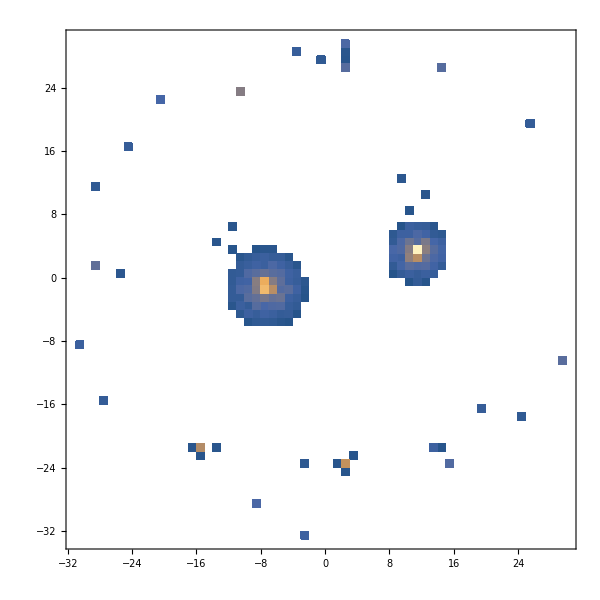

```mathematica
DensityHistogram[reducedNamespaceVectors,{1}]
```